```mathematica
Subscript[n̂, Subscript[3, 2]][r_]=Sum[1/(2 π r)(x (2/Max[x,0.0005]-0.48075)^2) (Hypergeometric0F1[3,-(2/Max[x,0.0005]-0.48075) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/Max[x,0.0005]-0.48075) (x^2+r^2+2 x r)])(0.001),{x,0,2/0.48075,0.001}]
Subscript[n̂, Subscript[3, 10]][r_]=Sum[1/(2 π r)(x (2/Max[x,0.0005]-0.164414)^2) (Hypergeometric0F1[3,-(2/Max[x,0.0005]-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/Max[x,0.0005]-0.164414) (x^2+r^2+2 x r)])(0.001),{x,0,2/0.164414,0.001}]
Subscript[n̂, Subscript[3, 28]][r_]=Sum[1/(2 π r)(x (2/Max[x,0.0005]-0.0827625)^2) (Hypergeometric0F1[3,-(2/Max[x,0.0005]-0.0827625) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/Max[x,0.0005]-0.0827625) (x^2+r^2+2 x r)])(0.001),{x,0,2/0.0827625,0.001}]
```

0.+(0.636314 (Hypergeometric0F1[3,-1999.52 1]-1))/r+(0.318004 (1))/r+1/r+4153+1/r+(23 1)/r+(1.20329×10^-11 (1-1))/r+(2.44854×10^-13 (Hypergeometric0F1[3,-0.0000192308 (17.3056-8.32 r+r^2)]-Hypergeometric0F1[3,1]))/r
 |  |  |  |

0.+(0.636515 (Hypergeometric0F1[3,-1999.84 1]-1))/r+(0.318205 1)/r+12159+2411/r+(7.07445×10^-13 (1-1))/r+(6.06861×10^-14 (Hypergeometric0F1[3,-5.59882×10^-6 (147.963-24.328 r+r^2)]-Hypergeometric0F1[3,-22 1]))/r
 |  |  |  |

0.+(0.636567 (Hypergeometric0F1[3,-1999.92 1]-1))/r+(0.318257 1)/r+1/r+24158+1/r+1/r+(1.06149×10^-13 (1-1))/r+(1.28597×10^-14 (Hypergeometric0F1[3,-1.82857×10^-6 (583.947-48.33 r+r^2)]-Hypergeometric0F1[3,-23 1]))/r
 |  |  |  |

```mathematica
Subscript[ñ, Subscript[3, 2]][r_]=Subscript[n̂, Subscript[3, 2]][r]*r^2
```

r^2 (0.+(0.636314 (Hypergeometric0F1[3,-1999.52 1]-1))/r+(0.318004 1)/r+1/r+4153+1/r+1/r+(1.20329×10^-11 (1-1))/r+(2.44854×10^-13 (Hypergeometric0F1[3,-0.0000192308 (17.3056-8.32 r+r^2)]-Hypergeometric0F1[3,1]))/r)
 |  |  |  |

```mathematica
Subscript[ñ, Subscript[3, 10]][r_]=Subscript[n̂, Subscript[3, 10]][r]*r^2
Subscript[ñ, Subscript[3, 28]][r_]=Subscript[n̂, Subscript[3, 28]][r]*r^2
```

r^2 (0.+(0.636515 (Hypergeometric0F1[3,-1999.84 1]-1))/r+(0.318205 1)/r+12159+2411/r+(7.07445×10^-13 (1-1))/r+(6.06861×10^-14 (Hypergeometric0F1[3,-5.59882×10^-6 (147.963-24.328 r+r^2)]-Hypergeometric0F1[3,1]))/r)
 |  |  |  |

r^2 (0.+(0.636567 (Hypergeometric0F1[3,-1999.92 1]-1))/r+(0.318257 1)/r+1/r+24158+1/r+1/r+(1.06149×10^-13 (1-1))/r+(1.28597×10^-14 (Hypergeometric0F1[3,-1.82857×10^-6 (583.947-48.33 r+r^2)]-Hypergeometric0F1[3,1]))/r)
 |  |  |  |

```mathematica
Subscript[Ψ, nlm][r_,θ_,φ_]=ⅇ^(-r/n) √(((2/n)^3 (-l+n-1)!)/(2 n (l+n)!)) ((2 r)/n)^l LaguerreL[-l+n-1,2 l+1,(2 r)/n] SphericalHarmonicY[l,m,θ,φ]
```

2^(1+l) ⅇ^(-r/n) (r/n)^l √(((-1-l+n)!)/(n^4 (l+n)!)) LaguerreL[-1-l+n,1+2 l,(2 r)/n] SphericalHarmonicY[l,m,θ,φ]

```mathematica
Subscript[n̂, TF(2)][r_]=4Pi((Sqrt[-0.48075+2/Max[r,0.0005]])^3)*HeavisideTheta[-0.48075+2/Max[r,0.0005]]/(3Pi^2)
Subscript[n̂, TF(10)][r_]=4Pi((Sqrt[-0.164414+2/Max[r,0.0005]])^3)*HeavisideTheta[-0.164414+2/Max[r,0.0005]]/(3Pi^2)
Subscript[n̂, TF(28)][r_]=4Pi((Sqrt[-0.0827625+2/Max[r,0.0005]])^3)*HeavisideTheta[-0.0827625+2/Max[r,0.0005]]/(3Pi^2)
```

(4 HeavisideTheta[-0.48075+2/Max[0.0005,r]] (-0.48075+2/Max[0.0005,r])^(3/2))/(3 π)

(4 HeavisideTheta[-0.164414+2/Max[0.0005,r]] (-0.164414+2/Max[0.0005,r])^(3/2))/(3 π)

(4 HeavisideTheta[-0.0827625+2/Max[0.0005,r]] (-0.0827625+2/Max[0.0005,r])^(3/2))/(3 π)

```mathematica
Subscript[ñ, TF(2)][r_]=Subscript[n̂, TF(2)][r]*r^2
Subscript[ñ, TF(10)][r_]=Subscript[n̂, TF(10)][r]*r^2
Subscript[ñ, TF(28)][r_]=Subscript[n̂, TF(28)][r]*r^2
```

(4 r^2 HeavisideTheta[-0.48075+2/Max[0.0005,r]] (-0.48075+2/Max[0.0005,r])^(3/2))/(3 π)

(4 r^2 HeavisideTheta[-0.164414+2/Max[0.0005,r]] (-0.164414+2/Max[0.0005,r])^(3/2))/(3 π)

(4 r^2 HeavisideTheta[-0.0827625+2/Max[0.0005,r]] (-0.0827625+2/Max[0.0005,r])^(3/2))/(3 π)

(4 HeavisideTheta[-0.48075+2/Max[c,r]] (-0.48075+2/Max[c,r])^(3/2))/(3 π)

(4 HeavisideTheta[-0.164414+2/Max[c,r]] (-0.164414+2/Max[c,r])^(3/2))/(3 π)

(4 HeavisideTheta[-0.0827625+2/Max[c,r]] (-0.0827625+2/Max[c,r])^(3/2))/(3 π)

```mathematica
Subscript[n, ex(2)][r_]=Integrate[2*Sin[θ]Sum[Abs[Subscript[Ψ, nlm][r,θ,φ]]^2,{n,1,1},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}]
```

8 ⅇ^(-2 Re[r])

```mathematica
Subscript[ñ, ex(2)][r_]=Subscript[n, ex(2)][r]*r^2
```

8 ⅇ^(-2 Re[r]) r^2

```mathematica
Subscript[n, ex(10)][r_]=Integrate[2*Sin[θ]Sum[Abs[Subscript[Ψ, nlm][r,θ,φ]]^2,{n,1,2},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}]
```

-1/2 ⅇ^(-2 Re[r]) (-16-2 ⅇ^Re[r]-ⅇ^Re[r] Abs[r]^2+2 ⅇ^Re[r] Re[r])

```mathematica
Subscript[ñ, ex(10)][r_]=Subscript[n, ex(10)][r]*r^2
```

-1/2 ⅇ^(-2 Re[r]) r^2 (-16-2 ⅇ^Re[r]-ⅇ^Re[r] Abs[r]^2+2 ⅇ^Re[r] Re[r])

```mathematica
Subscript[n, ex(28)][r_]=Integrate[2*Sin[θ]Sum[Abs[Subscript[Ψ, nlm][r,θ,φ]]^2,{n,1,3},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}]
```

1/78732 ⅇ^(-2 Re[r]) (629856+19683 ⅇ^Re[r] Abs[2-r]^2+13122 ⅇ^Re[r] Abs[r]^2+2304 ⅇ^((4 Re[r])/3) Abs[r]^2+64 ⅇ^((4 Re[r])/3) Abs[r]^4+128 ⅇ^((4 Re[r])/3) Abs[(-6+r) r]^2+32 ⅇ^((4 Re[r])/3) Abs[27-18 r+2 r^2]^2+6561 ⅇ^Re[r] r Conjugate[r]+64 ⅇ^((4 Re[r])/3) Abs[r]^2 Im[r]^2-768 ⅇ^((4 Re[r])/3) Abs[r]^2 Re[r]+64 ⅇ^((4 Re[r])/3) Abs[r]^2 Re[r]^2)

```mathematica
Subscript[ñ, ex(28)][r_]=Subscript[n, ex(28)][r]*r^2
```

1/78732 ⅇ^(-2 Re[r]) r^2 (629856+19683 ⅇ^Re[r] Abs[2-r]^2+13122 ⅇ^Re[r] Abs[r]^2+2304 ⅇ^((4 Re[r])/3) Abs[r]^2+64 ⅇ^((4 Re[r])/3) Abs[r]^4+128 ⅇ^((4 Re[r])/3) Abs[(-6+r) r]^2+32 ⅇ^((4 Re[r])/3) Abs[27-18 r+2 r^2]^2+6561 ⅇ^Re[r] r Conjugate[r]+64 ⅇ^((4 Re[r])/3) Abs[r]^2 Im[r]^2-768 ⅇ^((4 Re[r])/3) Abs[r]^2 Re[r]+64 ⅇ^((4 Re[r])/3) Abs[r]^2 Re[r]^2)

```mathematica
Subscript[EX, 2]=Table[Subscript[n, ex(2)][r],{r,0,6,0.1}]
Subscript[EX, 10]=Table[Subscript[n, ex(10)][r],{r,0,12,0.1}]
Subscript[EX, 28]=Table[Subscript[n, ex(28)][r],{r,0,20,0.1}]
Subscript[OverTilde[EX], 2]=Table[Subscript[ñ, ex(2)][r],{r,0,12,0.1}]
Subscript[OverTilde[EX], 10]=Table[Subscript[ñ, ex(10)][r],{r,0,20,0.1}]
Subscript[OverTilde[EX], 28]=Table[Subscript[ñ, ex(28)][r],{r,0,40,0.1}]
```

{8.,6.54985,5.36256,4.39049,3.59463,2.94304,2.40955,1.97278,1.61517,1.32239,1.08268,0.886425,0.725744,0.594189,0.486481,0.398297,0.326098,0.266986,0.21859,0.178966,0.146525,0.119965,0.0982187,0.0804147,0.065838,0.0539036,0.0441325,0.0361326,0.0295829,0.0242204,0.01983,0.0162354,0.0132925,0.0108829,0.0089102,0.00729506,0.00597269,0.00489002,0.00400361,0.00327788,0.0026837,0.00219723,0.00179894,0.00147285,0.00120586,0.000987278,0.000808315,0.000661793,0.00054183,0.000443613,0.000363199,0.000297363,0.00024346,0.000199328,0.000163196,0.000133614,0.000109394,0.0000895639,0.0000733287,0.0000600365,0.0000491537}

{9.,7.36872,6.03392,4.9424,4.05045,3.32212,2.72786,2.24341,1.84882,1.52771,1.26662,1.05453,0.882365,0.742718,0.629507,0.537753,0.463387,0.403085,0.354135,0.314326,0.28186,0.255279,0.233399,0.215263,0.200101,0.187292,0.176339,0.166847,0.1585,0.151049,0.144298,0.138094,0.132318,0.126881,0.121712,0.116761,0.111989,0.107369,0.102882,0.0985161,0.0942619,0.0901153,0.0860741,0.0821379,0.0783076,0.0745844,0.0709701,0.0674666,0.0640755,0.0607982,0.0576357,0.0545889,0.0516578,0.0488424,0.046142,0.0435556,0.0410817,0.0387187,0.0364645,0.0343168,0.0322729,0.0303302,0.0284856,0.026736,0.0250784,0.0235093,0.0220256,0.0206237,0.0193005,0.0180525,0.0168765,0.0157691,0.0147271,0.0137475,0.0128271,0.0119629,0.0111521,0.0103918,0.00967928,0.00901202,0.00838747,0.00780321,0.00725695,0.00674648,0.00626971,0.00582461,0.0054093,0.00502195,0.00466085,0.00432436,0.00401094,0.00371913,0.00344755,0.00319489,0.00295992,0.00274149,0.00253851,0.00234995,0.00217484,0.00201228,0.00186141,0.00172145,0.00159164,0.00147129,0.00135973,0.00125636,0.00116059,0.0010719,0.000989787,0.000913778,0.000843438,0.000778362,0.00071817,0.000662509,0.000611051,0.000563487,0.000519535,0.000478927,0.000441419,0.00040678,0.000374797}

{9.2963,7.61136,6.2329,5.1061,4.18586,3.43504,2.82309,2.32488,1.91971,1.59061,1.32359,1.10719,0.931997,0.790287,0.675736,0.58317,0.508358,0.447848,0.398828,0.359009,0.326537,0.299908,0.277909,0.259567,0.244097,0.230876,0.219408,0.209301,0.200247,0.192008,0.184397,0.177274,0.170532,0.164093,0.157898,0.151908,0.146093,0.140437,0.134929,0.129564,0.124339,0.119255,0.114316,0.109525,0.104885,0.1004,0.0960728,0.0919063,0.0879023,0.0840619,0.0803853,0.076872,0.0735207,0.0703292,0.067295,0.0644146,0.0616843,0.0590997,0.056656,0.0543484,0.0521714,0.0501197,0.0481875,0.0463693,0.0446594,0.0430519,0.0415413,0.0401219,0.0387883,0.0375351,0.0363572,0.0352496,0.0342074,0.033226,0.0323009,0.0314281,0.0306034,0.0298231,0.0290836,0.0283816,0.027714,0.0270777,0.0264701,0.0258885,0.0253307,0.0247945,0.0242778,0.0237789,0.0232959,0.0228274,0.0223721,0.0219285,0.0214956,0.0210724,0.0206579,0.0202513,0.0198519,0.0194591,0.0190722,0.0186909,0.0183147,0.0179432,0.0175761,0.0172133,0.0168544,0.0164994,0.0161481,0.0158004,0.0154563,0.0151156,0.0147785,0.0144449,0.0141147,0.0137882,0.0134652,0.0131459,0.0128304,0.0125186,0.0122106,0.0119066,0.0116066,0.0113106,0.0110189,0.0107313,0.010448,0.0101691,0.00989464,0.00962463,0.00935916,0.00909827,0.00884201,0.00859041,0.0083435,0.00810133,0.00786389,0.00763122,0.00740332,0.00718019,0.00696184,0.00674825,0.00653942,0.00633533,0.00613596,0.00594129,0.00575127,0.00556588,0.00538509,0.00520883,0.00503708,0.00486978,0.00470688,0.00454833,0.00439406,0.00424401,0.00409813,0.00395634,0.00381859,0.0036848,0.0035549,0.00342883,0.0033065,0.00318785,0.00307281,0.00296129,0.00285323,0.00274855,0.00264717,0.00254902,0.00245403,0.00236211,0.0022732,0.00218722,0.00210409,0.00202375,0.00194611,0.00187112,0.00179869,0.00172876,0.00166125,0.00159611,0.00153326,0.00147263,0.00141416,0.0013578,0.00130346,0.0012511,0.00120065,0.00115205,0.00110525,0.00106019,0.00101681,0.000975055,0.000934877,0.000896224,0.000859043,0.000823287,0.000788907,0.000755857,0.00072409,0.000693564,0.000664233}

{0.,0.0654985,0.214502,0.395144,0.575141,0.735759,0.867439,0.96666,1.03371,1.07114,1.08268,1.07257,1.04507,1.00418,0.953502,0.896167,0.83481,0.77159,0.708231,0.646068,0.5861,0.529044,0.475379,0.425394,0.379227,0.336897,0.298336,0.263407,0.23193,0.203694,0.17847,0.156023,0.136115,0.118515,0.103002,0.0893644,0.077406,0.0669444,0.0578121,0.0498566,0.0429392,0.0369354,0.0317333,0.0272329,0.0233455,0.0199924,0.0171039,0.014619,0.0124838,0.0106511,0.00907999,0.0077344,0.00658315,0.00559913,0.0047588,0.00404181,0.00343058,0.00290993,0.00246678,0.00208987,0.00176953,0.00149747,0.00126655,0.00107068,0.00090465,0.000763991,0.000644898,0.000544119,0.000458884,0.000386834,0.000325959,0.000274552,0.000231161,0.000194552,0.00016368,0.000137656,0.000115729,0.0000972605,0.0000817119,0.0000686264,0.000057618,0.0000483603,0.0000405778,0.0000340375,0.0000285431,0.0000239288,0.000020055,0.0000168037,0.0000140758,0.0000117877,9.86903×10^-6,8.26063×10^-6,6.91269×10^-6,5.78334×10^-6,4.83737×10^-6,4.04522×10^-6,3.38204×10^-6,2.82697×10^-6,2.36249×10^-6,1.97392×10^-6,1.64892×10^-6,1.37716×10^-6,1.14996×10^-6,9.60059×10^-7,8.01367×10^-7,6.68782×10^-7,5.58031×10^-7,4.65539×10^-7,3.88308×10^-7,3.23835×10^-7,2.70021×10^-7,2.25112×10^-7,1.87642×10^-7,1.56384×10^-7,1.30312×10^-7,1.08571×10^-7,9.04428×10^-8,7.53305×10^-8,6.27342×10^-8,5.22366×10^-8,4.34895×10^-8}

{0.,0.0736872,0.241357,0.444816,0.648072,0.830529,0.982031,1.09927,1.18325,1.23744,1.26662,1.27598,1.27061,1.25519,1.23383,1.20994,1.18627,1.16492,1.1474,1.13472,1.12744,1.12578,1.12965,1.13874,1.15258,1.17057,1.19205,1.21632,1.24264,1.27032,1.29868,1.32708,1.35494,1.38173,1.40699,1.43032,1.45137,1.46988,1.48562,1.49843,1.50819,1.51484,1.51835,1.51873,1.51603,1.51033,1.50173,1.49034,1.4763,1.45976,1.44089,1.41986,1.39683,1.37198,1.3455,1.31756,1.28832,1.25797,1.22667,1.19457,1.16183,1.12859,1.09499,1.06115,1.02721,0.993269,0.959433,0.9258,0.892456,0.859481,0.826947,0.794919,0.763454,0.732604,0.70241,0.672913,0.644143,0.616127,0.588888,0.56244,0.536798,0.511969,0.487957,0.464765,0.44239,0.420828,0.400072,0.380111,0.360936,0.342533,0.324886,0.307981,0.2918,0.276326,0.261539,0.24742,0.233949,0.221106,0.208871,0.197223,0.186141,0.175605,0.165595,0.156089,0.147068,0.138513,0.130404,0.122722,0.115449,0.108566,0.102056,0.095902,0.0900873,0.0845958,0.0794121,0.0745212,0.0699086,0.0655603,0.0614631,0.0576041,0.0539708,0.0505515,0.0473349,0.0443101,0.0414668,0.0387951,0.0362854,0.033929,0.031717,0.0296415,0.0276947,0.0258691,0.0241579,0.0225542,0.021052,0.019645,0.0183278,0.017095,0.0159414,0.0148624,0.0138533,0.0129099,0.0120281,0.0112042,0.0104346,0.00971583,0.00904473,0.00841831,0.00783372,0.0072883,0.00677956,0.00630514,0.00586282,0.00545052,0.0050663,0.00470832,0.00437485,0.0040643,0.00377514,0.00350595,0.00325542,0.00302228,0.00280538,0.00260363,0.002416,0.00224154,0.00207935,0.0019286,0.00178851,0.00165835,0.00153743,0.00142512,0.00132082,0.00122398,0.00113408,0.00105064,0.000973199,0.000901346,0.000834685,0.000772852,0.000715504,0.000662326,0.000613021,0.000567315,0.00052495,0.000485688,0.000449307,0.000415601,0.000384378,0.000355457,0.000328674,0.000303874,0.000280912,0.000259656,0.000239981,0.000221772,0.000204923,0.000189332,0.000174909,0.000161567,0.000149228}

{0.,0.0761136,0.249316,0.459549,0.669737,0.85876,1.01631,1.13919,1.22862,1.28839,1.32359,1.3397,1.34208,1.33558,1.32444,1.31213,1.3014,1.29428,1.2922,1.29602,1.30615,1.32259,1.34508,1.37311,1.406,1.44298,1.4832,1.5258,1.56994,1.61479,1.65957,1.7036,1.74625,1.78697,1.8253,1.86087,1.89337,1.92259,1.94838,1.97066,1.98942,2.00468,2.01654,2.02512,2.03057,2.0331,2.0329,2.03021,2.02527,2.01833,2.00963,1.99944,1.988,1.97555,1.96232,1.94854,1.93442,1.92015,1.90591,1.89187,1.87817,1.86495,1.85233,1.8404,1.82925,1.81894,1.80954,1.80107,1.79357,1.78705,1.7815,1.77693,1.77331,1.77061,1.7688,1.76783,1.76765,1.76821,1.76945,1.7713,1.77369,1.77657,1.77985,1.78346,1.78734,1.7914,1.79559,1.79982,1.80404,1.80816,1.81214,1.8159,1.81939,1.82255,1.82533,1.82768,1.82955,1.8309,1.8317,1.8319,1.83147,1.83039,1.82862,1.82616,1.82298,1.81906,1.8144,1.80899,1.80282,1.79589,1.7882,1.77975,1.77055,1.76061,1.74994,1.73855,1.72645,1.71367,1.70021,1.68609,1.67135,1.65599,1.64005,1.62354,1.60649,1.58893,1.57087,1.55236,1.5334,1.51404,1.4943,1.4742,1.45377,1.43304,1.41204,1.39079,1.36932,1.34765,1.32581,1.30383,1.28173,1.25953,1.23726,1.21493,1.19258,1.17023,1.14788,1.12558,1.10332,1.08114,1.05905,1.03706,1.0152,0.993481,0.971912,0.950512,0.929292,0.908266,0.887446,0.866842,0.846464,0.826323,0.806428,0.786786,0.767405,0.748293,0.729455,0.710897,0.692625,0.674643,0.656955,0.639564,0.622474,0.605687,0.589205,0.573029,0.557161,0.541602,0.526351,0.511409,0.496775,0.482448,0.468428,0.454712,0.4413,0.428189,0.415377,0.402862,0.39064,0.37871,0.367067,0.35571,0.344633,0.333834,0.32331,0.313055,0.303067,0.29334,0.283872,0.274658,0.265693,0.256974,0.248495,0.240253,0.232242,0.22446,0.216899,0.209558,0.20243,0.195511,0.188797,0.182284,0.175966,0.16984,0.1639,0.158144,0.152565,0.14716,0.141924,0.136854,0.131945,0.127193,0.122594,0.118144,0.113839,0.109674,0.105647,0.101754,0.0979901,0.0943524,0.0908373,0.0874412,0.0841607,0.0809924,0.0779331,0.0749795,0.0721285,0.0693769,0.0667217,0.0641601,0.061689,0.0593058,0.0570076,0.0547918,0.0526557,0.0505968,0.0486127,0.0467009,0.044859,0.0430847,0.0413759,0.0397304,0.038146,0.0366206,0.0351524,0.0337393,0.0323795,0.0310712,0.0298125,0.0286017,0.0274373,0.0263175,0.0252407,0.0242056,0.0232105,0.0222541,0.021335,0.0204517,0.0196031,0.0187879,0.0180049,0.0172528,0.0165305,0.015837,0.0151711,0.0145319,0.0139183,0.0133295,0.0127643,0.012222,0.0117017,0.0112026,0.0107238,0.0102645,0.00982412,0.00940178,0.00899682,0.00860857,0.00823639,0.00787963,0.00753769,0.00721,0.00689599,0.00659512,0.00630687,0.00603073,0.00576622,0.00551288,0.00527025,0.00503791,0.00481544,0.00460244,0.00439853,0.00420333,0.00401649,0.00383767,0.00366654,0.00350279,0.0033461,0.00319619,0.00305278,0.00291559,0.00278437,0.00265886,0.00253884,0.00242407,0.00231432,0.00220939,0.00210907,0.00201317,0.00192151,0.00183389,0.00175015,0.00167013,0.00159366,0.00152059,0.00145078,0.00138409,0.00132038,0.00125951,0.00120138,0.00114586,0.00109284,0.00104221,0.000993861,0.000947698,0.000903624,0.000861548,0.000821382,0.000783042,0.000746447,0.000711521,0.000678189,0.000646381,0.00061603,0.00058707,0.000559439,0.000533079,0.000507932,0.000483944,0.000461064,0.000439241,0.000418428,0.00039858,0.000379652,0.000361604,0.000344395,0.000327988,0.000312345,0.000297433,0.000283219,0.000269669,0.000256755,0.000244446,0.000232715,0.000221537,0.000210884,0.000200734,0.000191062,0.000181848,0.000173069,0.000164706,0.00015674,0.000149152,0.000141924,0.00013504,0.000128483,0.000122239,0.000116294,0.000110632,0.000105241,0.000100108,0.0000952205,0.0000905679,0.0000861386,0.0000819222,0.0000779087,0.0000740885,0.0000704525,0.000066992,0.0000636986,0.0000605644,0.000057582,0.000054744,0.0000520436,0.0000494744,0.0000470299,0.0000447043,0.000042492,0.0000403874,0.0000383854}

```mathematica
Subscript[TF, 2]=Table[Subscript[n̂, TF(2)][r],{r,0,6,0.1}]
Subscript[TF, 10]=Table[Subscript[n̂, TF(10)][r],{r,0,12,0.1}]
Subscript[TF, 28]=Table[Subscript[n̂, TF(28)][r],{r,0,20,0.1}]
Subscript[OverTilde[TF], 2]=Table[Subscript[ñ, TF(2)][r],{r,0,12,0.1}]
Subscript[OverTilde[TF], 10]=Table[Subscript[ñ, TF(10)][r],{r,0,20,0.1}]
Subscript[OverTilde[TF], 28]=Table[Subscript[ñ, TF(28)][r],{r,0,40,0.1}]
```

{107350.,36.6002,12.465,6.52973,4.07745,2.80197,2.04478,1.55477,1.21779,0.975357,0.794754,0.656442,0.548113,0.461679,0.391632,0.334114,0.286345,0.246287,0.212409,0.183547,0.158801,0.137465,0.11898,0.102897,0.0888549,0.0765571,0.0657604,0.0562634,0.0478982,0.040524,0.0340225,0.0282935,0.0232521,0.0188265,0.0149559,0.011589,0.0086834,0.00620494,0.00412807,0.00243752,0.00113354,0.000251491,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{107362.,37.4935,13.0915,7.03695,4.51297,3.18813,2.39417,1.87533,1.5149,1.25284,1.05548,0.902611,0.781454,0.683583,0.603241,0.536371,0.480049,0.432112,0.390936,0.355278,0.324172,0.296859,0.272735,0.251311,0.232193,0.215055,0.199629,0.185691,0.173054,0.161557,0.151068,0.14147,0.132665,0.124566,0.117102,0.110206,0.103822,0.0979016,0.0924006,0.0872807,0.0825077,0.0780514,0.0738846,0.0699832,0.0663256,0.0628922,0.0596655,0.0566296,0.0537703,0.0510745,0.0485303,0.0461271,0.043855,0.041705,0.039669,0.0377395,0.0359095,0.0341726,0.0325232,0.0309556,0.0294651,0.0280469,0.0266969,0.0254111,0.0241858,0.0230176,0.0219033,0.0208401,0.0198252,0.018856,0.0179301,0.0170452,0.0161995,0.0153907,0.0146172,0.0138772,0.013169,0.0124913,0.0118425,0.0112214,0.0106266,0.010057,0.00951141,0.00898888,0.00848837,0.00800895,0.00754973,0.00710989,0.00668863,0.00628521,0.00589893,0.00552912,0.00517516,0.00483645,0.00451242,0.00420256,0.00390636,0.00362335,0.00335308,0.00309512,0.0028491,0.00261463,0.00239137,0.00217899,0.00197719,0.00178569,0.00160423,0.00143257,0.00127052,0.00111787,0.000974472,0.000840192,0.000714933,0.000598635,0.000491284,0.000392924,0.000303674,0.000223757,0.000153556,0.0000937139,0.0000453768}

{107366.,37.7253,13.2549,7.16992,4.62776,3.29048,2.4873,1.96127,1.59503,1.32814,1.12669,0.970276,0.846023,0.745412,0.662619,0.593542,0.535214,0.485446,0.442588,0.405376,0.372831,0.344177,0.3188,0.296202,0.275979,0.2578,0.24139,0.22652,0.212997,0.200658,0.189366,0.179001,0.169462,0.160662,0.152523,0.14498,0.137973,0.131453,0.125374,0.119696,0.114384,0.109406,0.104734,0.100343,0.0962106,0.0923165,0.0886421,0.085171,0.0818883,0.0787801,0.0758343,0.0730394,0.0703853,0.0678624,0.0654621,0.0631765,0.0609984,0.058921,0.0569381,0.055044,0.0532335,0.0515016,0.0498439,0.0482561,0.0467344,0.0452751,0.0438748,0.0425304,0.041239,0.0399978,0.0388042,0.0376558,0.0365504,0.0354858,0.0344602,0.0334716,0.0325182,0.0315985,0.0307109,0.0298539,0.0290261,0.0282263,0.0274532,0.0267057,0.0259826,0.025283,0.0246058,0.0239501,0.0233151,0.0226998,0.0221036,0.0215255,0.020965,0.0204214,0.019894,0.0193821,0.0188852,0.0184028,0.0179342,0.0174791,0.0170368,0.016607,0.0161892,0.015783,0.0153879,0.0150036,0.0146297,0.0142659,0.0139118,0.0135671,0.0132315,0.0129046,0.0125863,0.0122762,0.011974,0.0116796,0.0113926,0.0111129,0.0108402,0.0105742,0.0103149,0.0100619,0.00981517,0.00957442,0.00933951,0.00911027,0.00888653,0.00866812,0.00845491,0.00824674,0.00804347,0.00784496,0.00765109,0.00746171,0.00727672,0.00709598,0.00691939,0.00674684,0.00657822,0.00641342,0.00625234,0.00609489,0.00594097,0.0057905,0.00564338,0.00549954,0.00535888,0.00522133,0.00508681,0.00495525,0.00482657,0.00470072,0.0045776,0.00445717,0.00433936,0.00422411,0.00411135,0.00400103,0.00389309,0.00378748,0.00368414,0.00358303,0.00348409,0.00338727,0.00329254,0.00319983,0.00310911,0.00302034,0.00293347,0.00284846,0.00276528,0.00268388,0.00260422,0.00252628,0.00245001,0.00237539,0.00230237,0.00223093,0.00216103,0.00209265,0.00202575,0.00196031,0.0018963,0.00183368,0.00177244,0.00171255,0.00165398,0.00159671,0.00154071,0.00148597,0.00143246,0.00138015,0.00132903,0.00127908,0.00123028,0.0011826,0.00113604,0.00109056,0.00104616,0.00100281,0.000960506}

{0.,0.366002,0.498601,0.587675,0.652392,0.700493,0.73612,0.761837,0.779388,0.790039,0.794754,0.794295,0.789283,0.780237,0.7676,0.751756,0.733044,0.711769,0.688205,0.662606,0.635205,0.606221,0.575862,0.544326,0.511804,0.478482,0.44454,0.41016,0.375522,0.340807,0.306203,0.2719,0.238102,0.205021,0.17289,0.141965,0.112537,0.0849456,0.0596094,0.0370746,0.0181366,0.00422757,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{0.,0.374935,0.52366,0.633326,0.722075,0.797033,0.861903,0.918912,0.969533,1.0148,1.05548,1.09216,1.12529,1.15526,1.18235,1.20684,1.22892,1.2488,1.26663,1.28255,1.29669,1.30915,1.32004,1.32944,1.33743,1.3441,1.3495,1.35369,1.35674,1.3587,1.35961,1.35953,1.35849,1.35653,1.3537,1.35002,1.34553,1.34027,1.33427,1.32754,1.32012,1.31204,1.30332,1.29399,1.28406,1.27357,1.26252,1.25095,1.23887,1.2263,1.21326,1.19977,1.18584,1.17149,1.15675,1.14162,1.12612,1.11027,1.09408,1.07757,1.06074,1.04363,1.02623,1.00857,0.990649,0.972492,0.954109,0.935513,0.916716,0.897732,0.878573,0.859251,0.83978,0.820171,0.800437,0.780591,0.760644,0.740609,0.720499,0.700325,0.6801,0.659837,0.639547,0.619244,0.598939,0.578647,0.558378,0.538148,0.517968,0.497852,0.477813,0.457867,0.438025,0.418304,0.398718,0.379281,0.36001,0.340921,0.322029,0.303353,0.28491,0.266718,0.248798,0.231169,0.213853,0.196872,0.180251,0.164015,0.148193,0.132814,0.117911,0.10352,0.0896812,0.0764397,0.0638473,0.0519642,0.0408623,0.0306301,0.0213811,0.0132708,0.00653427,0.00160902,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{0.,0.377253,0.530194,0.645293,0.740441,0.822619,0.895428,0.961023,1.02082,1.0758,1.12669,1.17403,1.21827,1.25975,1.29873,1.33547,1.37015,1.40294,1.43398,1.46341,1.49132,1.51782,1.54299,1.56691,1.58964,1.61125,1.6318,1.65133,1.66989,1.68753,1.70429,1.7202,1.73529,1.74961,1.76317,1.776,1.78814,1.79959,1.8104,1.82058,1.83014,1.83911,1.8475,1.85534,1.86264,1.86941,1.87567,1.88143,1.88671,1.89151,1.89586,1.89976,1.90322,1.90625,1.90888,1.91109,1.91291,1.91434,1.9154,1.91608,1.9164,1.91637,1.916,1.91529,1.91424,1.91287,1.91119,1.90919,1.90689,1.90429,1.9014,1.89823,1.89477,1.89104,1.88704,1.88278,1.87825,1.87348,1.86845,1.86318,1.85767,1.85193,1.84596,1.83976,1.83334,1.8267,1.81985,1.81278,1.80552,1.79805,1.79039,1.78253,1.77448,1.76625,1.75783,1.74923,1.74046,1.73152,1.7224,1.71312,1.70368,1.69408,1.68432,1.67441,1.66435,1.65415,1.64379,1.6333,1.62267,1.61191,1.60101,1.58998,1.57882,1.56755,1.55615,1.54463,1.53299,1.52124,1.50938,1.49742,1.48534,1.47317,1.46089,1.44851,1.43604,1.42348,1.41082,1.39808,1.38525,1.37234,1.35935,1.34627,1.33313,1.3199,1.30661,1.29324,1.27981,1.26631,1.25276,1.23914,1.22546,1.21172,1.19794,1.1841,1.17021,1.15628,1.1423,1.12828,1.11421,1.10011,1.08598,1.07181,1.05761,1.04338,1.02912,1.01484,1.00054,0.986213,0.97187,0.957512,0.94314,0.928757,0.914364,0.899965,0.88556,0.871154,0.856747,0.842343,0.827943,0.813549,0.799165,0.784792,0.770433,0.756091,0.741766,0.727463,0.713182,0.698928,0.684702,0.670506,0.656344,0.642217,0.628129,0.614082,0.600078,0.58612,0.572211,0.558353,0.54455,0.530804,0.517117,0.503493,0.489935,0.476446,0.463028,0.449685,0.43642,0.423236,0.410136,0.397124,0.384203,0.371376,0.358647,0.34602,0.333499,0.321087,0.308788,0.296606,0.284546,0.272611,0.260807,0.249138,0.237608,0.226223,0.214988,0.203908,0.192989,0.182237,0.171657,0.161256,0.151042,0.141021,0.131201,0.12159,0.112196,0.103029,0.0940995,0.0854173,0.0769946,0.0688443,0.0609804,0.0534191,0.0461779,0.0392775,0.0327411,0.0265967,0.0208777,0.0156257,0.0108948,0.00675956,0.00333407,0.000832237,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
Subscript[A, 2]=Table[Subscript[n̂, Subscript[3, 2]][r],{r,0.1,6,0.1}]
Subscript[A, 10]=Table[Subscript[n̂, Subscript[3, 10]][r],{r,0.1,12,0.1}]
Subscript[A, 28]=Table[Subscript[n̂, Subscript[3, 28]][r],{r,0.1,20,0.1}]
Subscript[Ã, 2]=Table[Subscript[ñ, Subscript[3, 2]][r],{r,0,12,0.1}]
Subscript[Ã, 10]=Table[Subscript[ñ, Subscript[3, 10]][r],{r,0,20,0.1}]
Subscript[Ã, 28]=Table[Subscript[ñ, Subscript[3, 28]][r],{r,0,40,0.1}]
```

{11.2377,6.23363,4.19315,3.06784,2.33871,1.82709,1.45291,1.1708,0.953606,0.78372,0.649151,0.5415,0.454446,0.3835,0.325329,0.277267,0.237316,0.20397,0.175946,0.152287,0.132242,0.115162,0.100579,0.0880496,0.077269,0.0679535,0.0598754,0.052858,0.0467413,0.0413984,0.0367127,0.0326071,0.028989,0.0258063,0.0229924,0.0205078,0.0183046,0.0163526,0.0146175,0.0130783,0.0117052,0.0104838,0.00939489,0.00842122,0.00755437,0.00677688,0.00608461,0.0054617,0.00490679,0.00440766,0.00396158,0.00356119,0.00320136,0.00288009,0.00258925,0.00233037,0.00209654,0.0018867,0.0016985,0.00152846}

{12.1179,7.08496,4.99535,3.81381,3.02694,2.45902,2.03155,1.69991,1.43726,1.226,1.054,0.912617,0.795245,0.697088,0.614504,0.544536,0.48491,0.433868,0.389898,0.351838,0.318754,0.289833,0.264469,0.242091,0.222286,0.204676,0.18895,0.17486,0.162182,0.150738,0.140362,0.130938,0.122337,0.114476,0.107261,0.100631,0.0945146,0.0888656,0.0836322,0.0787801,0.0742661,0.0700647,0.0661462,0.0624845,0.0590623,0.0558547,0.0528506,0.0500274,0.0473781,0.0448846,0.0425394,0.0403299,0.0382468,0.0362837,0.0344284,0.0326789,0.0310244,0.029461,0.0279825,0.0265829,0.0252591,0.0240049,0.0228169,0.021692,0.0206243,0.0196134,0.0186534,0.0177436,0.0168798,0.0160599,0.0152819,0.0145425,0.0138405,0.013174,0.01254,0.0119382,0.0113657,0.0108215,0.0103044,0.00981226,0.00934439,0.00889951,0.00847583,0.00807311,0.00768991,0.00732481,0.00697788,0.00664726,0.00633251,0.00603321,0.0057478,0.00547633,0.00521775,0.00497137,0.00473678,0.00451354,0.00430048,0.0040979,0.00390478,0.00372065,0.00354545,0.00337846,0.00321921,0.00306764,0.00292317,0.00278537,0.00265423,0.00252924,0.00240993,0.00229651,0.00218819,0.00208503,0.00198674,0.00189311,0.00180368,0.00171866,0.00163755,0.00156014,0.00148651,0.00141633}

{12.3427,7.30206,5.19926,4.0025,3.19993,2.6167,2.17476,1.82975,1.55495,1.33279,1.15111,1.00121,0.876391,0.771775,0.683623,0.60888,0.545182,0.490683,0.443792,0.403273,0.368124,0.337476,0.310667,0.287081,0.266264,0.247803,0.231356,0.216649,0.203437,0.191521,0.180721,0.170907,0.161939,0.153726,0.146167,0.139194,0.132734,0.126735,0.121144,0.115924,0.111032,0.106442,0.102123,0.0980506,0.0942066,0.0905674,0.0871223,0.0838498,0.0807437,0.0777867,0.0749725,0.0722894,0.0697288,0.0672855,0.0649479,0.0627149,0.0605766,0.0585295,0.0565683,0.0546876,0.0528846,0.0511538,0.0494924,0.0478973,0.0463634,0.0448904,0.0434727,0.0421099,0.0407979,0.0395348,0.0383189,0.0371471,0.0360181,0.0349301,0.0338803,0.0328684,0.0318915,0.0309488,0.0300389,0.0291598,0.0283108,0.0274906,0.0266973,0.0259308,0.0251895,0.024472,0.0237783,0.0231065,0.0224562,0.0218268,0.0212168,0.0206262,0.0200538,0.0194989,0.0189611,0.0184399,0.0179339,0.0174436,0.0169677,0.0165058,0.0160577,0.0156227,0.0152003,0.0147902,0.014392,0.014005,0.0136293,0.0132642,0.0129093,0.0125646,0.0122294,0.0119036,0.0115869,0.011279,0.0109794,0.0106883,0.0104051,0.0101295,0.00986156,0.00960088,0.00934708,0.00910034,0.00886018,0.00862635,0.00839895,0.00817757,0.00796204,0.00775226,0.00754816,0.00734932,0.00715579,0.00696747,0.00678397,0.00660535,0.00643149,0.00626214,0.0060972,0.00593668,0.00578029,0.00562799,0.00547965,0.0053353,0.00519454,0.00505755,0.00492417,0.00479414,0.00466756,0.00454431,0.00442419,0.00430721,0.00419327,0.00408234,0.00397419,0.00386891,0.00376639,0.00366647,0.00356913,0.00347441,0.00338208,0.0032921,0.00320456,0.00311923,0.00303611,0.00295516,0.00287633,0.00279955,0.00272469,0.00265187,0.00258093,0.00251176,0.00244446,0.00237892,0.00231504,0.00225283,0.00219229,0.0021333,0.00207582,0.00201987,0.00196539,0.00191233,0.00186062,0.00181031,0.00176134,0.00171357,0.00166711,0.00162189,0.00157781,0.0015349,0.00149313,0.00145247,0.00141285,0.00137429,0.00133676,0.00130022,0.00126461,0.00122997,0.00119628,0.00116343,0.00113145,0.00110037}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{Indeterminate,0.065326,0.173725,0.284265,0.384023,0.467834,0.534851,0.585943,0.62268,0.647145,0.661305,0.667039,0.665801,0.659046,0.648099,0.633766,0.616946,0.598388,0.57845,0.557678,0.536411,0.514876,0.493392,0.471962,0.45089,0.430152,0.409882,0.390137,0.370972,0.352384,0.334388,0.317077,0.300342,0.284308,0.26887,0.2541,0.239932,0.22639,0.213461,0.201137,0.18937,0.178179,0.167551,0.157414,0.147851,0.138729,0.130143,0.121956,0.114268,0.10697,0.100101,0.0936177,0.0874922,0.081759,0.0763087,0.071241,0.0664482,0.0619447,0.0577431,0.0537668,0.0500744,0.0465988,0.0433379,0.0403247,0.0374462,0.0348172,0.0323197,0.0300113,0.0278526,0.0258304,0.0239587,0.0222078,0.0205695,0.0190724,0.0176468,0.0163377,0.0151268,0.0139785,0.0129426,0.0119584,0.0110502,0.0102183,0.00942847,0.00870529,0.00805326,0.00740914,0.0068513,0.00631866,0.00581257,0.00537605,0.00494463,0.00455841,0.00419889,0.00387019,0.00354978,0.00328956,0.0030084,0.00277383,0.00255914,0.00233967,0.00215677,0.00199004,0.00181902,0.00167153,0.00154516,0.00140825,0.00129249,0.0012025,0.00108363,0.00100508,0.000923514,0.000839804,0.000772616,0.00071746,0.000644737,0.000594899,0.000553082,0.000495822,0.000455214,0.000431469,0.000376587}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{Indeterminate,0.0738808,0.206028,0.35192,0.495059,0.627197,0.745023,0.847547,0.935008,1.0086,1.06972,1.11998,1.16071,1.19339,1.21944,1.23981,1.25559,1.26767,1.27659,1.28302,1.28745,1.29018,1.29163,1.29185,1.29119,1.28966,1.28741,1.28451,1.281,1.2769,1.2722,1.267,1.26118,1.25487,1.24797,1.24055,1.23256,1.22403,1.21496,1.20538,1.19525,1.18463,1.17352,1.1619,1.14988,1.13737,1.1245,1.11117,1.09753,1.08351,1.06919,1.05458,1.03968,1.02458,1.0092,0.993696,0.977986,0.962136,0.946184,0.930101,0.913977,0.897776,0.881537,0.865315,0.849034,0.832837,0.816626,0.800499,0.784424,0.768424,0.752533,0.736732,0.721048,0.705515,0.690085,0.674826,0.659717,0.644757,0.629995,0.615385,0.600968,0.586749,0.5727,0.558868,0.545247,0.531794,0.518593,0.505579,0.492771,0.48021,0.467833,0.455694,0.443769,0.432061,0.420566,0.40932,0.398252,0.387436,0.376831,0.366425,0.356259,0.346304,0.336547,0.327018,0.3177,0.308573,0.299669,0.290976,0.282453,0.274166,0.266055,0.25814,0.250424,0.242902,0.235542,0.228392,0.221417,0.214604,0.207984,0.201541,0.195236,0.189128,0.183179,0.177368,0.171739,0.166256,0.160918,0.155726,0.150698,0.145793,0.141023,0.136414,0.131914,0.127546,0.12332,0.119209,0.115209,0.111345,0.107589,0.103943,0.100403,0.0969941,0.0936582,0.0904365,0.0873296,0.0842972,0.081365,0.0785378,0.0757854,0.0731232,0.0705447,0.0680629,0.0656401,0.0633028,0.0610532,0.0588643,0.0567406,0.0547071,0.0527341,0.0508064,0.0489717,0.0471846,0.0454563,0.0437877,0.0421789,0.0406298,0.039113,0.0376672,0.0362757,0.0349113,0.0336039,0.0323545,0.0311321,0.0299533,0.0288263,0.0277387,0.0266757,0.0256622,0.0246825,0.0237444,0.0228223,0.0219454,0.0211128,0.0202817,0.0194968,0.0187488,0.0180154,0.0173081,0.0166323,0.0159862,0.0153545,0.014747,0.0141668,0.0136142,0.0130656,0.0125443,0.0120549,0.0115732,0.011101,0.0106618,0.0102408}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{Indeterminate,0.0760629,0.214242,0.369042,0.522989,0.666991,0.797082,0.911797,1.01107,1.09593,1.16775,1.22814,1.27857,1.32063,1.35593,1.38559,1.41085,1.43279,1.45208,1.46952,1.48569,1.50098,1.51587,1.53043,1.54504,1.5597,1.57453,1.58958,1.60484,1.62026,1.63579,1.65146,1.66707,1.68269,1.69812,1.71338,1.72832,1.74294,1.75715,1.77091,1.78412,1.79679,1.80887,1.82029,1.8311,1.84118,1.85063,1.8593,1.86733,1.8746,1.8812,1.88708,1.89225,1.89677,1.90056,1.90375,1.90626,1.90814,1.90943,1.91009,1.91022,1.90976,1.90876,1.90727,1.90521,1.90273,1.89974,1.89632,1.89246,1.88816,1.88348,1.8784,1.87293,1.86713,1.86094,1.85444,1.84761,1.84045,1.83302,1.82527,1.81724,1.80896,1.80038,1.79157,1.78252,1.7732,1.7637,1.75394,1.74397,1.73382,1.72343,1.71288,1.70213,1.6912,1.68009,1.66884,1.65739,1.64582,1.63409,1.6222,1.61019,1.59805,1.58577,1.57339,1.56089,1.54827,1.53556,1.52275,1.50982,1.49685,1.48376,1.47061,1.45739,1.4441,1.43073,1.41733,1.40387,1.39035,1.37681,1.36323,1.34959,1.33595,1.32228,1.30857,1.29488,1.28116,1.26743,1.2537,1.23999,1.22627,1.21256,1.19888,1.1852,1.17154,1.15792,1.14433,1.13075,1.11723,1.10374,1.09029,1.07688,1.06355,1.05023,1.03699,1.02381,1.01067,0.997602,0.984612,0.971674,0.95881,0.946019,0.933315,0.920667,0.908108,0.895641,0.883242,0.870924,0.858714,0.846581,0.834521,0.822583,0.810721,0.798952,0.787282,0.775712,0.764243,0.752854,0.741586,0.730421,0.719337,0.70837,0.697516,0.686749,0.676089,0.665547,0.655108,0.644763,0.634539,0.624419,0.614412,0.604497,0.594705,0.585031,0.575437,0.565971,0.556621,0.547365,0.53822,0.52919,0.520272,0.511452,0.502744,0.494149,0.485666,0.477274,0.468998,0.460841,0.452777,0.444813,0.436972,0.429234,0.421584,0.414055,0.406624,0.399301,0.39207,0.384943,0.37793,0.37101,0.364178,0.357461,0.350843,0.344312,0.337878,0.331553,0.325319,0.319167,0.31312,0.307168,0.301306,0.29553,0.289845,0.284259,0.27876,0.273331,0.268007,0.262776,0.257608,0.252533,0.247549,0.242645,0.237816,0.233067,0.228407,0.223824,0.219311,0.214878,0.210524,0.206252,0.202037,0.197902,0.193849,0.189863,0.185934,0.182089,0.178313,0.1746,0.170952,0.167371,0.16386,0.160413,0.15702,0.153691,0.150439,0.147234,0.144084,0.141,0.137981,0.135013,0.132089,0.129238,0.126439,0.123687,0.120989,0.118344,0.115754,0.113216,0.110716,0.10827,0.105881,0.103536,0.101224,0.0989695,0.0967656,0.0945966,0.0924701,0.0903883,0.0883549,0.0863598,0.0843976,0.0824817,0.0806065,0.0787731,0.0769675,0.0752014,0.0734757,0.071796,0.0701306,0.068506,0.0669284,0.0653747,0.0638516,0.0623619,0.0609066,0.0594851,0.0580894,0.0567201,0.0553844,0.0540828,0.0528064,0.0515479,0.0503239,0.0491336,0.0479645,0.0468133,0.0456903,0.0446038,0.0435327,0.0424795,0.0414568,0.0404577,0.0394792,0.0385242,0.0375833,0.0366684,0.0357811,0.0349092,0.0340458,0.0332134,0.0324038,0.0316078,0.0308237,0.0300609,0.0293234,0.0285995,0.0278844,0.0271918,0.0265156,0.0258576,0.0252117,0.0245771,0.0239608,0.0233618,0.0227801,0.0221995,0.0216348,0.0210961,0.020566,0.0200371,0.0195275,0.0190348,0.0185506,0.0180789,0.0176123,0.0171616,0.0167253,0.0162974,0.0158765,0.015464,0.0150675,0.0146828,0.0143032,0.0139255,0.0135648,0.0132206,0.0128754,0.0125335,0.0122076,0.0118926,0.0115818,0.0112772,0.0109789,0.0106908,0.010411,0.0101408,0.00986905,0.00960319,0.00935499,0.00911136,0.00886434,0.00862661,0.00839785,0.00817901,0.0079619,0.00774151,0.00753674,0.00733738,0.00714302,0.00694735,0.0067608,0.0065773,0.00640191,0.006234,0.00606093,0.00589224,0.00573659,0.0055865,0.00543168,0.005278,0.00513752,0.00500083,0.00486463,0.00472833,0.00459724,0.0044743,0.00435259,0.00423417,0.00411422,0.00399882,0.0038931,0.00378724}

```mathematica
Subscript[A, 2]=Table[Subscript[n̂, Subscript[3, 2]][r],{r,0.1,6,0.1}]
Subscript[A, 10]=Table[Subscript[n̂, Subscript[3, 10]][r],{r,0.1,12,0.1}]
Subscript[A, 28]=Table[Subscript[n̂, Subscript[3, 28]][r],{r,0.1,20,0.1}]
```

{6.5326,4.34313,3.1585,2.40015,1.87134,1.4857,1.1958,0.972937,0.798945,0.661305,0.551272,0.462362,0.389968,0.330663,0.281674,0.240995,0.207055,0.178534,0.154481,0.134103,0.116752,0.101941,0.0892177,0.0782795,0.0688243,0.0606335,0.0535168,0.0473179,0.0419005,0.0371542,0.0329945,0.0293303,0.0261073,0.0232587,0.0207428,0.0185133,0.0165369,0.0147826,0.013224,0.0118356,0.0105996,0.00949838,0.00851348,0.00763696,0.0068508,0.00615044,0.00552085,0.00495954,0.00445521,0.00400403,0.00359929,0.00323566,0.00291061,0.0026169,0.00235507,0.00211888,0.00190658,0.0017165,0.00154458,0.00139095}

{7.38808,5.1507,3.91022,3.09412,2.50879,2.06951,1.72969,1.46095,1.24518,1.06972,0.925604,0.806049,0.706146,0.622161,0.551029,0.490463,0.43864,0.394008,0.355408,0.321861,0.292558,0.266865,0.244206,0.224165,0.206346,0.190446,0.176202,0.163393,0.151831,0.141355,0.131842,0.123162,0.115232,0.107956,0.10127,0.0951047,0.0894104,0.0841386,0.0792493,0.0747031,0.0704716,0.0665262,0.0628394,0.0593946,0.0561662,0.0531425,0.0503017,0.0476358,0.0451273,0.0427677,0.040545,0.0384497,0.0364749,0.0346091,0.0328495,0.0311858,0.0296133,0.0281268,0.0267194,0.0253882,0.0241273,0.0229328,0.0218018,0.0207284,0.0197121,0.0187472,0.0178324,0.0169642,0.01614,0.0153578,0.0146148,0.0139091,0.0132392,0.012602,0.0119969,0.0114217,0.0108746,0.010355,0.00986036,0.00939013,0.00894298,0.00851725,0.00811246,0.00772742,0.00736047,0.0070118,0.00667959,0.00636327,0.00606249,0.00577572,0.00550288,0.00524301,0.0049955,0.00475969,0.00453541,0.00432131,0.00411771,0.00392368,0.00373865,0.00356259,0.00339481,0.00323479,0.00308245,0.00293732,0.00279885,0.00266705,0.00254149,0.00242158,0.0023076,0.0021988,0.00209512,0.00199636,0.00190228,0.00181242,0.00172697,0.00164549,0.00156771,0.00149371,0.00142321,0.00135581}

{7.60629,5.35605,4.10047,3.26868,2.66796,2.21412,1.86081,1.5798,1.35301,1.16775,1.015,0.887893,0.781438,0.6918,0.615818,0.551113,0.495776,0.448173,0.40707,0.371422,0.340359,0.313196,0.289307,0.268237,0.249552,0.232919,0.218049,0.204699,0.192659,0.181755,0.171848,0.1628,0.154517,0.146896,0.139867,0.133358,0.127315,0.121686,0.11643,0.111508,0.106888,0.102544,0.0984471,0.0945816,0.0909224,0.0874587,0.0841694,0.0810473,0.078076,0.0752479,0.072552,0.0699796,0.0675248,0.0651769,0.0629339,0.0607863,0.0587301,0.0567608,0.054872,0.0530615,0.0513238,0.0496555,0.0480541,0.046514,0.0450351,0.043612,0.0422438,0.0409268,0.039659,0.0384384,0.0372624,0.0361291,0.0350372,0.0339836,0.0329679,0.0319877,0.0310415,0.0301285,0.0292464,0.0283944,0.0275713,0.0267754,0.0260063,0.0252625,0.0245426,0.0238466,0.0231727,0.0225203,0.0218889,0.021277,0.0206844,0.0201102,0.0195537,0.0190141,0.0184913,0.0179838,0.0174919,0.0170146,0.0165513,0.0161019,0.0156657,0.015242,0.0148307,0.0144313,0.0140432,0.0136664,0.0133003,0.0129443,0.0125987,0.0122625,0.0119358,0.0116182,0.0113094,0.011009,0.0107171,0.0104331,0.0101567,0.00988802,0.00962664,0.00937213,0.00912471,0.00888391,0.00864944,0.00842142,0.00819944,0.00798334,0.00777298,0.00756832,0.00736898,0.00717489,0.00698608,0.0068021,0.00662299,0.00644868,0.00627888,0.00611349,0.00595254,0.00579574,0.00564304,0.00549431,0.00534957,0.00520845,0.00507108,0.00493735,0.00480699,0.00468006,0.00455649,0.00443606,0.00431877,0.00420453,0.00409331,0.00398488,0.00387931,0.00377653,0.00367635,0.00357875,0.00348377,0.00339121,0.00330098,0.00321321,0.00312766,0.00304432,0.00296316,0.00288412,0.00280714,0.00273209,0.00265906,0.00258794,0.0025186,0.00245111,0.0023854,0.00232135,0.00225898,0.00219827,0.00213913,0.00208149,0.0020254,0.00197077,0.00191758,0.00186573,0.00181528,0.00176618,0.00171829,0.0016717,0.00162636,0.00158216,0.00153914,0.00149726,0.00145649,0.00141677,0.0013781,0.00134046,0.00130384,0.00126813,0.00123339,0.00119961,0.00116668,0.00113461,0.00110344,0.00107308}

```mathematica
Subscript[n̂, Subscript[3, 2]][0.0005]
Subscript[n̂, Subscript[3, 10]][0.0005]
Subscript[n̂, Subscript[3, 28]][0.0005]
```

11.3739

12.2545

12.4794

```mathematica
Subscript[A, 2]={11.37391270129158,6.532597697865052,4.343132963458854,3.1585001719386026,2.4001466793809563,1.8713378462271517,1.4856985660450408,1.1958027713336847,0.9729369862251348,0.7989446117449643,0.6613046149931466,0.5512719650838049,0.46236206618488984,0.38996803238535793,0.33066256975205677,0.28167371656308193,0.24099454836279274,0.20705465619329003,0.17853395183693876,0.1544813534240032,0.13410269824682375,0.11675191614492593,0.10194055018324866,0.08921768317094456,0.0782795150688684,0.06882431505527362,0.060633460900479046,0.053516769376182584,0.04731788409090682,0.04190054897613058,0.037154231898505356,0.032994459046848904,0.02933029710179637,0.026107256656332595,0.023258657572813524,0.020742826894849672,0.01851329026290518,0.016536905967797423,0.014782601166801364,0.013224023646634891,0.011835617907238208,0.01059961014281092,0.009498379628478111,0.008513481399819554,0.007636955103081776,0.006850801861000376,0.006150443923025595,0.005520854185218389,0.0049595418243323745,0.0044552126043657745,0.004004025203800207,0.0035992949439848394,0.0032356577834146737,0.0029106078995697845,0.002616896644732152,0.00235507453015425,0.002118884777033409,0.001906578100023286,0.0017165011443316723,0.0015445803022167393,0.0013909544457894785}
```

{11.3739,6.5326,4.34313,3.1585,2.40015,1.87134,1.4857,1.1958,0.972937,0.798945,0.661305,0.551272,0.462362,0.389968,0.330663,0.281674,0.240995,0.207055,0.178534,0.154481,0.134103,0.116752,0.101941,0.0892177,0.0782795,0.0688243,0.0606335,0.0535168,0.0473179,0.0419005,0.0371542,0.0329945,0.0293303,0.0261073,0.0232587,0.0207428,0.0185133,0.0165369,0.0147826,0.013224,0.0118356,0.0105996,0.00949838,0.00851348,0.00763696,0.0068508,0.00615044,0.00552085,0.00495954,0.00445521,0.00400403,0.00359929,0.00323566,0.00291061,0.0026169,0.00235507,0.00211888,0.00190658,0.0017165,0.00154458,0.00139095}

```mathematica
Subscript[A, 10]={12.254507244960482,7.388080262419516,5.150698460168881,3.9102206326694,3.0941209346802974,2.5087870116012456,2.0695083431904124,1.729687362406954,1.4609498564000458,1.2451800820135386,1.069723639023335,0.9256035173415107,0.8060489027711587,0.7061457816473835,0.6221612710992082,0.5510288539332021,0.4904629627136563,0.43863986045732223,0.3940082706953385,0.3554079863214441,0.3218614755461465,0.29255765365120323,0.2668648834204539,0.24420559136054193,0.22416501357613536,0.206346290713228,0.19044574472066847,0.17620158457871826,0.1633933965146437,0.15183110960048957,0.1413554340667376,0.1318416982839374,0.12316216976879464,0.11523172480648423,0.10795584264115646,0.10126950653294113,0.09510466467900192,0.08941042068501608,0.08413855381779875,0.07924925540670502,0.07470311883401907,0.07047159701308418,0.0665261878689694,0.06283943335327927,0.05939464070152324,0.05616620401204293,0.05314249641528445,0.050301733465668214,0.04763575448117979,0.045127256562621704,0.042767660497190156,0.040545027152539805,0.03844969454498054,0.03647486927688854,0.03460909248199021,0.032849467843953324,0.03118577191801649,0.02961329069019472,0.028126761729553945,0.026719373110869568,0.025388246815697683,0.02412728254357027,0.022932802853338565,0.021801845148403096,0.02072838038306791,0.019712121606206223,0.018747160303167087,0.017832449451951816,0.016964197655225968,0.01613996821141303,0.015357806379361742,0.014614798978891525,0.013909095431090446,0.013239171591615712,0.012601981617516628,0.011996904553023525,0.011421695446882417,0.010874636278905843,0.01035495325218987,0.0098603627631565,0.009390128759437677,0.008942980568485515,0.008517254089508215,0.008112462955223028,0.0077274181582650935,0.007360474217431488,0.007011803222690494,0.006679594482887424,0.006363266977353461,0.006062494832997843,0.005775719668202123,0.005502883284920287,0.0052430149699561465,0.004995501950877479,0.004759691947840797,0.004535405619419487,0.004321306397185797,0.004117713766876055,0.003923682927146484,0.003738647829483661,0.0035625886895155707,0.003394806365690456,0.0032347870976131713,0.0030824549592777875,0.002937319446324794,0.0027988510650088804,0.002667045521701975,0.0025414934984628037,0.0024215823249890685,0.002307600490702861,0.0021988030742342837,0.0020951183334902072,0.0019963619979911956,0.0019022755277057588,0.001812422588780873,0.0017269731379097525,0.0016454909999326685,0.0015677081663808639,0.001493711849872083,0.0014232119583576282,0.001355806737201903}
```

{12.2545,7.38808,5.1507,3.91022,3.09412,2.50879,2.06951,1.72969,1.46095,1.24518,1.06972,0.925604,0.806049,0.706146,0.622161,0.551029,0.490463,0.43864,0.394008,0.355408,0.321861,0.292558,0.266865,0.244206,0.224165,0.206346,0.190446,0.176202,0.163393,0.151831,0.141355,0.131842,0.123162,0.115232,0.107956,0.10127,0.0951047,0.0894104,0.0841386,0.0792493,0.0747031,0.0704716,0.0665262,0.0628394,0.0593946,0.0561662,0.0531425,0.0503017,0.0476358,0.0451273,0.0427677,0.040545,0.0384497,0.0364749,0.0346091,0.0328495,0.0311858,0.0296133,0.0281268,0.0267194,0.0253882,0.0241273,0.0229328,0.0218018,0.0207284,0.0197121,0.0187472,0.0178324,0.0169642,0.01614,0.0153578,0.0146148,0.0139091,0.0132392,0.012602,0.0119969,0.0114217,0.0108746,0.010355,0.00986036,0.00939013,0.00894298,0.00851725,0.00811246,0.00772742,0.00736047,0.0070118,0.00667959,0.00636327,0.00606249,0.00577572,0.00550288,0.00524301,0.0049955,0.00475969,0.00453541,0.00432131,0.00411771,0.00392368,0.00373865,0.00356259,0.00339481,0.00323479,0.00308245,0.00293732,0.00279885,0.00266705,0.00254149,0.00242158,0.0023076,0.0021988,0.00209512,0.00199636,0.00190228,0.00181242,0.00172697,0.00164549,0.00156771,0.00149371,0.00142321,0.00135581}

```mathematica
Subscript[A, 28]={12.479373426042201,7.606285661666779,5.35605157496189,4.100471672525829,3.268680267018147,2.667963468457288,2.2141156995207862,1.860810272664075,1.5798003936025407,1.3530055660453324,1.1677489206794909,1.0149952106939282,0.887893354652583,0.7814376731601237,0.6917997799534844,0.6158177632416891,0.5511132269581314,0.4957755745780129,0.4481725920509156,0.4070695818789647,0.3714223548206391,0.3403593718638828,0.3131958067374555,0.28930690835284495,0.2682365226723526,0.249552232154104,0.23291905412441744,0.21804893961552213,0.20469862675931064,0.19265917976100677,0.1817549645967465,0.1718482522248649,0.16280010095369793,0.1545165930380392,0.1468958716430345,0.1398673498228843,0.1333583887222008,0.12731491316094112,0.12168603227343211,0.11643049171410459,0.111507552543818,0.1068882806922805,0.10254386632103818,0.09844709454763752,0.09458160572223974,0.09092243133063889,0.08745868060936465,0.08416935295338289,0.08104726831913267,0.07807595758476982,0.07524790391086492,0.07255200924442419,0.06997960155843445,0.06752476945545054,0.06517686752609037,0.06293388762625383,0.06078627532618326,0.058730132784120814,0.056760751059528367,0.05487200911242151,0.053061544122402104,0.051323754590997084,0.04965546727404781,0.04805407110914814,0.0465139554152061,0.04503514275164716,0.04361198619567045,0.04224376565832815,0.040926824877077224,0.03965897875191078,0.038438428578779396,0.03726235509110411,0.036129093337761084,0.03503715784014222,0.03398359285779787,0.03296787739800143,0.03198772607190741,0.031041547249437914,0.03012851982897164,0.029246386242577686,0.028394430246647485,0.027571346134439508,0.02677544988082743,0.02600627479904893,0.025262540063972147,0.024542621106903667,0.023846634232654214,0.023172703834611914,0.02252025142561708,0.021888868446642867,0.02127695090173106,0.020684415344120147,0.020110214319468037,0.01955367242477626,0.019014129816502415,0.01849129309015867,0.017983802631159014,0.017491931219772296,0.01701463525768212,0.01655132977754878,0.01610192635708966,0.015665650713348394,0.015241951507831857,0.014830694998090664,0.014431305745977315,0.014043224139808854,0.013666386892119978,0.013300292563258532,0.012944313695415627,0.01259866236800965,0.01226251398751179,0.011935780763731196,0.01161819128671628,0.011309433653390794,0.011009019116854165,0.010717070193516925,0.010433064723215172,0.010156704579786699,0.009888021167461318,0.00962663997814836,0.009372133020538086,0.009124711689897449,0.008883913460323405,0.00864944421145064,0.008421419273905818,0.008199437547561222,0.007983336048152647,0.007772976614698552,0.007568323828131355,0.007368976301441666,0.007174893415611068,0.006986081446615751,0.006802100119647341,0.006622993645901711,0.006448676035237935,0.006278884820291033,0.006113494464033621,0.005952538004098921,0.0057957408964200196,0.005643038606499894,0.005494305813555452,0.005349572831314305,0.0052084504370225,0.005071080042677737,0.004937352048069004,0.004806990939600276,0.004680064163327711,0.004556489596767126,0.004436056389045787,0.004318769911459831,0.004204528712013588,0.004093308457468616,0.003984882761542561,0.0038793126988513928,0.0037765251756235237,0.0036763454641967723,0.003578748035349199,0.003483766165351435,0.0033912091454947843,0.0033009827596389794,0.003213213612811631,0.0031276596440708436,0.0030443238527331565,0.0029631606618758443,0.002884117578934868,0.002807138173891769,0.002732088280816747,0.0026590639648293906,0.002587944624872988,0.002518600201553405,0.0024511062560428182,0.002385402803557821,0.002321351656364817,0.002258977264504731,0.0021982664386363663,0.00213912883765277,0.002081492949207498,0.0020254033305007343,0.00197077017413261,0.0019175808248860224,0.0018657311100202408,0.0018152825961804345,0.001766183719855433,0.001718285156720475,0.0016717011056877938,0.0016263571327874353,0.0015821634857611222,0.001539135099884711,0.0014972555888214314,0.0014564874094352882,0.0014167656141153894,0.001378098278771281,0.0013404649046204796,0.001303835328268459,0.0012681304814777296,0.0012333948544022385,0.0011996068791435086,0.0011666806517299198,0.0011346124983714042,0.0011034368320191452,0.0010730838496081259}
```

{12.4794,7.60629,5.35605,4.10047,3.26868,2.66796,2.21412,1.86081,1.5798,1.35301,1.16775,1.015,0.887893,0.781438,0.6918,0.615818,0.551113,0.495776,0.448173,0.40707,0.371422,0.340359,0.313196,0.289307,0.268237,0.249552,0.232919,0.218049,0.204699,0.192659,0.181755,0.171848,0.1628,0.154517,0.146896,0.139867,0.133358,0.127315,0.121686,0.11643,0.111508,0.106888,0.102544,0.0984471,0.0945816,0.0909224,0.0874587,0.0841694,0.0810473,0.078076,0.0752479,0.072552,0.0699796,0.0675248,0.0651769,0.0629339,0.0607863,0.0587301,0.0567608,0.054872,0.0530615,0.0513238,0.0496555,0.0480541,0.046514,0.0450351,0.043612,0.0422438,0.0409268,0.039659,0.0384384,0.0372624,0.0361291,0.0350372,0.0339836,0.0329679,0.0319877,0.0310415,0.0301285,0.0292464,0.0283944,0.0275713,0.0267754,0.0260063,0.0252625,0.0245426,0.0238466,0.0231727,0.0225203,0.0218889,0.021277,0.0206844,0.0201102,0.0195537,0.0190141,0.0184913,0.0179838,0.0174919,0.0170146,0.0165513,0.0161019,0.0156657,0.015242,0.0148307,0.0144313,0.0140432,0.0136664,0.0133003,0.0129443,0.0125987,0.0122625,0.0119358,0.0116182,0.0113094,0.011009,0.0107171,0.0104331,0.0101567,0.00988802,0.00962664,0.00937213,0.00912471,0.00888391,0.00864944,0.00842142,0.00819944,0.00798334,0.00777298,0.00756832,0.00736898,0.00717489,0.00698608,0.0068021,0.00662299,0.00644868,0.00627888,0.00611349,0.00595254,0.00579574,0.00564304,0.00549431,0.00534957,0.00520845,0.00507108,0.00493735,0.00480699,0.00468006,0.00455649,0.00443606,0.00431877,0.00420453,0.00409331,0.00398488,0.00387931,0.00377653,0.00367635,0.00357875,0.00348377,0.00339121,0.00330098,0.00321321,0.00312766,0.00304432,0.00296316,0.00288412,0.00280714,0.00273209,0.00265906,0.00258794,0.0025186,0.00245111,0.0023854,0.00232135,0.00225898,0.00219827,0.00213913,0.00208149,0.0020254,0.00197077,0.00191758,0.00186573,0.00181528,0.00176618,0.00171829,0.0016717,0.00162636,0.00158216,0.00153914,0.00149726,0.00145649,0.00141677,0.0013781,0.00134046,0.00130384,0.00126813,0.00123339,0.00119961,0.00116668,0.00113461,0.00110344,0.00107308}

```mathematica
Subscript[Ã, 2]={0,0.06532597697865053,0.17372531853835418,0.2842650154744743,0.38402346870095305,0.46783446155678793,0.5348514837762149,0.5859433579535056,0.6226796711840864,0.6471451355134211,0.6613046149931466,0.667039077751404,0.6658013753062415,0.6590459747312544,0.6480986367140315,0.6337658622669349,0.6169460438087495,0.5983879563986083,0.5784500039516818,0.5576776858606516,0.536410792987295,0.5148759501991234,0.49339226288692356,0.4719615439742968,0.4508900067966821,0.4301519690954607,0.4098821956872384,0.3901372487523711,0.3709722112727096,0.3523836168892583,0.33438808708654866,0.317076751440218,0.3003422423223949,0.284308024987462,0.26887008154172437,0.25409962946190867,0.23993224180725112,0.22639024269914673,0.2134607608486117,0.20113739966531674,0.18936988651581133,0.17817944650065143,0.1675514166463539,0.15741427108266354,0.14785145079566323,0.13872873768525762,0.13014339341122153,0.12195566895147422,0.11426784363261784,0.10696965463082227,0.10010063009500518,0.09361766149304566,0.08749218646353278,0.08175897589891513,0.07630870616038955,0.07124100453716606,0.06644822660776771,0.06194472246975657,0.05774309849531727,0.0537668403201647,0.050074360048421224,0.046598805124303,0.043337896915525594,0.0403246818848718,0.03744616106410274,0.034817152380636936,0.03231973692261502,0.030011262792679197,0.027852579703068547,0.025830394249870634,0.02395869390503893,0.02220775545503059,0.020569523548135137,0.01907241193273946,0.017646834833874248,0.01633773848844925,0.015126820666300028,0.013978516911856202,0.012942599468791732,0.011958371340204466,0.01105020645727561,0.01021831169431769,0.009428469023458504,0.008705290902323453,0.008053256279690571,0.0074091379776677875,0.006851302202347251,0.006318655871920342,0.0058125728835557965,0.005376048002662617,0.00494462548784798,0.004558410305183825,0.004198887221161413,0.003870190756641923,0.0035497833321828246,0.003289556836600799,0.0030084031614306668,0.002773827594617079,0.0025591447563704348,0.0023396712092722963,0.0021567666504778106,0.0019900350397734005,0.0018190235734241878,0.0016715282322227296,0.0015451590240275345,0.0014082476248607327,0.0012924913382222672,0.0012025027924194868,0.00108363059857224,0.0010050814461449735,0.0009235140082768803,0.0008398036518875986,0.0007726159455935967,0.0007174596949692034,0.0006447374255213143,0.0005948989790007642,0.0005530824964352599,0.0004958217828371811,0.0004552143167588089,0.00043146910250001577,0.0003765869726595972`0}
```

{0,0.065326,0.173725,0.284265,0.384023,0.467834,0.534851,0.585943,0.62268,0.647145,0.661305,0.667039,0.665801,0.659046,0.648099,0.633766,0.616946,0.598388,0.57845,0.557678,0.536411,0.514876,0.493392,0.471962,0.45089,0.430152,0.409882,0.390137,0.370972,0.352384,0.334388,0.317077,0.300342,0.284308,0.26887,0.2541,0.239932,0.22639,0.213461,0.201137,0.18937,0.178179,0.167551,0.157414,0.147851,0.138729,0.130143,0.121956,0.114268,0.10697,0.100101,0.0936177,0.0874922,0.081759,0.0763087,0.071241,0.0664482,0.0619447,0.0577431,0.0537668,0.0500744,0.0465988,0.0433379,0.0403247,0.0374462,0.0348172,0.0323197,0.0300113,0.0278526,0.0258304,0.0239587,0.0222078,0.0205695,0.0190724,0.0176468,0.0163377,0.0151268,0.0139785,0.0129426,0.0119584,0.0110502,0.0102183,0.00942847,0.00870529,0.00805326,0.00740914,0.0068513,0.00631866,0.00581257,0.00537605,0.00494463,0.00455841,0.00419889,0.00387019,0.00354978,0.00328956,0.0030084,0.00277383,0.00255914,0.00233967,0.00215677,0.00199004,0.00181902,0.00167153,0.00154516,0.00140825,0.00129249,0.0012025,0.00108363,0.00100508,0.000923514,0.000839804,0.000772616,0.00071746,0.000644737,0.000594899,0.000553082,0.000495822,0.000455214,0.000431469,0.}

```mathematica
Subscript[Ã, 10]={0,0.07388080262419518,0.2060279384067553,0.3519198569402461,0.49505934954884767,0.6271967529003114,0.745023003548549,0.8475468075794076,0.9350079080960295,1.0085958664309662,1.069723639023335,1.1199802559832281,1.1607104199904688,1.1933863709840782,1.2194360913544482,1.239814921349705,1.2555851845469603,1.2676691967216616,1.2765867970528975,1.2830228306204132,1.287445902184586,1.2901792526018063,1.2916260357549971,1.291847578297267,1.29119047819854,1.2896643169576756,1.287413234311719,1.2845095515788563,1.281004228674807,1.2768996317401176,1.2721989066006394,1.2669987205086386,1.2611806184324574,1.2548734831426136,1.2479695409317688,1.240551455028529,1.2325564542398648,1.2240286591778702,1.214960717129014,1.2053811747359835,1.1952499013443052,1.184627545789945,1.1735219540086201,1.1619011227021336,1.14988024398149,1.1373656312438694,1.1244952241474189,1.111165292256611,1.0975277832463821,1.0835054300685474,1.069191512429754,1.0545761562375602,1.0396797404962739,1.0245790779877992,1.0092011367748348,0.9936964022795881,0.9779858073489966,0.9621358145244265,0.9461842645821947,0.9301013779893698,0.9139768853651166,0.8977761834462492,0.8815369416823345,0.865315233940119,0.8490344604904617,0.8328371378622129,0.8166263028059577,0.8004986558981171,0.7844244995776484,0.7684238865453745,0.7525325125887253,0.7367320165259212,0.7210475071477288,0.7055154541172012,0.6900845133752106,0.6748258811075734,0.6597171290119288,0.6447571849763275,0.6299953558632313,0.6153852400485973,0.6009682406040113,0.5867489550983347,0.5727001649785319,0.5588675729853145,0.545246625247185,0.531794262209425,0.5185929663501889,0.505578506409749,0.49277139472625214,0.4802102157217592,0.467833293124372,0.4556937648242489,0.44376878705708794,0.4320609637313932,0.4205663805112129,0.4093203571526087,0.3982515975646429,0.3874356883253681,0.3768305083231484,0.3664248737676936,0.35625886895155706,0.34630419736408324,0.3365472496356744,0.32701764662978056,0.31770047131448975,0.3085733299172291,0.29966923481843377,0.29097559063900647,0.28245336238672497,0.27416601430040693,0.26605517198234835,0.25813952986932814,0.2504236490280156,0.24290156213274836,0.23554243963796226,0.22839219748856476,0.2214172689509398,0.21460357089587648,0.20798443797618887,0.20154104542302376,0.19523617015707403,0.18912791381943217,0.18317913458275892,0.177368365837827,0.17173873832832007,0.16625635817191298,0.1609184743146286,0.1557256141032933,0.15069768811813442,0.14579343385113785,0.14102250028582067,0.13641432264710587,0.13191358268522227,0.1275455094687828,0.1233195495989214,0.11920935626209411,0.11520873684490499,0.11134521248447875,0.10758870861922178,0.10394314572835733,0.1004025709217291,0.09699413393378367,0.09365820303089392,0.09043652134424834,0.08732962490229167,0.08429721734402174,0.08136497396267425,0.07853783779676782,0.07578543927346353,0.0731232324082825,0.07054474701536553,0.06806293438208526,0.06564013817859334,0.06330283478173909,0.06105316021048185,0.058864297655981994,0.05674064354064428,0.05470705730706337,0.052734131762143054,0.05080641607637104,0.04897168426977055,0.04718463202592235,0.045456342821441495,0.0437876900317193,0.04217891462443752,0.04062984163410793,0.039112976079620165,0.03766720039140327,0.03627571875904386,0.03491126267137335,0.0336039129775842,0.03235454526876673,0.031132121307016494,0.029953280930250074,0.028826290508700232,0.027738745474879676,0.026675690293370188,0.025662182112970385,0.02468246392160334,0.023744394946203652,0.022822280695502857,0.021945434385611303,0.021112809456274532,0.020281718232417683,0.01949680253294274,0.01874877665804657,0.018015386203293383,0.017308128887116393,0.01663233300613916,0.01598616817294246,0.01535451847215199,0.014746999288058234,0.014166793245385565,0.01361418025850876,0.013065573912308264,0.012544338911901765,0.012054870553799559,0.011573174915778606,0.011101042373263438,0.010661785984830936,0.010240783722348934}
```

{0,0.0738808,0.206028,0.35192,0.495059,0.627197,0.745023,0.847547,0.935008,1.0086,1.06972,1.11998,1.16071,1.19339,1.21944,1.23981,1.25559,1.26767,1.27659,1.28302,1.28745,1.29018,1.29163,1.29185,1.29119,1.28966,1.28741,1.28451,1.281,1.2769,1.2722,1.267,1.26118,1.25487,1.24797,1.24055,1.23256,1.22403,1.21496,1.20538,1.19525,1.18463,1.17352,1.1619,1.14988,1.13737,1.1245,1.11117,1.09753,1.08351,1.06919,1.05458,1.03968,1.02458,1.0092,0.993696,0.977986,0.962136,0.946184,0.930101,0.913977,0.897776,0.881537,0.865315,0.849034,0.832837,0.816626,0.800499,0.784424,0.768424,0.752533,0.736732,0.721048,0.705515,0.690085,0.674826,0.659717,0.644757,0.629995,0.615385,0.600968,0.586749,0.5727,0.558868,0.545247,0.531794,0.518593,0.505579,0.492771,0.48021,0.467833,0.455694,0.443769,0.432061,0.420566,0.40932,0.398252,0.387436,0.376831,0.366425,0.356259,0.346304,0.336547,0.327018,0.3177,0.308573,0.299669,0.290976,0.282453,0.274166,0.266055,0.25814,0.250424,0.242902,0.235542,0.228392,0.221417,0.214604,0.207984,0.201541,0.195236,0.189128,0.183179,0.177368,0.171739,0.166256,0.160918,0.155726,0.150698,0.145793,0.141023,0.136414,0.131914,0.127546,0.12332,0.119209,0.115209,0.111345,0.107589,0.103943,0.100403,0.0969941,0.0936582,0.0904365,0.0873296,0.0842972,0.081365,0.0785378,0.0757854,0.0731232,0.0705447,0.0680629,0.0656401,0.0633028,0.0610532,0.0588643,0.0567406,0.0547071,0.0527341,0.0508064,0.0489717,0.0471846,0.0454563,0.0437877,0.0421789,0.0406298,0.039113,0.0376672,0.0362757,0.0349113,0.0336039,0.0323545,0.0311321,0.0299533,0.0288263,0.0277387,0.0266757,0.0256622,0.0246825,0.0237444,0.0228223,0.0219454,0.0211128,0.0202817,0.0194968,0.0187488,0.0180154,0.0173081,0.0166323,0.0159862,0.0153545,0.014747,0.0141668,0.0136142,0.0130656,0.0125443,0.0120549,0.0115732,0.011101,0.0106618,0.0102408}

```mathematica
Subscript[Ã, 28]={0,0.0760628566166678,0.21424206299847565,0.36904245052732465,0.5229888427229036,0.666990867114322,0.7970816518274831,0.9117970336053969,1.011072251905626,1.0959345084967194,1.1677489206794909,1.2281442049396534,1.27856643069972,1.3206296676406095,1.3559275687088297,1.385589967293801,1.4108498610128166,1.4327914105304576,1.4520791982449668,1.4695211905830627,1.4856894192825565,1.5009848299197233,1.515867704609285,1.53043354518655,1.5450423705927514,1.559701450963151,1.574532805881062,1.5895767697971566,1.6048372337929957,1.6202637017900674,1.6357946813707198,1.651461703880952,1.667073033765867,1.682685698184247,1.6981162761934792,1.7133750353303332,1.7283247178397223,1.7429411611732841,1.7571463060283599,1.770907778971531,1.784120840701088,1.7967919984372354,1.8088738019031136,1.8202867781858176,1.8310998867825612,1.8411792344454374,1.8506256816941558,1.8593010067402282,1.8673290620728171,1.8746037416103236,1.8811975977716229,1.887077760447474,1.8922484261400678,1.896770774003606,1.9005574570607953,1.9037501006941784,1.9062575942291065,1.9081420141560854,1.909431665642535,1.910094637203393,1.9102155884064758,1.9097569083310004,1.908756162014398,1.907266082322089,1.9052116138068422,1.9027347812570925,1.899738118683405,1.8963226404023508,1.8924563823160505,1.8881639783784725,1.8834830003601903,1.8783953201425574,1.8729321986295346,1.8671301413011785,1.8609415448930113,1.8544431036375804,1.847611057913373,1.8404533364191742,1.8330191463946344,1.8252669653992735,1.817243535785439,1.808956019880576,1.8003812499868361,1.7915722709064812,1.7825248269138747,1.77320437497379,1.7636970678471056,1.7539419532417757,1.743968270399787,1.7338172696585816,1.723433023040216,1.712876434646589,1.7021285399997743,1.6911971280188989,1.6800885105861536,1.66883920138682,1.6573872504876148,1.6458158084683756,1.634085570147791,1.622195831497556,1.610192635708966,1.5980530292686688,1.5857726348748267,1.5733884323474387,1.5608900294849066,1.5482654614139262,1.535555231198601,1.5227504955674696,1.5098247494332788,1.4968470759432266,1.4837641924889267,1.4706075478993201,1.4573859150056905,1.4441015832014705,1.4307321244263673,1.4173325330926134,1.4038731891558343,1.3903512899270014,1.376808067357314,1.3632284873055893,1.3495871549574845,1.3359490385178856,1.3222816794345358,1.3085744147503673,1.2948774275557586,1.281162116806441,1.2674344310047136,1.2537033981847296,1.2399941760010416,1.2262713463229076,1.2125569872382704,1.1988814370537282,1.185197924847353,1.1715413460235538,1.1579242688873237,1.1443267584980408,1.130751936067658,1.1172318579893266,1.1037408963142288,1.0902914891618445,1.0768839394568686,1.0635485745935975,1.050231946121217,1.0369851579271705,1.023809320687589,1.010669845050958,0.9976024770549345,0.9846118369654083,0.9716737914565893,0.9588101080431972,0.9460189602030572,0.9333152613874192,0.9206673132267934,0.9081083096741227,0.895640710650875,0.8832419977732745,0.8709241218825807,0.8587135220974753,0.846581451081318,0.8345214514643304,0.8225826848797775,0.8107206563396034,0.7989523519112904,0.787282156253793,0.7757122640303225,0.7642433678420347,0.752854246661863,0.7415863491512691,0.7304214909241522,0.7193374035656681,0.7083697079963751,0.6975156337883425,0.6867486740189678,0.676089305493621,0.6655471469615464,0.6551082065311611,0.6447632559465147,0.6345386094125752,0.6244188219721762,0.6144120721017307,0.6044968796465584,0.5947047313346723,0.5850306953649146,0.57543651613412,0.5659711263416596,0.5566207286965,0.5473652795339179,0.5382201530786849,0.5291900153130468,0.5202718675243795,0.511452386695656,0.5027440330785511,0.4941489824392937,0.48566562142671904,0.47727358800895836,0.4689983933864511,0.4608409786917704,0.45277709412986467,0.4448134838615263,0.4369720198479018,0.42923353984325097,0.4215843791166787,0.4140546614796816,0.4066235047559866,0.39930085474854327,0.39206976340210403,0.3849433941461458,0.3779303685508022,0.37100963237289514,0.3641779848849533,0.35746088013577093,0.3508434229735792,0.344312425424121,0.3378777485661198,0.3315526667313721,0.3253190330030933,0.31916681755789816,0.3131201927946123,0.3071678917143653,0.30130607337262716,0.2955296183601166,0.28984476501853246,0.2842589077410657,0.2787595976821441,0.2733313528070732,0.2680070974962285,0.262775638207689,0.2576080067827296,0.25253326666049475,0.24754859264384826,0.24264472775796347,0.23781578849327772,0.23306704526214705,0.22840655652762595,0.2238236556923295,0.2193110389437009,0.21487753432179743,0.21052439583931432,0.20625190393724746,0.20203677621303562,0.19790173778345216,0.19384931534846633,0.18986344501170757,0.18593398647901385,0.18208935767660836,0.17831315848918172,0.17460003665894158,0.1709516617328808,0.167371029952169,0.16385961018872816,0.16041311030365635,0.15701955059154596,0.15369099150708793,0.1504386162784602,0.14723402993880194,0.14408413966961656,0.14100021737622864,0.13798093470289552,0.1350130533854885,0.13208934240290204,0.12923801080552785,0.1264387640481311,0.1236865743168826,0.12098926097076579,0.11834362709715664,0.11575433644949251,0.11321550352486277,0.11071581736214085,0.10827006707268039,0.10588135952601645,0.10353623486749221,0.10122379100864405,0.09896945696982641,0.09676560421164022,0.09459656337298625,0.09247012628560011,0.09038826932953754,0.08835490053279436,0.08635976969623833,0.08439758199031877,0.08248166869858603,0.08060649904555753,0.07877306340219889,0.07696747193978383,0.07520137020332698,0.07347574607271753,0.07179604695271685,0.07013061720211414,0.06850601607700882,0.06692844227600285,0.0653746578522012,0.06385164625658624,0.062361921082783864,0.06090655759930967,0.059485115156755024,0.05808942731135891,0.056720132025290734,0.05538443645500072,0.054082769771357564,0.05280644716475721,0.05154794172823222,0.050323891411935294,0.04913359003487854,0.04796454387617936,0.04681332699214069,0.04569031293277816,0.04460382030648811,0.043532702883658375,0.04247953617078017,0.0414567732677151,0.04045770738856946,0.03947918735472578,0.038524242659626326,0.03758332622577463,0.03666836727206365,0.03578107173689499,0.0349092062722304,0.03404580857492641,0.03321339408573577,0.03240378532072961,0.03160778088813958,0.030823683872071846,0.030060949646841806,0.029323369821009977,0.028599542819030554,0.02788443809944436,0.02719184824458644,0.02651564476830907,0.025857551991817506,0.02521170236365987,0.024577078789648907,0.023960758028882194,0.023361753868342713,0.022780146345707703,0.022199545484789997,0.021634823851283236,0.021096113039895458,0.020566042807837692,0.020037123888576674,0.019527477816954512,0.0190347655434647,0.018550557039384834,0.01807885535187352,0.017612284428801934,0.01716158619584648,0.01672527689186702,0.01629741202309795,0.015876498953168415,0.015463973051734232,0.015067510040348581,0.014682824469695047,0.014303169332920883,0.013925487758447114,0.013564835982447707,0.01322063836844752,0.012875415438085068,0.012533526273921607,0.01220758072306705,0.011892648864861213,0.011581760506212195,0.01127718078130143,0.010978933396610411,0.010690759465501893,0.010410985468909765,0.010140779986919587,0.009869054029561248,0.009603186593130688,0.009354993819771682,0.009111357915519477,0.008864339063705566,0.00862660829481852,0.008397848854694266,0.008179012060365209,0.00796190249272509,0.007741505681991646,0.0075367395295503434,0.0073373774602711475,0.007143019550057782,0.006947346091518547,0.006760801490388497,0.006577295981552305,0.006401905626923973,0.006233998178469141,0.00606092852121886,0.0058922432996471015,0.005736588661715431,0.005586498718502437,0.0054316780670323065,0.005277995181912156,0.0051375210467819316,0.005000832812825453,0.004864629074477939,0.004728332736031142,0.004597236704143918,0.004474296248009872,0.004352588912406363,0.0042341659463888525,0.004114219025609349,0.003998823711812087,0.0038931041252425937,0.0037872424108915535}
```

{0,0.0760629,0.214242,0.369042,0.522989,0.666991,0.797082,0.911797,1.01107,1.09593,1.16775,1.22814,1.27857,1.32063,1.35593,1.38559,1.41085,1.43279,1.45208,1.46952,1.48569,1.50098,1.51587,1.53043,1.54504,1.5597,1.57453,1.58958,1.60484,1.62026,1.63579,1.65146,1.66707,1.68269,1.69812,1.71338,1.72832,1.74294,1.75715,1.77091,1.78412,1.79679,1.80887,1.82029,1.8311,1.84118,1.85063,1.8593,1.86733,1.8746,1.8812,1.88708,1.89225,1.89677,1.90056,1.90375,1.90626,1.90814,1.90943,1.91009,1.91022,1.90976,1.90876,1.90727,1.90521,1.90273,1.89974,1.89632,1.89246,1.88816,1.88348,1.8784,1.87293,1.86713,1.86094,1.85444,1.84761,1.84045,1.83302,1.82527,1.81724,1.80896,1.80038,1.79157,1.78252,1.7732,1.7637,1.75394,1.74397,1.73382,1.72343,1.71288,1.70213,1.6912,1.68009,1.66884,1.65739,1.64582,1.63409,1.6222,1.61019,1.59805,1.58577,1.57339,1.56089,1.54827,1.53556,1.52275,1.50982,1.49685,1.48376,1.47061,1.45739,1.4441,1.43073,1.41733,1.40387,1.39035,1.37681,1.36323,1.34959,1.33595,1.32228,1.30857,1.29488,1.28116,1.26743,1.2537,1.23999,1.22627,1.21256,1.19888,1.1852,1.17154,1.15792,1.14433,1.13075,1.11723,1.10374,1.09029,1.07688,1.06355,1.05023,1.03699,1.02381,1.01067,0.997602,0.984612,0.971674,0.95881,0.946019,0.933315,0.920667,0.908108,0.895641,0.883242,0.870924,0.858714,0.846581,0.834521,0.822583,0.810721,0.798952,0.787282,0.775712,0.764243,0.752854,0.741586,0.730421,0.719337,0.70837,0.697516,0.686749,0.676089,0.665547,0.655108,0.644763,0.634539,0.624419,0.614412,0.604497,0.594705,0.585031,0.575437,0.565971,0.556621,0.547365,0.53822,0.52919,0.520272,0.511452,0.502744,0.494149,0.485666,0.477274,0.468998,0.460841,0.452777,0.444813,0.436972,0.429234,0.421584,0.414055,0.406624,0.399301,0.39207,0.384943,0.37793,0.37101,0.364178,0.357461,0.350843,0.344312,0.337878,0.331553,0.325319,0.319167,0.31312,0.307168,0.301306,0.29553,0.289845,0.284259,0.27876,0.273331,0.268007,0.262776,0.257608,0.252533,0.247549,0.242645,0.237816,0.233067,0.228407,0.223824,0.219311,0.214878,0.210524,0.206252,0.202037,0.197902,0.193849,0.189863,0.185934,0.182089,0.178313,0.1746,0.170952,0.167371,0.16386,0.160413,0.15702,0.153691,0.150439,0.147234,0.144084,0.141,0.137981,0.135013,0.132089,0.129238,0.126439,0.123687,0.120989,0.118344,0.115754,0.113216,0.110716,0.10827,0.105881,0.103536,0.101224,0.0989695,0.0967656,0.0945966,0.0924701,0.0903883,0.0883549,0.0863598,0.0843976,0.0824817,0.0806065,0.0787731,0.0769675,0.0752014,0.0734757,0.071796,0.0701306,0.068506,0.0669284,0.0653747,0.0638516,0.0623619,0.0609066,0.0594851,0.0580894,0.0567201,0.0553844,0.0540828,0.0528064,0.0515479,0.0503239,0.0491336,0.0479645,0.0468133,0.0456903,0.0446038,0.0435327,0.0424795,0.0414568,0.0404577,0.0394792,0.0385242,0.0375833,0.0366684,0.0357811,0.0349092,0.0340458,0.0332134,0.0324038,0.0316078,0.0308237,0.0300609,0.0293234,0.0285995,0.0278844,0.0271918,0.0265156,0.0258576,0.0252117,0.0245771,0.0239608,0.0233618,0.0227801,0.0221995,0.0216348,0.0210961,0.020566,0.0200371,0.0195275,0.0190348,0.0185506,0.0180789,0.0176123,0.0171616,0.0167253,0.0162974,0.0158765,0.015464,0.0150675,0.0146828,0.0143032,0.0139255,0.0135648,0.0132206,0.0128754,0.0125335,0.0122076,0.0118926,0.0115818,0.0112772,0.0109789,0.0106908,0.010411,0.0101408,0.00986905,0.00960319,0.00935499,0.00911136,0.00886434,0.00862661,0.00839785,0.00817901,0.0079619,0.00774151,0.00753674,0.00733738,0.00714302,0.00694735,0.0067608,0.0065773,0.00640191,0.006234,0.00606093,0.00589224,0.00573659,0.0055865,0.00543168,0.005278,0.00513752,0.00500083,0.00486463,0.00472833,0.00459724,0.0044743,0.00435259,0.00423417,0.00411422,0.00399882,0.0038931,0.00378724}

```mathematica
Subscript[d, 3(2)]=Abs[Subscript[A, 2]-Subscript[EX, 2]]
Subscript[d, 3(10)]=Abs[Subscript[A, 10]-Subscript[EX, 10]]
Subscript[d, 3(28)]=Abs[Subscript[A, 28]-Subscript[EX, 28]]
Subscript[d̃, 3(2)]=Abs[Subscript[Ã, 2]-Subscript[OverTilde[EX], 2]]
Subscript[d̃, 3(10)]=Abs[Subscript[Ã, 10]-Subscript[OverTilde[EX], 10]]
Subscript[d̃, 3(28)]=Abs[Subscript[Ã, 28]-Subscript[OverTilde[EX], 28]]
Subscript[S, 3(2)]=Subscript[A, 2]+Subscript[EX, 2]
Subscript[S, 3(10)]=Subscript[A, 10]+Subscript[EX, 10]
Subscript[S, 3(28)]=Subscript[A, 28]+Subscript[EX, 28]
Subscript[S̃, 3(2)]=Subscript[Ã, 2]+Subscript[OverTilde[EX], 2]
Subscript[S̃, 3(10)]=Subscript[Ã, 10]+Subscript[OverTilde[EX], 10]
Subscript[S̃, 3(28)]=Subscript[Ã, 28]+Subscript[OverTilde[EX], 28]
```

{3.37391,0.0172483,1.01943,1.23199,1.19449,1.0717,0.923855,0.776973,0.642235,0.523446,0.421378,0.335153,0.263382,0.204221,0.155818,0.116623,0.0851031,0.0599315,0.0400558,0.0244848,0.0124224,0.0032127,0.00372183,0.008803,0.0124415,0.0149207,0.0165009,0.0173841,0.017735,0.0176801,0.0173242,0.016759,0.0160378,0.0152243,0.0143485,0.0134478,0.0125406,0.0116469,0.010779,0.00994614,0.00915192,0.00840238,0.00769944,0.00704064,0.00643109,0.00586352,0.00534213,0.00485906,0.00441771,0.0040116,0.00364083,0.00330193,0.0029922,0.00271128,0.0024537,0.00222146,0.00200949,0.00181701,0.00164317,0.00148454,0.0013418}

{3.25451,0.0193564,0.883221,1.03218,0.956328,0.81333,0.658356,0.513727,0.387873,0.282529,0.196898,0.128922,0.0763157,0.0365727,0.00734547,0.013276,0.0270757,0.0355545,0.0398734,0.0410822,0.0400011,0.0372787,0.0334663,0.0289428,0.0240645,0.0190546,0.0141063,0.00935421,0.00489315,0.000782149,0.00294225,0.00625184,0.00915592,0.0116488,0.013756,0.0154911,0.0168841,0.0179586,0.0187439,0.0192668,0.0195588,0.0196437,0.0195479,0.0192985,0.0189129,0.0184182,0.0178276,0.0171649,0.0164397,0.0156709,0.0148681,0.0140439,0.0132081,0.0123675,0.0115329,0.0107061,0.00989595,0.00910544,0.00833778,0.00759742,0.00688469,0.00620289,0.00555276,0.00493418,0.00434999,0.0037972,0.0032784,0.00279129,0.00233631,0.00191255,0.00151866,0.00115428,0.000818036,0.000508316,0.00022509,0.0000340078,0.000269634,0.000482876,0.00067567,0.000848341,0.00100266,0.00113977,0.0012603,0.00136598,0.00145771,0.00153586,0.0016025,0.00165764,0.00170242,0.00173814,0.00176478,0.00178375,0.00179547,0.00180062,0.00179977,0.00179391,0.0017828,0.00176777,0.00174885,0.00172637,0.00170118,0.00167335,0.00164314,0.00161117,0.00157759,0.00154249,0.00150645,0.00146959,0.0014318,0.00139382,0.00135536,0.00131676,0.00127819,0.00123977,0.00120137,0.00116349,0.00112596,0.00108878,0.00105229,0.00101643,0.000981009}

{3.18308,0.00507677,0.876846,1.00563,0.917178,0.767078,0.608977,0.464065,0.339912,0.237601,0.155841,0.0921964,0.0441038,0.0088492,0.0160634,0.0326477,0.0427551,0.0479274,0.049345,0.0480605,0.0448858,0.0404518,0.0352863,0.0297402,0.0241395,0.0186761,0.013511,0.00874792,0.00445121,0.000651449,0.00264207,0.00542582,0.00773225,0.00957626,0.0110023,0.0120402,0.0127349,0.0131225,0.0132433,0.013133,0.012831,0.0123671,0.0117725,0.011078,0.0103034,0.00947747,0.00861412,0.00773698,0.00685508,0.00598597,0.00513742,0.00432001,0.00354107,0.00280447,0.00211814,0.00148076,0.000898029,0.000369535,0.000104719,0.000523639,0.00089014,0.00120409,0.00146793,0.00168472,0.00185458,0.00198325,0.00207073,0.00212189,0.00213855,0.00212386,0.00208121,0.00201277,0.00192172,0.0018112,0.00168266,0.0015398,0.00138433,0.00121844,0.00104488,0.000864737,0.000680447,0.000493643,0.000305381,0.00011774,0.0000682012,0.000251887,0.000431193,0.000606153,0.000775657,0.000938577,0.00109512,0.00124409,0.00138541,0.00151872,0.00164377,0.00176002,0.00186812,0.00196715,0.0020576,0.00213958,0.00221275,0.00227754,0.0023342,0.00238261,0.00242314,0.0024562,0.00248172,0.00250011,0.00251194,0.00251696,0.00251597,0.00250907,0.00249655,0.00247875,0.00245621,0.00242887,0.00239729,0.00236185,0.00232259,0.00227996,0.00223445,0.00218594,0.00213495,0.00208186,0.00202661,0.00196969,0.0019113,0.00185166,0.00179084,0.00172929,0.00166711,0.00160433,0.0015414,0.00147833,0.00141522,0.00135233,0.00128982,0.00122765,0.0011661,0.00110521,0.00104512,0.00098576,0.000927513,0.000870206,0.000813919,0.000758893,0.000705021,0.000652344,0.000601027,0.000551015,0.000502356,0.00045502,0.000409175,0.0003647,0.000321605,0.000279999,0.000239843,0.000201034,0.000163693,0.000127844,0.0000932874,0.0000601931,0.0000284841,1.86824×10^-6,0.0000308863,0.0000585887,0.0000849165,0.000110041,0.000133917,0.000156489,0.000177907,0.000198186,0.000217262,0.000235232,0.000252155,0.000268013,0.000282806,0.000296648,0.000309519,0.000321474,0.000332476,0.000342654,0.00035202,0.000360489,0.000368239,0.000375257,0.000381513,0.000387081,0.000392004,0.000396299,0.000399958,0.000403044,0.000405588,0.000407612,0.000409087,0.000410108,0.0004107,0.000410824,0.000410522,0.000409873,0.00040885}

{0.,0.000172483,0.0407771,0.110879,0.191118,0.267924,0.332588,0.380717,0.411031,0.423992,0.421378,0.405535,0.379269,0.345133,0.305403,0.262401,0.217864,0.173202,0.129781,0.0883902,0.0496897,0.014168,0.0180137,0.0465679,0.0716633,0.0932546,0.111546,0.12673,0.139042,0.14869,0.155918,0.161054,0.164227,0.165793,0.165868,0.164735,0.162526,0.159446,0.155649,0.151281,0.146431,0.141244,0.135818,0.130181,0.124506,0.118736,0.113039,0.107337,0.101784,0.0963185,0.0910206,0.0858833,0.080909,0.0761599,0.0715499,0.0671992,0.0630176,0.0590348,0.0552763,0.051677,0.0483048,0.0451013,0.0420713,0.039254,0.0365415,0.0340532,0.0316748,0.0294671,0.0273937,0.0254436,0.0236327,0.0219332,0.0203384,0.0188779,0.0174832,0.0162001,0.0150111,0.0138813,0.0128609,0.0118897,0.0109926,0.01017,0.00938789,0.00867125,0.00802471,0.00738521,0.00683125,0.00630185,0.0057985,0.00536426,0.00493476,0.00455015,0.00419197,0.00386441,0.00354495,0.00328551,0.00300502,0.002771,0.00255678,0.0023377,0.00215512,0.00198866,0.00181787,0.00167057,0.00154436,0.00140758,0.00129193,0.00120204,0.00108324,0.00100476,0.000923244,0.000839579,0.000772428,0.000717303,0.000644607,0.00059479,0.000552992,0.000495746,0.000455152,0.000431417,4.34895×10^-8}

{0.,0.000193564,0.0353288,0.0928964,0.153013,0.203333,0.237008,0.251726,0.248239,0.228848,0.196898,0.155995,0.109895,0.0618078,0.0143971,0.0298709,0.0693138,0.102752,0.12919,0.148307,0.160004,0.164399,0.161977,0.153107,0.138611,0.119091,0.0953583,0.0681922,0.0383623,0.00657788,0.0264803,0.0600802,0.0937567,0.126855,0.159019,0.189766,0.218817,0.245853,0.270661,0.293048,0.31294,0.33021,0.344825,0.356829,0.366154,0.372968,0.377233,0.379172,0.378771,0.376259,0.371702,0.365281,0.357148,0.347404,0.336299,0.323859,0.310337,0.295836,0.280483,0.264466,0.247849,0.23081,0.213448,0.195838,0.178176,0.160432,0.142807,0.125301,0.108031,0.0910567,0.0744144,0.0581871,0.042407,0.0270881,0.0123259,0.00191294,0.0155741,0.0286297,0.0411078,0.052945,0.0641704,0.0747803,0.0847428,0.0941023,0.102856,0.110966,0.118521,0.125467,0.131835,0.137678,0.142947,0.147713,0.151968,0.155735,0.159028,0.161901,0.164303,0.166329,0.167959,0.169202,0.170118,0.170699,0.170953,0.170929,0.170632,0.17006,0.169265,0.168253,0.167005,0.1656,0.163999,0.162238,0.160336,0.158306,0.15613,0.153871,0.151509,0.149043,0.146521,0.143937,0.141265,0.138576,0.135844,0.133058,0.130272,0.127461,0.124633,0.121797,0.118981,0.116152,0.113328,0.110545,0.107756,0.104991,0.102268,0.0995643,0.0968809,0.0942502,0.0916473,0.0890808,0.0865493,0.0840843,0.0816301,0.0792323,0.076895,0.0745814,0.0723202,0.0701195,0.0679517,0.0658349,0.0637652,0.0617578,0.0597773,0.0578523,0.0559869,0.054156,0.0523658,0.0506428,0.048959,0.0473005,0.0457163,0.0441623,0.042651,0.0411841,0.0397629,0.0383883,0.0370336,0.0357386,0.0344872,0.0332529,0.0320665,0.0309294,0.0298113,0.0287293,0.0276922,0.0266881,0.0257025,0.0247608,0.0238478,0.0229715,0.0221068,0.0212831,0.0204998,0.0197144,0.0189719,0.0182631,0.0175661,0.0168925,0.016248,0.0156307,0.0150258,0.0144431,0.0138859,0.0133545,0.0128256,0.0123226,0.0118499,0.0113838,0.0109261,0.0105002,0.0100916}

{0.,0.0000507677,0.0350738,0.0905066,0.146748,0.191769,0.219232,0.227392,0.217544,0.192457,0.155841,0.111558,0.0635095,0.0149551,0.0314843,0.0734572,0.109453,0.13851,0.159878,0.173498,0.179543,0.178393,0.170786,0.157326,0.139043,0.116725,0.0913341,0.0637723,0.0348975,0.00547868,0.0237786,0.0521421,0.0791782,0.104286,0.127186,0.147492,0.165045,0.179647,0.191233,0.199754,0.205296,0.20789,0.207667,0.204831,0.199474,0.191919,0.182275,0.17091,0.157941,0.143723,0.128436,0.112363,0.0957505,0.0787775,0.0617649,0.0447929,0.0281622,0.0120062,0.00352275,0.0182279,0.032045,0.0448043,0.0564272,0.0668666,0.0759638,0.0837922,0.090201,0.0952518,0.0988867,0.101117,0.101979,0.101464,0.0996222,0.0965187,0.0921424,0.0866138,0.079959,0.0722414,0.0635704,0.0539682,0.0435486,0.0323879,0.0205338,0.00811108,0.00481227,0.0181988,0.031891,0.0458797,0.0600669,0.0743447,0.0887045,0.103023,0.117261,0.131354,0.145243,0.158842,0.172166,0.185089,0.197612,0.2097,0.221275,0.232332,0.24285,0.252771,0.262087,0.270796,0.278846,0.286238,0.292993,0.29904,0.304432,0.309143,0.313167,0.316512,0.31921,0.321217,0.322579,0.323314,0.323398,0.322865,0.321761,0.320043,0.317766,0.314964,0.311612,0.307764,0.303438,0.298654,0.293411,0.287772,0.281742,0.275318,0.268574,0.261502,0.254116,0.246463,0.238565,0.230418,0.222071,0.213538,0.204843,0.195979,0.187024,0.177948,0.168774,0.159557,0.150282,0.140965,0.131649,0.122331,0.11303,0.103749,0.0945358,0.0853726,0.0762718,0.0672699,0.0583682,0.0495528,0.0408643,0.0323202,0.0238816,0.0156027,0.00747538,0.000496372,0.00830718,0.0159508,0.0233996,0.0306893,0.0377966,0.0446947,0.0514152,0.0579517,0.0642748,0.0704026,0.0763425,0.0820791,0.087602,0.0929369,0.0980679,0.103003,0.107722,0.112257,0.116603,0.120724,0.124671,0.128432,0.131988,0.135358,0.13855,0.141562,0.144385,0.147034,0.149516,0.151831,0.153964,0.155943,0.157774,0.159437,0.160941,0.162314,0.16354,0.16461,0.165559,0.166371,0.167058,0.16761,0.168044,0.168373,0.16858,0.168667,0.168663,0.168559,0.168346,0.168038,0.167652,0.167175,0.166602,0.16596,0.165244,0.164452,0.163584,0.162652,0.161665,0.160616,0.159493,0.158333,0.157128,0.155854,0.154543,0.153196,0.151807,0.150375,0.148906,0.147414,0.145891,0.144332,0.142749,0.141148,0.13953,0.137877,0.136213,0.134544,0.132856,0.131142,0.129434,0.127716,0.125987,0.124251,0.122512,0.120775,0.119037,0.117289,0.115545,0.113818,0.112082,0.110345,0.108621,0.10691,0.105201,0.103488,0.101801,0.100121,0.0984458,0.0967837,0.0951331,0.0935002,0.0918805,0.0902641,0.0886669,0.0870934,0.0855314,0.083971,0.0824389,0.0809286,0.0794254,0.0779382,0.0764699,0.0750254,0.0735955,0.0721756,0.0707799,0.0694039,0.0680493,0.0667029,0.0653772,0.064074,0.0627992,0.061522,0.0602696,0.0590488,0.057837,0.0566416,0.0554659,0.0543114,0.0531782,0.0520587,0.0509539,0.0498716,0.0488125,0.0477685,0.0467325,0.0457215,0.0447351,0.0437612,0.0427968,0.0418526,0.0409373,0.0400299,0.0391334,0.0382606,0.0374049,0.0365636,0.0357399,0.0349245,0.0341295,0.033357,0.0325949,0.0318364,0.0311043,0.0303906,0.0296863,0.0289898,0.0283108,0.0276532,0.0270059,0.0263638,0.0257411,0.0251316,0.0245372,0.0239522,0.0233757,0.0228149,0.0222689,0.0217379,0.0212057,0.0206871,0.0201925,0.0197045,0.0192157,0.0187444,0.0182883,0.017839,0.0174007,0.0169659,0.0165456,0.0161382,0.015738,0.0153434,0.014956,0.0145836,0.0142218,0.0138639,0.0135071,0.0131663,0.012841,0.0125138,0.0121891,0.0118796,0.0115803,0.0112843,0.010994,0.0107093,0.010434,0.0101665,0.00990806,0.00964752,0.0093923,0.00915426,0.0089203,0.00868249,0.00845354,0.00823314,0.00802227,0.00781275,0.00759958,0.0074017,0.00720889,0.00702078,0.00683105,0.00665017,0.00647206,0.0063018,0.00613878,0.00597036,0.0058061,0.00565467,0.00550859,0.00535759,0.00520754,0.00507053,0.00493713,0.00480406,0.00467075,0.00454249,0.00442225,0.00430311,0.00418714,0.00406951,0.00395633,0.00385272,0.00374886}

{19.3739,13.0824,9.70569,7.54899,5.99478,4.81437,3.89525,3.16858,2.58811,2.12134,1.74399,1.4377,1.18811,0.984157,0.817143,0.67997,0.567092,0.474041,0.397124,0.333448,0.280628,0.236717,0.200159,0.169632,0.144117,0.122728,0.104766,0.0896494,0.0769008,0.066121,0.0569842,0.0492299,0.0426228,0.0369902,0.0321689,0.0280379,0.024486,0.0214269,0.0187862,0.0165019,0.0145193,0.0127968,0.0112973,0.00998633,0.00884282,0.00783808,0.00695876,0.00618265,0.00550137,0.00489883,0.00436722,0.00389666,0.00347912,0.00310994,0.00278009,0.00248869,0.00222828,0.00199614,0.00178983,0.00160462,0.00144011}

{21.2545,14.7568,11.1846,8.85262,7.14457,5.8309,4.79737,3.9731,3.30977,2.77289,2.33635,1.98013,1.68841,1.44886,1.25167,1.08878,0.95385,0.841725,0.748143,0.669734,0.603722,0.547837,0.500263,0.459468,0.424266,0.393638,0.366785,0.343049,0.321894,0.30288,0.285653,0.269935,0.25548,0.242112,0.229668,0.21803,0.207093,0.196779,0.187021,0.177765,0.168965,0.160587,0.1526,0.144977,0.137702,0.130751,0.124113,0.117768,0.111711,0.105925,0.100403,0.0951339,0.0901075,0.0853173,0.0807511,0.076405,0.0722675,0.068332,0.0645913,0.0610362,0.0576612,0.0544575,0.0514184,0.0485379,0.0458068,0.0432214,0.0407727,0.0384562,0.0362647,0.0341925,0.0322343,0.0303839,0.0286362,0.0269867,0.0254291,0.0239598,0.0225738,0.0212664,0.0200342,0.0188724,0.0177776,0.0167462,0.0157742,0.0148589,0.0139971,0.0131851,0.0124211,0.0117015,0.0110241,0.0103869,0.00978666,0.00922201,0.00869056,0.00819039,0.00771961,0.0072769,0.00685982,0.00646766,0.00609852,0.00575092,0.005424,0.00511626,0.00482643,0.00455374,0.00429705,0.00405521,0.00382764,0.0036134,0.00341137,0.00322138,0.00304224,0.00287348,0.00271453,0.00256478,0.00242347,0.00229046,0.00216503,0.00204664,0.00193513,0.00182999,0.0017306}

{21.7757,15.2176,11.5889,9.20657,7.45454,6.103,5.03721,4.18569,3.49951,2.94361,2.49134,2.12219,1.81989,1.57172,1.36754,1.19899,1.05947,0.943624,0.847,0.766079,0.697959,0.640267,0.591105,0.548874,0.512334,0.480428,0.452327,0.42735,0.404946,0.384667,0.366152,0.349122,0.333332,0.318609,0.304794,0.291775,0.279452,0.267752,0.256615,0.245994,0.235846,0.226144,0.21686,0.207972,0.199467,0.191322,0.183531,0.176076,0.16895,0.162138,0.155633,0.149424,0.1435,0.137854,0.132472,0.127349,0.122471,0.11783,0.113417,0.10922,0.105233,0.101443,0.097843,0.0944234,0.0911733,0.088087,0.0851532,0.0823656,0.0797151,0.0771941,0.0747957,0.0725119,0.0703365,0.0682631,0.0662845,0.064396,0.0625911,0.0608647,0.0592122,0.057628,0.0561084,0.054649,0.0532455,0.0518948,0.0505933,0.0493371,0.0481245,0.0469516,0.0458162,0.0447163,0.043649,0.0426129,0.0416058,0.0406261,0.039672,0.0387426,0.0378357,0.036951,0.0360869,0.0352422,0.0344166,0.0336088,0.0328181,0.032044,0.0312858,0.0305426,0.0298145,0.0291007,0.0284006,0.0277143,0.027041,0.0263806,0.0257329,0.0250976,0.0244743,0.023863,0.0232634,0.0226753,0.0220986,0.0215332,0.0209787,0.0204354,0.0199028,0.0193807,0.0188695,0.0183686,0.017878,0.0173976,0.0169275,0.0164672,0.0160169,0.0155765,0.0151456,0.0147243,0.0143126,0.0139101,0.0135168,0.0131327,0.0127576,0.0123913,0.0120337,0.0116849,0.0113444,0.0110124,0.0106886,0.0103729,0.0100651,0.00976532,0.00947314,0.00918855,0.00891141,0.00864164,0.00837894,0.00812333,0.00787466,0.00763269,0.00739734,0.00716857,0.00694611,0.00672981,0.00651971,0.00631551,0.00611713,0.00592445,0.00573735,0.00555569,0.00537926,0.00520809,0.00504197,0.00488071,0.00472431,0.00457262,0.00442544,0.00428272,0.00414438,0.00401024,0.00388018,0.00375416,0.00363202,0.00351369,0.00339899,0.00328791,0.00318035,0.00307608,0.00297516,0.00287746,0.00278281,0.00269119,0.00260251,0.00251668,0.00243357,0.00235315,0.00227534,0.00220006,0.00212717,0.00205668,0.00198851,0.00192254,0.0018587,0.001797,0.00173732}

{0.,0.130824,0.388228,0.679409,0.959165,1.20359,1.40229,1.5526,1.65639,1.71828,1.74399,1.73961,1.71087,1.66322,1.6016,1.52993,1.45176,1.36998,1.28668,1.20375,1.12251,1.04392,0.968771,0.897355,0.830117,0.767049,0.708218,0.653544,0.602902,0.556078,0.512858,0.473099,0.436457,0.402823,0.371872,0.343464,0.317338,0.293335,0.271273,0.250994,0.232309,0.215115,0.199285,0.184647,0.171197,0.158721,0.147247,0.136575,0.126752,0.117621,0.109181,0.101352,0.0940753,0.0873581,0.0810675,0.0752828,0.0698788,0.0648547,0.0602099,0.0558567,0.0518439,0.0480963,0.0446044,0.0413954,0.0383508,0.0355811,0.0329646,0.0305554,0.0283115,0.0262172,0.0242847,0.0224823,0.0208007,0.019267,0.0178105,0.0164754,0.0152425,0.0140758,0.0130243,0.012027,0.0111078,0.0102667,0.00946905,0.00873933,0.0080818,0.00743307,0.00687136,0.00633546,0.00582665,0.00538784,0.00495449,0.00456667,0.0042058,0.00387597,0.00355462,0.0032936,0.00301179,0.00277665,0.00256151,0.00234165,0.00215842,0.00199141,0.00182017,0.00167249,0.00154596,0.00140892,0.00129305,0.00120297,0.00108402,0.00100541,0.000923784,0.000840029,0.000772804,0.000717616,0.000644868,0.000595008,0.000553173,0.000495897,0.000455277,0.000431521,4.34895×10^-8}

{0.,0.147568,0.447385,0.796736,1.14313,1.45773,1.72705,1.94682,2.11825,2.24604,2.33635,2.39596,2.43132,2.44858,2.45327,2.44976,2.44186,2.43259,2.42398,2.41774,2.41489,2.41596,2.42128,2.43059,2.44377,2.46024,2.47947,2.50083,2.52365,2.54722,2.57088,2.59408,2.61612,2.6366,2.65496,2.67087,2.68393,2.69391,2.70058,2.70381,2.70344,2.69947,2.69187,2.68063,2.66591,2.6477,2.62622,2.6015,2.57383,2.54327,2.51009,2.47443,2.43651,2.39656,2.3547,2.31125,2.26631,2.22011,2.17285,2.12467,2.0758,2.02636,1.97652,1.92647,1.87624,1.82611,1.77606,1.7263,1.67688,1.6279,1.57948,1.53165,1.4845,1.43812,1.39249,1.34774,1.30386,1.26088,1.21888,1.17783,1.13777,1.09872,1.06066,1.02363,0.987637,0.952623,0.918665,0.88569,0.853707,0.822743,0.792719,0.763675,0.735569,0.708387,0.682105,0.65674,0.632201,0.608542,0.585702,0.563648,0.5424,0.52191,0.502142,0.483107,0.464769,0.447087,0.430073,0.413698,0.397902,0.382732,0.368111,0.354042,0.340511,0.327497,0.314955,0.302913,0.291326,0.280164,0.269448,0.259145,0.249207,0.239679,0.230514,0.221679,0.213206,0.205051,0.197204,0.189655,0.182415,0.175435,0.168717,0.162283,0.156071,0.1501,0.144371,0.138854,0.133537,0.12844,0.12353,0.118806,0.114256,0.109904,0.105686,0.101641,0.0977642,0.094013,0.0904097,0.0869561,0.0836192,0.0804115,0.0773243,0.0743681,0.071503,0.0687534,0.0661195,0.0635726,0.0611155,0.0587714,0.0565093,0.0543124,0.0522271,0.0502069,0.0482617,0.0463913,0.0445949,0.0428714,0.0411923,0.0395958,0.0380642,0.0365696,0.0351413,0.0337797,0.0324529,0.0311773,0.0299604,0.0287894,0.0276489,0.0265635,0.0255171,0.0245172,0.0235378,0.0226078,0.0217258,0.020849,0.0200218,0.0192345,0.0184647,0.0177237,0.0170167,0.0163416,0.0156832,0.0150509,0.0144477,0.0138738,0.0133056,0.0127661,0.0122598,0.0117625,0.011276,0.0108234,0.01039}

{0.,0.152176,0.463558,0.828591,1.19273,1.52575,1.8134,2.05099,2.23969,2.38433,2.49134,2.56785,2.62064,2.65621,2.68037,2.69772,2.71225,2.72707,2.74428,2.76554,2.79184,2.82358,2.86095,2.90354,2.95104,3.00268,3.05773,3.11538,3.17478,3.23505,3.29537,3.35507,3.41332,3.46966,3.52342,3.57424,3.62169,3.66553,3.70553,3.74157,3.77354,3.80147,3.82541,3.84541,3.86167,3.87428,3.88353,3.88951,3.8926,3.89293,3.89083,3.88652,3.88025,3.87232,3.86288,3.85229,3.84068,3.82829,3.81534,3.80196,3.78839,3.77471,3.76109,3.74767,3.73446,3.72168,3.70928,3.69739,3.68603,3.67521,3.66499,3.65533,3.64624,3.63774,3.62974,3.62227,3.61526,3.60867,3.60247,3.59657,3.59094,3.58552,3.58023,3.57503,3.56986,3.56461,3.55929,3.55376,3.548,3.54198,3.53557,3.52878,3.52152,3.51375,3.50542,3.49652,3.48694,3.47672,3.46578,3.45409,3.44166,3.42844,3.4144,3.39955,3.38387,3.36733,3.34996,3.33174,3.31264,3.29273,3.27196,3.25036,3.22794,3.20472,3.18067,3.15588,3.13033,3.10402,3.07701,3.04932,3.02094,2.99194,2.96233,2.93211,2.90137,2.87009,2.83831,2.80606,2.7734,2.74031,2.70686,2.67308,2.63897,2.60458,2.56996,2.53512,2.50007,2.46488,2.42955,2.39412,2.35861,2.32308,2.28749,2.25192,2.21639,2.1809,2.14549,2.11019,2.075,2.03995,2.00507,1.97038,1.93587,1.90159,1.86755,1.83375,1.80022,1.76698,1.73403,1.70136,1.66905,1.63704,1.60538,1.57407,1.54312,1.51254,1.48231,1.45248,1.42305,1.39398,1.36532,1.33708,1.30922,1.28178,1.25475,1.22814,1.20192,1.17614,1.15077,1.12582,1.10127,1.07715,1.05346,1.03015,1.00727,0.98481,0.962742,0.941082,0.91983,0.898982,0.87852,0.858454,0.838782,0.8195,0.800583,0.782053,0.763908,0.746118,0.728686,0.71163,0.694927,0.678558,0.66255,0.646876,0.631543,0.616529,0.601843,0.587488,0.573439,0.559689,0.546258,0.533127,0.520279,0.507718,0.495453,0.483463,0.471732,0.46028,0.449092,0.43816,0.427475,0.417038,0.406853,0.396903,0.38717,0.377681,0.368423,0.359362,0.350523,0.341901,0.333482,0.325257,0.317228,0.309399,0.301757,0.294291,0.287006,0.279901,0.272974,0.266197,0.259591,0.253155,0.246871,0.240726,0.234745,0.22891,0.223213,0.217653,0.21223,0.206944,0.201789,0.19675,0.191837,0.187059,0.182386,0.177823,0.17338,0.169052,0.164826,0.160691,0.156675,0.152756,0.148927,0.145195,0.141554,0.138008,0.13455,0.131168,0.127873,0.124669,0.121541,0.118477,0.1155,0.112603,0.109768,0.107002,0.104307,0.101684,0.0991241,0.0966196,0.0941834,0.0918091,0.0894969,0.087232,0.0850255,0.0828775,0.0807929,0.0787392,0.0767424,0.0748081,0.0729124,0.0710616,0.0692579,0.0675017,0.065792,0.0641202,0.0624864,0.0608973,0.059353,0.0578444,0.0563634,0.0549263,0.0535321,0.0521679,0.0508298,0.049528,0.0482704,0.0470355,0.0458256,0.044653,0.0435105,0.0423948,0.0413086,0.0402422,0.0392072,0.0382051,0.0372235,0.0362552,0.0353225,0.034417,0.0335293,0.0326576,0.0318111,0.0309935,0.0301932,0.029405,0.0286426,0.0278997,0.0271779,0.0264712,0.0257785,0.0251066,0.0244546,0.0238224,0.0231934,0.0225825,0.0219997,0.0214276,0.0208585,0.0203105,0.0197812,0.0192621,0.018757,0.0182587,0.0177776,0.0173123,0.0168569,0.0164096,0.0159719,0.0155515,0.0151439,0.0147424,0.0143439,0.0139634,0.0136003,0.013237,0.0128779,0.0125356,0.012205,0.0118792,0.0115604,0.0112486,0.0109475,0.0106554,0.0103735,0.0100906,0.00981407,0.00955573,0.00930242,0.00904619,0.00879968,0.00856256,0.00833575,0.00811105,0.00788343,0.00767178,0.00746586,0.00726526,0.00706364,0.00687143,0.00668254,0.00650201,0.00632922,0.0061515,0.00597838,0.00581851,0.00566441,0.00550577,0.00534845,0.00520451,0.00506453,0.00492519,0.00478591,0.00465198,0.00452634,0.00440206,0.0042812,0.00415892,0.00404132,0.00393349,0.00382563}

```mathematica
Subscript[d, 3(2)]=Abs[Subscript[A, 2]-Subscript[EX, 2]]
Subscript[d, 3(10)]=Abs[Subscript[A, 10]-Subscript[EX, 10]]
Subscript[d, 3(28)]=Abs[Subscript[A, 28]-Subscript[EX, 28]]
```

{3.37391,0.0172483,1.01943,1.23199,1.19449,1.0717,0.923855,0.776973,0.642235,0.523446,0.421378,0.335153,0.263382,0.204221,0.155818,0.116623,0.0851031,0.0599315,0.0400558,0.0244848,0.0124224,0.0032127,0.00372183,0.008803,0.0124415,0.0149207,0.0165009,0.0173841,0.017735,0.0176801,0.0173242,0.016759,0.0160378,0.0152243,0.0143485,0.0134478,0.0125406,0.0116469,0.010779,0.00994614,0.00915192,0.00840238,0.00769944,0.00704064,0.00643109,0.00586352,0.00534213,0.00485906,0.00441771,0.0040116,0.00364083,0.00330193,0.0029922,0.00271128,0.0024537,0.00222146,0.00200949,0.00181701,0.00164317,0.00148454,0.0013418}

{3.25451,0.0193564,0.883221,1.03218,0.956328,0.81333,0.658356,0.513727,0.387873,0.282529,0.196898,0.128922,0.0763157,0.0365727,0.00734547,0.013276,0.0270757,0.0355545,0.0398734,0.0410822,0.0400011,0.0372787,0.0334663,0.0289428,0.0240645,0.0190546,0.0141063,0.00935421,0.00489315,0.000782149,0.00294225,0.00625184,0.00915592,0.0116488,0.013756,0.0154911,0.0168841,0.0179586,0.0187439,0.0192668,0.0195588,0.0196437,0.0195479,0.0192985,0.0189129,0.0184182,0.0178276,0.0171649,0.0164397,0.0156709,0.0148681,0.0140439,0.0132081,0.0123675,0.0115329,0.0107061,0.00989595,0.00910544,0.00833778,0.00759742,0.00688469,0.00620289,0.00555276,0.00493418,0.00434999,0.0037972,0.0032784,0.00279129,0.00233631,0.00191255,0.00151866,0.00115428,0.000818036,0.000508316,0.00022509,0.0000340078,0.000269634,0.000482876,0.00067567,0.000848341,0.00100266,0.00113977,0.0012603,0.00136598,0.00145771,0.00153586,0.0016025,0.00165764,0.00170242,0.00173814,0.00176478,0.00178375,0.00179547,0.00180062,0.00179977,0.00179391,0.0017828,0.00176777,0.00174885,0.00172637,0.00170118,0.00167335,0.00164314,0.00161117,0.00157759,0.00154249,0.00150645,0.00146959,0.0014318,0.00139382,0.00135536,0.00131676,0.00127819,0.00123977,0.00120137,0.00116349,0.00112596,0.00108878,0.00105229,0.00101643,0.000981009}

{3.18308,0.00507677,0.876846,1.00563,0.917178,0.767078,0.608977,0.464065,0.339912,0.237601,0.155841,0.0921964,0.0441038,0.0088492,0.0160634,0.0326477,0.0427551,0.0479274,0.049345,0.0480605,0.0448858,0.0404518,0.0352863,0.0297402,0.0241395,0.0186761,0.013511,0.00874792,0.00445121,0.000651449,0.00264207,0.00542582,0.00773225,0.00957626,0.0110023,0.0120402,0.0127349,0.0131225,0.0132433,0.013133,0.012831,0.0123671,0.0117725,0.011078,0.0103034,0.00947747,0.00861412,0.00773698,0.00685508,0.00598597,0.00513742,0.00432001,0.00354107,0.00280447,0.00211814,0.00148076,0.000898029,0.000369535,0.000104719,0.000523639,0.00089014,0.00120409,0.00146793,0.00168472,0.00185458,0.00198325,0.00207073,0.00212189,0.00213855,0.00212386,0.00208121,0.00201277,0.00192172,0.0018112,0.00168266,0.0015398,0.00138433,0.00121844,0.00104488,0.000864737,0.000680447,0.000493643,0.000305381,0.00011774,0.0000682012,0.000251887,0.000431193,0.000606153,0.000775657,0.000938577,0.00109512,0.00124409,0.00138541,0.00151872,0.00164377,0.00176002,0.00186812,0.00196715,0.0020576,0.00213958,0.00221275,0.00227754,0.0023342,0.00238261,0.00242314,0.0024562,0.00248172,0.00250011,0.00251194,0.00251696,0.00251597,0.00250907,0.00249655,0.00247875,0.00245621,0.00242887,0.00239729,0.00236185,0.00232259,0.00227996,0.00223445,0.00218594,0.00213495,0.00208186,0.00202661,0.00196969,0.0019113,0.00185166,0.00179084,0.00172929,0.00166711,0.00160433,0.0015414,0.00147833,0.00141522,0.00135233,0.00128982,0.00122765,0.0011661,0.00110521,0.00104512,0.00098576,0.000927513,0.000870206,0.000813919,0.000758893,0.000705021,0.000652344,0.000601027,0.000551015,0.000502356,0.00045502,0.000409175,0.0003647,0.000321605,0.000279999,0.000239843,0.000201034,0.000163693,0.000127844,0.0000932874,0.0000601931,0.0000284841,1.86824×10^-6,0.0000308863,0.0000585887,0.0000849165,0.000110041,0.000133917,0.000156489,0.000177907,0.000198186,0.000217262,0.000235232,0.000252155,0.000268013,0.000282806,0.000296648,0.000309519,0.000321474,0.000332476,0.000342654,0.00035202,0.000360489,0.000368239,0.000375257,0.000381513,0.000387081,0.000392004,0.000396299,0.000399958,0.000403044,0.000405588,0.000407612,0.000409087,0.000410108,0.0004107,0.000410824,0.000410522,0.000409873,0.00040885}

```mathematica
Subscript[R, 3(2)]=(Subscript[d, 3(2)])/(Subscript[S, 3(2)])
Subscript[R, 3(10)]=(Subscript[d, 3(10)])/(Subscript[S, 3(10)])
Subscript[R, 3(28)]=(Subscript[d, 3(28)])/(Subscript[S, 3(28)])
Subscript[R̃, 3(2)]=(Subscript[d̃, 3(2)])/(Subscript[S̃, 3(2)])
Subscript[R̃, 3(10)]=(Subscript[d̃, 3(10)])/(Subscript[S̃, 3(10)])
Subscript[R̃, 3(28)]=(Subscript[d̃, 3(28)])/(Subscript[S̃, 3(28)])
```

{0.174147,0.00131843,0.105034,0.1632,0.199254,0.222604,0.237175,0.245212,0.248148,0.246753,0.241617,0.233118,0.221682,0.207508,0.190686,0.171512,0.150069,0.126427,0.100865,0.0734293,0.0442665,0.0135719,0.0185943,0.0518946,0.0863291,0.121576,0.157503,0.193912,0.230621,0.26739,0.304018,0.340423,0.376274,0.411577,0.446036,0.479629,0.512155,0.543563,0.573771,0.602727,0.630327,0.656598,0.681528,0.705027,0.727267,0.748082,0.767684,0.785919,0.80302,0.81889,0.83367,0.847376,0.860045,0.871812,0.882597,0.892623,0.901813,0.910263,0.918061,0.92517,0.931736}

{0.153121,0.00131169,0.0789675,0.116596,0.133854,0.139486,0.137233,0.129301,0.11719,0.10189,0.0842762,0.0651077,0.0451997,0.0252423,0.00586854,0.0121934,0.0283857,0.04224,0.0532965,0.0613411,0.0662575,0.0680471,0.0668974,0.0629918,0.0567203,0.0484064,0.0384592,0.0272679,0.0152012,0.00258237,0.0103001,0.0231605,0.0358381,0.0481131,0.0598953,0.0710501,0.0815287,0.0912627,0.100223,0.108383,0.115756,0.122324,0.128099,0.133114,0.137347,0.140865,0.143641,0.145751,0.147163,0.147943,0.148084,0.147622,0.146582,0.144959,0.14282,0.140123,0.136935,0.133253,0.129085,0.124474,0.119399,0.113903,0.107992,0.101656,0.0949639,0.0878545,0.0804067,0.0725837,0.0644238,0.0559349,0.0471133,0.0379898,0.0285665,0.0188358,0.0088517,0.00141937,0.0119446,0.0227061,0.0337258,0.0449515,0.0564004,0.0680614,0.0798965,0.0919298,0.104144,0.116485,0.129015,0.14166,0.154427,0.16734,0.180325,0.193423,0.2066,0.219845,0.233143,0.246522,0.25989,0.273324,0.286766,0.30019,0.313638,0.327066,0.340447,0.353811,0.367133,0.380374,0.393572,0.406706,0.419713,0.432679,0.445515,0.458244,0.47087,0.48338,0.495723,0.50797,0.520066,0.531986,0.543784,0.55543,0.56686}

{0.146176,0.000333611,0.0756623,0.109229,0.123036,0.125689,0.120896,0.11087,0.0971313,0.0807175,0.0625532,0.0434441,0.0242343,0.00563025,0.0117462,0.0272293,0.0403551,0.0507908,0.0582585,0.0627357,0.0643102,0.0631796,0.0596955,0.0541841,0.0471167,0.0388738,0.0298699,0.0204701,0.0109921,0.00169354,0.00721577,0.0155413,0.0231968,0.0300564,0.0360974,0.0412654,0.0455711,0.0490099,0.0516074,0.0533876,0.0544042,0.0546867,0.0542862,0.0532665,0.0516549,0.0495366,0.0469354,0.0439412,0.0405747,0.036919,0.0330098,0.0289111,0.0246764,0.0203438,0.0159893,0.0116276,0.00733261,0.00313618,0.000923312,0.00479433,0.00845876,0.0118696,0.0150029,0.0178422,0.0203413,0.0225146,0.0243177,0.0257619,0.0268275,0.0275133,0.0278252,0.0277578,0.0273219,0.0265326,0.0253854,0.0239114,0.0221171,0.0200189,0.0176463,0.0150055,0.0121274,0.00903297,0.00573533,0.00226881,0.00134803,0.00510542,0.00895995,0.0129102,0.0169298,0.0209896,0.0250892,0.0291952,0.0332985,0.037383,0.0414339,0.0454285,0.0493744,0.0532367,0.0570181,0.0607107,0.0642932,0.0677662,0.0711253,0.0743542,0.0774518,0.0804186,0.0832386,0.0859124,0.0884468,0.090818,0.0930428,0.0951103,0.0970177,0.0987645,0.100359,0.101784,0.10305,0.10416,0.105101,0.105881,0.10651,0.106968,0.107269,0.107419,0.107402,0.107231,0.106908,0.106432,0.105795,0.105014,0.104085,0.102997,0.101772,0.100401,0.0988793,0.0972196,0.0954236,0.0934803,0.0914041,0.0891927,0.0868489,0.0843619,0.0817594,0.0790208,0.0761481,0.0731613,0.0700458,0.0668021,0.0634454,0.0599675,0.0563722,0.0526544,0.0488338,0.0448954,0.0408405,0.0366842,0.0324229,0.0280438,0.0235661,0.0189966,0.0143085,0.00953099,0.00465646,0.000315344,0.00538338,0.0105457,0.0157859,0.0211289,0.0265604,0.0320627,0.0376578,0.043342,0.0490939,0.0549258,0.0608427,0.0668322,0.0728848,0.0790185,0.0852194,0.0914918,0.0978162,0.104216,0.110686,0.117191,0.123771,0.130413,0.137096,0.143833,0.150625,0.157469,0.16435,0.171278,0.178253,0.185273,0.192315,0.199402,0.206536,0.213688,0.220865,0.228087,0.235334}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,0.00131843,0.105034,0.1632,0.199254,0.222604,0.237175,0.245212,0.248148,0.246753,0.241617,0.233118,0.221682,0.207508,0.190686,0.171512,0.150069,0.126427,0.100865,0.0734293,0.0442665,0.0135719,0.0185943,0.0518946,0.0863291,0.121576,0.157503,0.193912,0.230621,0.26739,0.304018,0.340423,0.376274,0.411577,0.446036,0.479629,0.512155,0.543563,0.573771,0.602727,0.630327,0.656598,0.681528,0.705027,0.727267,0.748082,0.767684,0.785919,0.80302,0.81889,0.83367,0.847376,0.860045,0.871812,0.882597,0.892623,0.901813,0.910263,0.918061,0.92517,0.931736,0.93773,0.94321,0.94827,0.952822,0.957056,0.960873,0.964385,0.967583,0.97049,0.973155,0.975576,0.977774,0.979805,0.98162,0.983289,0.984815,0.98618,0.987452,0.988588,0.989626,0.990579,0.991429,0.99221,0.992936,0.993562,0.994163,0.994695,0.995168,0.995624,0.996016,0.996382,0.996713,0.997016,0.997278,0.997544,0.997754,0.997964,0.998155,0.998314,0.998472,0.998617,0.998736,0.998852,0.998963,0.999051,0.999137,0.999226,0.999284,0.999356,0.999415,0.999464,0.999514,0.999564,0.999596,0.999635,0.999673,0.999696,0.999724,0.999758,1.}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,0.00131169,0.0789675,0.116596,0.133854,0.139486,0.137233,0.129301,0.11719,0.10189,0.0842762,0.0651077,0.0451997,0.0252423,0.00586854,0.0121934,0.0283857,0.04224,0.0532965,0.0613411,0.0662575,0.0680471,0.0668974,0.0629918,0.0567203,0.0484064,0.0384592,0.0272679,0.0152012,0.00258237,0.0103001,0.0231605,0.0358381,0.0481131,0.0598953,0.0710501,0.0815287,0.0912627,0.100223,0.108383,0.115756,0.122324,0.128099,0.133114,0.137347,0.140865,0.143641,0.145751,0.147163,0.147943,0.148084,0.147622,0.146582,0.144959,0.14282,0.140123,0.136935,0.133253,0.129085,0.124474,0.119399,0.113903,0.107992,0.101656,0.0949639,0.0878545,0.0804067,0.0725837,0.0644238,0.0559349,0.0471133,0.0379898,0.0285665,0.0188358,0.0088517,0.00141937,0.0119446,0.0227061,0.0337258,0.0449515,0.0564004,0.0680614,0.0798965,0.0919298,0.104144,0.116485,0.129015,0.14166,0.154427,0.16734,0.180325,0.193423,0.2066,0.219845,0.233143,0.246522,0.25989,0.273324,0.286766,0.30019,0.313638,0.327066,0.340447,0.353811,0.367133,0.380374,0.393572,0.406706,0.419713,0.432679,0.445515,0.458244,0.47087,0.48338,0.495723,0.50797,0.520066,0.531986,0.543784,0.55543,0.56686,0.578174,0.58931,0.600231,0.611016,0.621607,0.632001,0.642203,0.652254,0.66208,0.671703,0.681186,0.690426,0.699477,0.708364,0.717041,0.725501,0.733806,0.741902,0.749804,0.757504,0.76507,0.772381,0.779532,0.786535,0.793309,0.799917,0.806378,0.812633,0.818725,0.824646,0.830434,0.836012,0.841447,0.846753,0.851876,0.856833,0.861691,0.866389,0.870897,0.875336,0.879607,0.883743,0.887754,0.891647,0.89543,0.899042,0.902586,0.906027,0.909305,0.9125,0.915623,0.918601,0.921483,0.924295,0.927012,0.929603,0.932137,0.934578,0.936954,0.939204,0.941407,0.943568,0.945579,0.947562,0.949498,0.951333,0.953102,0.954824,0.956497,0.958086,0.95962,0.961113,0.962569,0.963928,0.965256,0.96657,0.967808,0.968977,0.970145,0.971275}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,0.000333611,0.0756623,0.109229,0.123036,0.125689,0.120896,0.11087,0.0971313,0.0807175,0.0625532,0.0434441,0.0242343,0.00563025,0.0117462,0.0272293,0.0403551,0.0507908,0.0582585,0.0627357,0.0643102,0.0631796,0.0596955,0.0541841,0.0471167,0.0388738,0.0298699,0.0204701,0.0109921,0.00169354,0.00721577,0.0155413,0.0231968,0.0300564,0.0360974,0.0412654,0.0455711,0.0490099,0.0516074,0.0533876,0.0544042,0.0546867,0.0542862,0.0532665,0.0516549,0.0495366,0.0469354,0.0439412,0.0405747,0.036919,0.0330098,0.0289111,0.0246764,0.0203438,0.0159893,0.0116276,0.00733261,0.00313618,0.000923312,0.00479433,0.00845876,0.0118696,0.0150029,0.0178422,0.0203413,0.0225146,0.0243177,0.0257619,0.0268275,0.0275133,0.0278252,0.0277578,0.0273219,0.0265326,0.0253854,0.0239114,0.0221171,0.0200189,0.0176463,0.0150055,0.0121274,0.00903297,0.00573533,0.00226881,0.00134803,0.00510542,0.00895995,0.0129102,0.0169298,0.0209896,0.0250892,0.0291952,0.0332985,0.037383,0.0414339,0.0454285,0.0493744,0.0532367,0.0570181,0.0607107,0.0642932,0.0677662,0.0711253,0.0743542,0.0774518,0.0804186,0.0832386,0.0859124,0.0884468,0.090818,0.0930428,0.0951103,0.0970177,0.0987645,0.100359,0.101784,0.10305,0.10416,0.105101,0.105881,0.10651,0.106968,0.107269,0.107419,0.107402,0.107231,0.106908,0.106432,0.105795,0.105014,0.104085,0.102997,0.101772,0.100401,0.0988793,0.0972196,0.0954236,0.0934803,0.0914041,0.0891927,0.0868489,0.0843619,0.0817594,0.0790208,0.0761481,0.0731613,0.0700458,0.0668021,0.0634454,0.0599675,0.0563722,0.0526544,0.0488338,0.0448954,0.0408405,0.0366842,0.0324229,0.0280438,0.0235661,0.0189966,0.0143085,0.00953099,0.00465646,0.000315344,0.00538338,0.0105457,0.0157859,0.0211289,0.0265604,0.0320627,0.0376578,0.043342,0.0490939,0.0549258,0.0608427,0.0668322,0.0728848,0.0790185,0.0852194,0.0914918,0.0978162,0.104216,0.110686,0.117191,0.123771,0.130413,0.137096,0.143833,0.150625,0.157469,0.16435,0.171278,0.178253,0.185273,0.192315,0.199402,0.206536,0.213688,0.220865,0.228087,0.235334,0.242589,0.249882,0.257191,0.264524,0.271861,0.279216,0.286598,0.29398,0.301358,0.308761,0.316171,0.323569,0.330967,0.338382,0.345788,0.353171,0.360564,0.36795,0.375324,0.382676,0.390017,0.397355,0.404672,0.411945,0.419223,0.426489,0.433697,0.440893,0.448072,0.455219,0.462326,0.469399,0.476453,0.483471,0.490439,0.497373,0.504276,0.511149,0.51795,0.524721,0.531467,0.538159,0.544778,0.55138,0.557932,0.564427,0.570868,0.577261,0.58361,0.589909,0.596133,0.602309,0.60846,0.614528,0.62053,0.62649,0.632407,0.638254,0.644016,0.649756,0.655432,0.661033,0.666578,0.672062,0.677497,0.682871,0.688159,0.693397,0.698596,0.703724,0.708756,0.713757,0.71871,0.723577,0.728381,0.733126,0.737827,0.742458,0.747007,0.751512,0.755959,0.760354,0.764661,0.768913,0.773116,0.777287,0.78134,0.78535,0.789338,0.79324,0.797078,0.800861,0.804594,0.808279,0.811893,0.815441,0.818945,0.82241,0.825812,0.829129,0.832414,0.835668,0.838854,0.841963,0.84503,0.848083,0.851058,0.853964,0.856843,0.859676,0.862455,0.865192,0.867857,0.870491,0.873103,0.875653,0.87812,0.880582,0.883013,0.885383,0.88769,0.889966,0.892227,0.894436,0.896576,0.898698,0.900781,0.902835,0.904839,0.906792,0.90872,0.910623,0.912502,0.914298,0.916068,0.917851,0.919585,0.921243,0.922893,0.92453,0.926122,0.927687,0.929197,0.930696,0.932179,0.933625,0.935028,0.936397,0.937762,0.939109,0.940411,0.941658,0.942911,0.94417,0.945365,0.946514,0.947671,0.948817,0.949924,0.951002,0.952053,0.953094,0.954118,0.955133,0.95609,0.957024,0.957987,0.958922,0.959796,0.960665,0.961529,0.962393,0.963223,0.963994,0.964796,0.965581,0.96635,0.967073,0.9678,0.968503,0.969207,0.969911,0.970554,0.971183,0.971841,0.972492,0.973087,0.973655,0.974256,0.974845,0.975406,0.975937,0.976464,0.977004,0.977522,0.97803,0.978502,0.978971,0.979465,0.979932}

```mathematica
Subscript[R̃, 3(2)]={0,0.001318433094357754,0.10503395996369125,0.163199631297706,0.19925424350754017,0.22260377406044377,0.23717465962888132,0.24521183376094202,0.24814840697496074,0.24675325536886464,0.24161744306566701,0.23311813806076195,0.22168192762056638,0.20750821695762658,0.1906862296536976,0.17151166255199243,0.15006922408216858,0.1264268845259271,0.10086485539066058,0.07342930850952734,0.044266506913646406,0.01357192254075633,0.01859434724013938,0.05189456033142332,0.08632913708515795,0.1215757798425748,0.15750290430557412,0.19391226884787993,0.2306214731660167,0.2673903072468993,0.3040175959916717,0.34042345298442805,0.3762741007319577,0.4115769031307576,0.44603560539957976,0.47962862791798444,0.5121545255970448,0.5435629338871156,0.5737713028745913,0.6027270628368051,0.630326871931949,0.6565982254144115,0.6815282072975332,0.7050274362436192,0.72726694851883,0.7480815720941877,0.7676840946211239,0.7859193463479571,0.8030200757656633,0.8188901382468431,0.8336703660190659,0.8473755776727829,0.8600450523750244,0.8718121020502344,0.8825966997922352,0.8926232625425284,0.9018133719752937,0.9102630176675265,0.9180607005243783,0.9251703402207568,0.9317361004999678,0.9377304730974869,0.9432097679771291,0.9482704259852203,0.9528223819871036,0.9570563922527349,0.9608733713250841,0.9643847643472476,0.9675831708481595,0.9704901132035354,0.973155123468166,0.9755761485895703,0.9777737185386766,0.9798045759353191,0.9816198681993179,0.983289499507546,0.9848150476920773,0.9861804461734165,0.9874524047733885,0.9885879380378307,0.9896256895976656,0.9905791579080638,0.9914293862865771,0.9922104977339811,0.9929364472476239,0.9935615162350877,0.9941627368348566,0.9946953543306625,0.9951684818670874,0.9956243369041755,0.9960161316779149,0.9963822089650466,0.9967127815736664,0.9970158018919613,0.9972782629576864,0.9975435896871702,0.9977541310983742,0.9979637614785253,0.9981553894014117,0.9983140738355886,0.9984720987762595,0.9986169017477037,0.9987364276902027,0.9988519388555473,0.9989632761850457,0.9990506437052389,0.9991368752106843,0.9992260169837341,0.9992835764926549,0.9993558127704338,0.9994154033779001,0.9994640376473803,0.9995143867769133,0.9995641576598081,0.9995958478925063,0.9996350611464997,0.999673003537568,0.9996961849739235,0.9997244131664303,0.9997578954456299,0.9999999999999999}
Subscript[R̃, 3(10)]={0,0.0013116914933535085,0.07896748212674023,0.11659617674875611,0.1338538739527892,0.13948611600090027,0.1372326334046361,0.1293013195612619,0.11719031536836992,0.10188965933578009,0.08427620695588857,0.06510771144758463,0.04519965806184351,0.025242303866925112,0.005868544153094414,0.012193405047162192,0.028385691894050595,0.0422400011678455,0.05329648929092987,0.06134110811361452,0.06625746588702225,0.06804708631967388,0.06689737297959081,0.06299183839981516,0.05672029157443507,0.04840638471499267,0.03845918266575622,0.027267871360829858,0.01520115163610372,0.0025823733070242244,0.010300094889688532,0.023160515748682872,0.035838087472777,0.04811314547270851,0.05989528013615571,0.0710501243633388,0.08152874670554001,0.09126266849274046,0.10022335229831011,0.10838343973118629,0.11575636952889941,0.12232428919521365,0.1280986769352261,0.1331138594346066,0.1373465239126897,0.140864964814087,0.1436407640128239,0.14575114083901589,0.14716266569588585,0.14794287585623223,0.148083501525611,0.14762204561307427,0.1465820338815038,0.1449593965847649,0.14282034597333199,0.14012287644600407,0.13693502957922363,0.13325295557569106,0.12908511222319993,0.12447408119608347,0.11939896689132365,0.11390340739477892,0.1079918223024767,0.10165636693773668,0.09496393989717465,0.08785450637389178,0.08040668753845315,0.07258367199356203,0.06442384477868386,0.055934939830975174,0.04711327351010024,0.03798978794197366,0.028566467284881797,0.018835811230912634,0.008851699876628151,0.0014193702869576101,0.011944573371776401,0.02270606352860596,0.033725766692721655,0.0449514698679824,0.05640036209799827,0.06806144289349186,0.07989647043239805,0.09192977548952756,0.10414372774676083,0.11648470003345092,0.1290146210664423,0.14166019069221153,0.15442676953222068,0.16733989032887844,0.18032496992303965,0.1934234770236317,0.20659988473824517,0.2198449189101009,0.23314251102424102,0.24652157444402764,0.2598898600352318,0.2733242408404035,0.2867657746068612,0.300190402048006,0.31363834051772693,0.3270659725240343,0.3404467880143014,0.35381133560454747,0.36713294571373767,0.3803737409061719,0.3935724158839907,0.40670607368040507,0.41971268880109897,0.4326790746112475,0.4455152848041498,0.4582443884420964,0.47086996839180045,0.4833801203947992,0.49572326447227627,0.5079702983608679,0.5200661432965705,0.5319858532942188,0.5437841834329039,0.5554301068478789,0.5668595968453548,0.5781737745733663,0.5893098234322915,0.600230596898358,0.6110156164020589,0.6216065250991983,0.6320008400827645,0.6422026309377274,0.6522535408160852,0.662079500725596,0.67170277749818,0.6811857932904363,0.6904255630124352,0.6994766807283272,0.7083641830487918,0.717041245513011,0.725500996371769,0.733806406082219,0.7419023315759469,0.7498035324503179,0.7575043956103953,0.7650699985955967,0.7723805005476325,0.7795324796537471,0.7865353191823279,0.7933088521378829,0.7999167374482183,0.8063781278967292,0.8126334657007772,0.818724960962728,0.8246460763023331,0.8304343282124144,0.8360119306047303,0.8414471365395737,0.8467531748313999,0.8518759493835252,0.8568332108457672,0.861691127468344,0.8663886679617969,0.8708966339990737,0.8753360823730071,0.879606923840953,0.8837429157765647,0.887753559128868,0.8916468166951755,0.8954295942891721,0.8990418084015382,0.9025855020578437,0.9060266729974878,0.9093046395884049,0.912500323935956,0.915622771000344,0.9186009261120358,0.9214825041054824,0.9242946202015464,0.9270121651938482,0.9296030042579122,0.9321365667280386,0.9345784758446447,0.9369544440356353,0.939203757310642,0.9414071809707552,0.9435675072381838,0.9455787997869927,0.9475620531954823,0.9494981452584176,0.9513333412119681,0.9531022688209113,0.9548235209981165,0.9564967166792545,0.9580858239513393,0.9596204737828722,0.9611132677733133,0.9625689827213036,0.9639276828218285,0.9652560855640328,0.9665699854051915,0.9678075047156475,0.968976615954574,0.9701446730788287,0.9712748102452122}
Subscript[R̃, 3(28)]={0,0.0003336107114699851,0.0756622619314579,0.10922943167840991,0.12303618930899592,0.12568851478488394,0.12089577178473093,0.11086952306068108,0.09713125190189792,0.08071752601891692,0.06255317298438345,0.04344406430600847,0.024234318502483886,0.005630245541586234,0.011746247936721417,0.027229342281817243,0.04035513385699929,0.050790772826211986,0.05825850350392395,0.06273572024798424,0.06431015262845538,0.06317964101522956,0.05969547566758774,0.05418406720808081,0.04711673339298679,0.038873785320335884,0.029869884173105165,0.02047014938616756,0.010992105907627408,0.0016935399824050813,0.007215765434915336,0.01554130581262306,0.023196805401703005,0.03005643524496618,0.036097415629113803,0.04126537733115846,0.04557107981298411,0.04900993810696392,0.05160744782884089,0.053387628946773756,0.05440415407442062,0.05468672840726958,0.05428615713458559,0.05326654866250147,0.051654916440561645,0.04953664405397405,0.046935382951749476,0.043941195755007316,0.04057467584293807,0.03691897910888916,0.033009814225824136,0.02891106552592154,0.02467638978594144,0.020343762848955414,0.015989329676820777,0.011627588413447609,0.007332606374418399,0.0031361796838844163,0.0009233117695004875,0.004794333021143582,0.008458759967643392,0.011869598511594168,0.015002891452583747,0.017842205307998345,0.020341304256881503,0.022514646043066768,0.02431769787062239,0.025761881436874114,0.026827462291927718,0.027513289484662796,0.02782523722571251,0.02775783140689773,0.027321875597313843,0.026532592241043797,0.025385407985354973,0.023911447095980854,0.022117051234400727,0.020018869074939005,0.017646338603748465,0.015005488752533354,0.012127364433562573,0.009032966989497068,0.005735329862259741,0.002268813553353345,0.0013480280280338329,0.005105417691667255,0.008959954668778967,0.012910170276698774,0.016929774482842306,0.020989583934959484,0.025089150693184303,0.029195229514646273,0.033298535923348284,0.03738299762395875,0.04143392165754954,0.04542854112563425,0.04937443638724381,0.05323670435046359,0.05701808619057298,0.06071072719962155,0.0642932330880177,0.06776616937258115,0.07112530790125356,0.07435418685240898,0.0774518341907665,0.08041858920164646,0.08323861446185503,0.08591237427742021,0.08844681013166432,0.09081803120672718,0.09304277867349031,0.09511031341358599,0.09701768396463319,0.09876446147282576,0.1003591121562915,0.10178370130055489,0.10304972494424082,0.10415981530211214,0.10510110166644654,0.10588079445275123,0.10651033145297285,0.10696830117063197,0.1072689278974793,0.10741886628135043,0.10740188046912186,0.10723146383230192,0.10690823510018509,0.10643162367854404,0.10579458457652624,0.10501414801277528,0.10408463120222801,0.10299662354982948,0.10177239830393305,0.10040071489386419,0.09887925374019589,0.09721955977144163,0.09542355010184288,0.0934802984525408,0.09140413206978854,0.08919267987761674,0.08684892354678692,0.08436186489297616,0.0817594233576118,0.07902077665128128,0.07614813200368993,0.07316125520518336,0.0700457757414274,0.06680213508472672,0.06344540318764419,0.05996750247610484,0.05637219440731481,0.05265437254819157,0.048833757952575066,0.0448954015460929,0.04084048229461573,0.03668423312303252,0.03242286407342823,0.028043790042084654,0.023566127045803697,0.018996630948231997,0.01430850903405913,0.009530994897528471,0.004656455089723896,0.00031534359375235365,0.005383376857633173,0.010545714742158587,0.015785899248750443,0.021128857206116895,0.02656037660726861,0.032062677155603736,0.0376578465994132,0.043341997457007606,0.049093895856676846,0.05492579492919283,0.06084272061088286,0.06683220232002526,0.07288481740629807,0.07901854767694697,0.08521942565779841,0.09149182846789913,0.09781624731184808,0.10421617651783525,0.11068595036229772,0.11719112951780512,0.12377117125819845,0.13041270137922586,0.13709606064984148,0.1438327664443534,0.1506253025029156,0.15746926070518252,0.16435028585921263,0.17127819851548845,0.17825348695048854,0.18527304274455084,0.19231479723426384,0.1994024832828105,0.20653587617677607,0.21368832048961983,0.2208648759695276,0.22808747274551774,0.23533430969429137,0.24258858565234015,0.24988226204880806,0.2571907240724849,0.26452397935699806,0.2718609915943158,0.27921573759836504,0.286597623760197,0.29398017875924026,0.3013578712727887,0.30876128266864983,0.31617107175596815,0.32356917468688207,0.33096705829976847,0.3383815242314329,0.345787888532086,0.3531713956268717,0.3605641684542307,0.3679502949621975,0.3753237293158573,0.38267639425331207,0.390016542175854,0.3973546985115747,0.4046722790227296,0.4119452631617649,0.4192229956009356,0.42648873877141996,0.43369700544552187,0.4408927540341359,0.4480718024212967,0.4552193530107715,0.4623255766195364,0.4693989476443721,0.47645317708719587,0.48347066369648056,0.49043890130275286,0.49737316538164733,0.5042761243051264,0.5111489119252188,0.5179501277298789,0.5247208516102309,0.5314667046257316,0.5381588390938321,0.5447784294891559,0.5513796278314609,0.5579324271775186,0.5644271656402988,0.5708676984183048,0.5772607629005841,0.583610370225723,0.5899090453454758,0.5961332889582689,0.6023085632508143,0.6084595752744373,0.614528388097048,0.620530186325568,0.6264902157586948,0.6324073342521401,0.6382542456968564,0.6440159782151945,0.6497562903878169,0.6554319069945231,0.661032743956323,0.6665778967266972,0.6720616611030017,0.6774965274329177,0.6828705796685907,0.6881586096276009,0.693397148263764,0.6985957572212197,0.7037239340078084,0.708756454782845,0.7137573235303382,0.718710075338932,0.7235774523027714,0.7283805585069401,0.7331263120262578,0.7378268343389045,0.7424578318571994,0.7470072293068025,0.7515117277321519,0.7559590107161046,0.7603538395777099,0.7646609668517863,0.7689134877214876,0.7731163007244396,0.7772867224527092,0.7813395247049196,0.7853498178796962,0.789337522711977,0.7932396007978574,0.7970775310347221,0.8008605282493221,0.8045938802880256,0.8082785765081737,0.8118929422019405,0.8154406995628973,0.8189451840729458,0.8224100419978356,0.8258115319185412,0.8291287777679475,0.8324140611107572,0.8356677377671992,0.8388537122139157,0.84196313783335,0.8450300873137083,0.848082999253927,0.851057652797805,0.8539637987048835,0.8568430696755883,0.8596762864776315,0.8624553027790317,0.8651919156407225,0.8678568802843218,0.8704911513173308,0.8731026600154557,0.8756529022495012,0.8781201543401781,0.8805818010042731,0.8830126360544271,0.8853833290430834,0.8876896467353149,0.8899657899082206,0.8922270151424141,0.8944357372592555,0.8965759010622204,0.8986976164915624,0.900781244672743,0.9028347459511639,0.9048389252061506,0.9067916596699065,0.9087201682354841,0.910622764384998,0.9125015944032554,0.9142979836597519,0.9160680409277783,0.9178513994602508,0.9195851987241789,0.9212425224416135,0.9228930088253757,0.9245297164587557,0.9261221364758143,0.9276870220936042,0.9291973372191084,0.9306960446007484,0.9321790905898033,0.9336247232295907,0.9350283285691423,0.9363968061560609,0.9377621574600671,0.9391088911074861,0.9404112158498108,0.9416577510348099,0.9429108748676698,0.9441700228778755,0.9453647949495854,0.9465139089732235,0.9476708976599857,0.9488168033926944,0.9499236346594309,0.9510019299528331,0.9520528640909023,0.9530935379433498,0.9541180625421786,0.9551326887544229,0.9560904622697342,0.9570241379204976,0.9579867273508988,0.9589220182939877,0.9597956826840649,0.9606646309512014,0.9615286874212984,0.9623933376718655,0.9632226553140316,0.9639944377105826,0.9647957623828844,0.9655811254354997,0.966349591505255,0.9670726113186694,0.9677995093162906,0.9685027826464631,0.9692071962568491,0.9699108116322422,0.9705542004131771,0.9711833039748219,0.9718408216829975,0.972491828843425,0.9730869281682518,0.9736549652306541,0.9742562034303373,0.9748452272810262,0.9754062786067392,0.975936904868766,0.9764642225182537,0.9770040942764758,0.9775221924742912,0.9780295426948827,0.9785019654396524,0.9789712239990226,0.9794648744779633,0.9799324905531409}
```

{0,0.00131843,0.105034,0.1632,0.199254,0.222604,0.237175,0.245212,0.248148,0.246753,0.241617,0.233118,0.221682,0.207508,0.190686,0.171512,0.150069,0.126427,0.100865,0.0734293,0.0442665,0.0135719,0.0185943,0.0518946,0.0863291,0.121576,0.157503,0.193912,0.230621,0.26739,0.304018,0.340423,0.376274,0.411577,0.446036,0.479629,0.512155,0.543563,0.573771,0.602727,0.630327,0.656598,0.681528,0.705027,0.727267,0.748082,0.767684,0.785919,0.80302,0.81889,0.83367,0.847376,0.860045,0.871812,0.882597,0.892623,0.901813,0.910263,0.918061,0.92517,0.931736,0.93773,0.94321,0.94827,0.952822,0.957056,0.960873,0.964385,0.967583,0.97049,0.973155,0.975576,0.977774,0.979805,0.98162,0.983289,0.984815,0.98618,0.987452,0.988588,0.989626,0.990579,0.991429,0.99221,0.992936,0.993562,0.994163,0.994695,0.995168,0.995624,0.996016,0.996382,0.996713,0.997016,0.997278,0.997544,0.997754,0.997964,0.998155,0.998314,0.998472,0.998617,0.998736,0.998852,0.998963,0.999051,0.999137,0.999226,0.999284,0.999356,0.999415,0.999464,0.999514,0.999564,0.999596,0.999635,0.999673,0.999696,0.999724,0.999758,1.}

{0,0.00131169,0.0789675,0.116596,0.133854,0.139486,0.137233,0.129301,0.11719,0.10189,0.0842762,0.0651077,0.0451997,0.0252423,0.00586854,0.0121934,0.0283857,0.04224,0.0532965,0.0613411,0.0662575,0.0680471,0.0668974,0.0629918,0.0567203,0.0484064,0.0384592,0.0272679,0.0152012,0.00258237,0.0103001,0.0231605,0.0358381,0.0481131,0.0598953,0.0710501,0.0815287,0.0912627,0.100223,0.108383,0.115756,0.122324,0.128099,0.133114,0.137347,0.140865,0.143641,0.145751,0.147163,0.147943,0.148084,0.147622,0.146582,0.144959,0.14282,0.140123,0.136935,0.133253,0.129085,0.124474,0.119399,0.113903,0.107992,0.101656,0.0949639,0.0878545,0.0804067,0.0725837,0.0644238,0.0559349,0.0471133,0.0379898,0.0285665,0.0188358,0.0088517,0.00141937,0.0119446,0.0227061,0.0337258,0.0449515,0.0564004,0.0680614,0.0798965,0.0919298,0.104144,0.116485,0.129015,0.14166,0.154427,0.16734,0.180325,0.193423,0.2066,0.219845,0.233143,0.246522,0.25989,0.273324,0.286766,0.30019,0.313638,0.327066,0.340447,0.353811,0.367133,0.380374,0.393572,0.406706,0.419713,0.432679,0.445515,0.458244,0.47087,0.48338,0.495723,0.50797,0.520066,0.531986,0.543784,0.55543,0.56686,0.578174,0.58931,0.600231,0.611016,0.621607,0.632001,0.642203,0.652254,0.66208,0.671703,0.681186,0.690426,0.699477,0.708364,0.717041,0.725501,0.733806,0.741902,0.749804,0.757504,0.76507,0.772381,0.779532,0.786535,0.793309,0.799917,0.806378,0.812633,0.818725,0.824646,0.830434,0.836012,0.841447,0.846753,0.851876,0.856833,0.861691,0.866389,0.870897,0.875336,0.879607,0.883743,0.887754,0.891647,0.89543,0.899042,0.902586,0.906027,0.909305,0.9125,0.915623,0.918601,0.921483,0.924295,0.927012,0.929603,0.932137,0.934578,0.936954,0.939204,0.941407,0.943568,0.945579,0.947562,0.949498,0.951333,0.953102,0.954824,0.956497,0.958086,0.95962,0.961113,0.962569,0.963928,0.965256,0.96657,0.967808,0.968977,0.970145,0.971275}

{0,0.000333611,0.0756623,0.109229,0.123036,0.125689,0.120896,0.11087,0.0971313,0.0807175,0.0625532,0.0434441,0.0242343,0.00563025,0.0117462,0.0272293,0.0403551,0.0507908,0.0582585,0.0627357,0.0643102,0.0631796,0.0596955,0.0541841,0.0471167,0.0388738,0.0298699,0.0204701,0.0109921,0.00169354,0.00721577,0.0155413,0.0231968,0.0300564,0.0360974,0.0412654,0.0455711,0.0490099,0.0516074,0.0533876,0.0544042,0.0546867,0.0542862,0.0532665,0.0516549,0.0495366,0.0469354,0.0439412,0.0405747,0.036919,0.0330098,0.0289111,0.0246764,0.0203438,0.0159893,0.0116276,0.00733261,0.00313618,0.000923312,0.00479433,0.00845876,0.0118696,0.0150029,0.0178422,0.0203413,0.0225146,0.0243177,0.0257619,0.0268275,0.0275133,0.0278252,0.0277578,0.0273219,0.0265326,0.0253854,0.0239114,0.0221171,0.0200189,0.0176463,0.0150055,0.0121274,0.00903297,0.00573533,0.00226881,0.00134803,0.00510542,0.00895995,0.0129102,0.0169298,0.0209896,0.0250892,0.0291952,0.0332985,0.037383,0.0414339,0.0454285,0.0493744,0.0532367,0.0570181,0.0607107,0.0642932,0.0677662,0.0711253,0.0743542,0.0774518,0.0804186,0.0832386,0.0859124,0.0884468,0.090818,0.0930428,0.0951103,0.0970177,0.0987645,0.100359,0.101784,0.10305,0.10416,0.105101,0.105881,0.10651,0.106968,0.107269,0.107419,0.107402,0.107231,0.106908,0.106432,0.105795,0.105014,0.104085,0.102997,0.101772,0.100401,0.0988793,0.0972196,0.0954236,0.0934803,0.0914041,0.0891927,0.0868489,0.0843619,0.0817594,0.0790208,0.0761481,0.0731613,0.0700458,0.0668021,0.0634454,0.0599675,0.0563722,0.0526544,0.0488338,0.0448954,0.0408405,0.0366842,0.0324229,0.0280438,0.0235661,0.0189966,0.0143085,0.00953099,0.00465646,0.000315344,0.00538338,0.0105457,0.0157859,0.0211289,0.0265604,0.0320627,0.0376578,0.043342,0.0490939,0.0549258,0.0608427,0.0668322,0.0728848,0.0790185,0.0852194,0.0914918,0.0978162,0.104216,0.110686,0.117191,0.123771,0.130413,0.137096,0.143833,0.150625,0.157469,0.16435,0.171278,0.178253,0.185273,0.192315,0.199402,0.206536,0.213688,0.220865,0.228087,0.235334,0.242589,0.249882,0.257191,0.264524,0.271861,0.279216,0.286598,0.29398,0.301358,0.308761,0.316171,0.323569,0.330967,0.338382,0.345788,0.353171,0.360564,0.36795,0.375324,0.382676,0.390017,0.397355,0.404672,0.411945,0.419223,0.426489,0.433697,0.440893,0.448072,0.455219,0.462326,0.469399,0.476453,0.483471,0.490439,0.497373,0.504276,0.511149,0.51795,0.524721,0.531467,0.538159,0.544778,0.55138,0.557932,0.564427,0.570868,0.577261,0.58361,0.589909,0.596133,0.602309,0.60846,0.614528,0.62053,0.62649,0.632407,0.638254,0.644016,0.649756,0.655432,0.661033,0.666578,0.672062,0.677497,0.682871,0.688159,0.693397,0.698596,0.703724,0.708756,0.713757,0.71871,0.723577,0.728381,0.733126,0.737827,0.742458,0.747007,0.751512,0.755959,0.760354,0.764661,0.768913,0.773116,0.777287,0.78134,0.78535,0.789338,0.79324,0.797078,0.800861,0.804594,0.808279,0.811893,0.815441,0.818945,0.82241,0.825812,0.829129,0.832414,0.835668,0.838854,0.841963,0.84503,0.848083,0.851058,0.853964,0.856843,0.859676,0.862455,0.865192,0.867857,0.870491,0.873103,0.875653,0.87812,0.880582,0.883013,0.885383,0.88769,0.889966,0.892227,0.894436,0.896576,0.898698,0.900781,0.902835,0.904839,0.906792,0.90872,0.910623,0.912502,0.914298,0.916068,0.917851,0.919585,0.921243,0.922893,0.92453,0.926122,0.927687,0.929197,0.930696,0.932179,0.933625,0.935028,0.936397,0.937762,0.939109,0.940411,0.941658,0.942911,0.94417,0.945365,0.946514,0.947671,0.948817,0.949924,0.951002,0.952053,0.953094,0.954118,0.955133,0.95609,0.957024,0.957987,0.958922,0.959796,0.960665,0.961529,0.962393,0.963223,0.963994,0.964796,0.965581,0.96635,0.967073,0.9678,0.968503,0.969207,0.969911,0.970554,0.971183,0.971841,0.972492,0.973087,0.973655,0.974256,0.974845,0.975406,0.975937,0.976464,0.977004,0.977522,0.97803,0.978502,0.978971,0.979465,0.979932}

```mathematica
Subscript[d, TF(2)]=Abs[Subscript[TF, 2]-Subscript[EX, 2]]
Subscript[d, TF(10)]=Abs[Subscript[TF, 10]-Subscript[EX, 10]]
Subscript[d, TF(28)]=Abs[Subscript[TF, 28]-Subscript[EX, 28]]
Subscript[d̃, TF(2)]=Abs[Subscript[OverTilde[TF], 2]-Subscript[OverTilde[EX], 2]]
Subscript[d̃, TF(10)]=Abs[Subscript[OverTilde[TF], 10]-Subscript[OverTilde[EX], 10]]
Subscript[d̃, TF(28)]=Abs[Subscript[OverTilde[TF], 28]-Subscript[OverTilde[EX], 28]]
Subscript[S, TF(2)]=Subscript[TF, 2]+Subscript[EX, 2]
Subscript[S, TF(10)]=Subscript[TF, 10]+Subscript[EX, 10]
Subscript[S, TF(28)]=Subscript[TF, 28]+Subscript[EX, 28]
Subscript[S̃, TF(2)]=Subscript[OverTilde[TF], 2]+Subscript[OverTilde[EX], 2]
Subscript[S̃, TF(10)]=Subscript[OverTilde[TF], 10]+Subscript[OverTilde[EX], 10]
Subscript[S̃, TF(28)]=Subscript[OverTilde[TF], 28]+Subscript[OverTilde[EX], 28]
```

{107342.,30.0504,7.10246,2.13923,0.482816,0.141062,0.364775,0.418005,0.397378,0.347034,0.287928,0.229983,0.177631,0.13251,0.0948481,0.064183,0.0397523,0.0206994,0.00618075,0.00458114,0.012276,0.0175004,0.0207611,0.0224826,0.023017,0.0226535,0.0216278,0.0201307,0.0183152,0.0163036,0.0141925,0.012058,0.00995966,0.0079436,0.00604569,0.00429394,0.00271071,0.00131492,0.00012446,0.000840362,0.00155017,0.00194574,0.00179894,0.00147285,0.00120586,0.000987278,0.000808315,0.000661793,0.00054183,0.000443613,0.000363199,0.000297363,0.00024346,0.000199328,0.000163196,0.000133614,0.000109394,0.0000895639,0.0000733287,0.0000600365,0.0000491537}

{107353.,30.1248,7.05757,2.09455,0.462522,0.133984,0.333691,0.368084,0.333928,0.274867,0.21114,0.151914,0.100911,0.0591351,0.0262661,0.00138142,0.0166613,0.0290263,0.0368009,0.0409519,0.0423117,0.0415805,0.0393363,0.0360486,0.0320926,0.0277637,0.02329,0.0188441,0.0145535,0.0105085,0.00677023,0.00337639,0.000346479,0.00231402,0.0046102,0.00655494,0.00816663,0.00946743,0.0104818,0.0112354,0.0117542,0.0120639,0.0121895,0.0121547,0.011982,0.0116922,0.0113046,0.010837,0.0103052,0.0097237,0.00910544,0.0084618,0.00780286,0.00713738,0.00647295,0.00581607,0.00517225,0.00454609,0.00394138,0.00336116,0.00280783,0.00228323,0.00178864,0.00132495,0.000892603,0.000491747,0.00012222,0.000216382,0.000524671,0.00080343,0.00105359,0.00127617,0.00147232,0.00164322,0.00179011,0.00191427,0.00201698,0.00209954,0.00216324,0.00220934,0.0022391,0.00225374,0.00225446,0.00224239,0.00221866,0.00218434,0.00214043,0.00208794,0.00202778,0.00196085,0.00188799,0.00180999,0.00172761,0.00164156,0.0015525,0.00146107,0.00136785,0.0012734,0.00117824,0.00108285,0.000987686,0.000893178,0.000799724,0.000707699,0.000617457,0.00052933,0.000443635,0.000360672,0.000280731,0.000204093,0.000131034,0.00006183,3.23713×10^-6,0.0000638743,0.000119766,0.000170563,0.000215861,0.00025517,0.000287862,0.000313066,0.00032942}

{107356.,30.1139,7.02196,2.06382,0.4419,0.144565,0.335792,0.363603,0.324686,0.262463,0.196904,0.136915,0.0859741,0.0448751,0.0131172,0.0103717,0.0268562,0.0375979,0.0437601,0.0463674,0.0462941,0.0442696,0.0408902,0.0366351,0.0318822,0.0269241,0.0219821,0.0172188,0.0127493,0.00865037,0.00496863,0.00172692,0.00107001,0.00343106,0.00537508,0.00692787,0.00811986,0.0089842,0.00955527,0.00986759,0.00995493,0.00984973,0.00958261,0.00918208,0.0086744,0.00808344,0.00743069,0.00673529,0.00601409,0.00528179,0.00455104,0.00383257,0.00313539,0.00246685,0.00183289,0.0012381,0.000685911,0.000178712,0.000282021,0.000695607,0.00106205,0.00138194,0.00165635,0.00188678,0.00207503,0.0022232,0.00233357,0.00240857,0.00245073,0.00246264,0.00244693,0.00240619,0.002343,0.00225988,0.00215926,0.0020435,0.00191485,0.00177543,0.00162726,0.00147225,0.00131216,0.00114863,0.000983174,0.000817177,0.000651904,0.000488497,0.00032798,0.000171267,0.0000191622,0.000127634,0.000268516,0.000402974,0.000530581,0.000650992,0.000763939,0.00086922,0.000966701,0.0010563,0.00113801,0.00121183,0.00127786,0.00133618,0.00138695,0.00143034,0.00146656,0.00149583,0.00151839,0.00153451,0.00154446,0.00154853,0.00154702,0.00154022,0.00152845,0.001512,0.0014912,0.00146634,0.00143773,0.00140567,0.00137046,0.00133237,0.0012917,0.00124872,0.0012037,0.00115688,0.00110852,0.00105886,0.00100811,0.000956509,0.000904248,0.000851529,0.000798536,0.000745445,0.000692419,0.000639615,0.000587176,0.000535237,0.000483922,0.000433348,0.00038362,0.000334835,0.000287083,0.000240444,0.00019499,0.000150785,0.000107888,0.0000663476,0.0000262082,0.0000124935,0.0000497263,0.000085465,0.00011969,0.000152387,0.000183545,0.00021316,0.000241231,0.00026776,0.000292755,0.000316226,0.000338185,0.00035865,0.000377639,0.000395175,0.00041128,0.00042598,0.000439304,0.000451281,0.000461941,0.000471317,0.000479442,0.000486351,0.000492078,0.00049666,0.000500134,0.000502535,0.000503902,0.000504273,0.000503684,0.000502175,0.000499782,0.000496544,0.000492498,0.000487682,0.000482132,0.000475886,0.000468979,0.000461449,0.000453329,0.000444655,0.000435461,0.000425782,0.00041565,0.000405098,0.000394158,0.00038286,0.000371237,0.000359317,0.00034713,0.000334704,0.000322068,0.000309249,0.000296273}

{0.,0.300504,0.284098,0.192531,0.0772506,0.0352655,0.131319,0.204823,0.254322,0.281097,0.287928,0.27828,0.255788,0.223942,0.185902,0.144412,0.101766,0.0598211,0.0200256,0.0165379,0.0491041,0.0771769,0.100484,0.118933,0.132578,0.141584,0.146204,0.146753,0.143592,0.137113,0.127732,0.115878,0.101987,0.0865058,0.0698882,0.0526008,0.0351308,0.0180012,0.0017972,0.0127819,0.0248027,0.0327078,0.0317333,0.0272329,0.0233455,0.0199924,0.0171039,0.014619,0.0124838,0.0106511,0.00907999,0.0077344,0.00658315,0.00559913,0.0047588,0.00404181,0.00343058,0.00290993,0.00246678,0.00208987,0.00176953,0.00149747,0.00126655,0.00107068,0.00090465,0.000763991,0.000644898,0.000544119,0.000458884,0.000386834,0.000325959,0.000274552,0.000231161,0.000194552,0.00016368,0.000137656,0.000115729,0.0000972605,0.0000817119,0.0000686264,0.000057618,0.0000483603,0.0000405778,0.0000340375,0.0000285431,0.0000239288,0.000020055,0.0000168037,0.0000140758,0.0000117877,9.86903×10^-6,8.26063×10^-6,6.91269×10^-6,5.78334×10^-6,4.83737×10^-6,4.04522×10^-6,3.38204×10^-6,2.82697×10^-6,2.36249×10^-6,1.97392×10^-6,1.64892×10^-6,1.37716×10^-6,1.14996×10^-6,9.60059×10^-7,8.01367×10^-7,6.68782×10^-7,5.58031×10^-7,4.65539×10^-7,3.88308×10^-7,3.23835×10^-7,2.70021×10^-7,2.25112×10^-7,1.87642×10^-7,1.56384×10^-7,1.30312×10^-7,1.08571×10^-7,9.04428×10^-8,7.53305×10^-8,6.27342×10^-8,5.22366×10^-8,4.34895×10^-8}

{0.,0.301248,0.282303,0.188509,0.0740034,0.033496,0.120129,0.180361,0.213714,0.222642,0.21114,0.183816,0.145311,0.0999383,0.0514815,0.00310819,0.042653,0.0838861,0.119235,0.147836,0.169247,0.18337,0.190388,0.190697,0.184854,0.173523,0.15744,0.137374,0.114099,0.0883765,0.0609321,0.0324471,0.00354795,0.0251997,0.0532939,0.080298,0.10584,0.129609,0.151357,0.17089,0.188067,0.202794,0.215023,0.224741,0.231971,0.236767,0.239206,0.239388,0.237431,0.233466,0.227636,0.220092,0.210989,0.200489,0.188751,0.175936,0.162202,0.147703,0.132588,0.117002,0.101082,0.0849588,0.0687554,0.0525871,0.036561,0.0207763,0.00532392,0.00971338,0.0242608,0.0382513,0.0516257,0.0643319,0.0763251,0.0875672,0.0980266,0.107678,0.116501,0.124482,0.131611,0.137885,0.143302,0.147868,0.15159,0.154478,0.156549,0.157818,0.158307,0.158036,0.157031,0.155319,0.152927,0.149885,0.146225,0.141978,0.137179,0.131862,0.126061,0.119814,0.113158,0.10613,0.0987686,0.0911131,0.0832033,0.0750798,0.0667841,0.0583586,0.0498468,0.0412933,0.0327444,0.0242482,0.0158551,0.00761808,0.000406065,0.0081561,0.0155648,0.022557,0.0290462,0.0349302,0.040082,0.0443332,0.0474365,0.0489425,0.0473349,0.0443101,0.0414668,0.0387951,0.0362854,0.033929,0.031717,0.0296415,0.0276947,0.0258691,0.0241579,0.0225542,0.021052,0.019645,0.0183278,0.017095,0.0159414,0.0148624,0.0138533,0.0129099,0.0120281,0.0112042,0.0104346,0.00971583,0.00904473,0.00841831,0.00783372,0.0072883,0.00677956,0.00630514,0.00586282,0.00545052,0.0050663,0.00470832,0.00437485,0.0040643,0.00377514,0.00350595,0.00325542,0.00302228,0.00280538,0.00260363,0.002416,0.00224154,0.00207935,0.0019286,0.00178851,0.00165835,0.00153743,0.00142512,0.00132082,0.00122398,0.00113408,0.00105064,0.000973199,0.000901346,0.000834685,0.000772852,0.000715504,0.000662326,0.000613021,0.000567315,0.00052495,0.000485688,0.000449307,0.000415601,0.000384378,0.000355457,0.000328674,0.000303874,0.000280912,0.000259656,0.000239981,0.000221772,0.000204923,0.000189332,0.000174909,0.000161567,0.000149228}

{0.,0.301139,0.280878,0.185743,0.070704,0.0361413,0.120885,0.178165,0.207799,0.212595,0.196904,0.165667,0.123803,0.0758389,0.0257098,0.0233363,0.0687518,0.108658,0.141783,0.167386,0.185176,0.195229,0.197909,0.193799,0.183641,0.168276,0.148599,0.125525,0.0999543,0.0727496,0.0447177,0.0165957,0.0109569,0.0373643,0.0621359,0.0848664,0.105233,0.122994,0.137978,0.150086,0.159279,0.165574,0.169037,0.169777,0.167936,0.16369,0.157233,0.148782,0.138565,0.126816,0.113776,0.0996852,0.0847809,0.069294,0.0534471,0.0374526,0.0215102,0.00580636,0.00948719,0.0242141,0.0382338,0.0514219,0.0636701,0.0748861,0.0849933,0.0939303,0.10165,0.108121,0.113322,0.117246,0.119899,0.121296,0.121461,0.120429,0.118241,0.114947,0.110601,0.105265,0.0990027,0.0918833,0.0839784,0.0753617,0.0661086,0.0562953,0.0459983,0.0352939,0.0242574,0.0129632,0.00148392,0.0101099,0.0217498,0.0333703,0.0449083,0.0563043,0.0675016,0.0784471,0.0890912,0.0993877,0.109294,0.118772,0.127786,0.136304,0.144298,0.151745,0.158623,0.164915,0.170606,0.175686,0.180146,0.183981,0.187189,0.189771,0.191728,0.193068,0.193796,0.193924,0.193461,0.192422,0.190822,0.188677,0.186005,0.182826,0.179158,0.175025,0.170446,0.165446,0.160048,0.154275,0.148152,0.141703,0.134953,0.127926,0.120647,0.113142,0.105433,0.0975469,0.0895063,0.0813351,0.0730566,0.0646936,0.0562683,0.0478027,0.0393177,0.0308341,0.0223716,0.0139496,0.00558653,0.00269971,0.010892,0.0189741,0.0269303,0.0347457,0.0424062,0.0498986,0.0572103,0.0643294,0.0712449,0.0779464,0.0844245,0.0906703,0.0966757,0.102433,0.107936,0.113179,0.118155,0.122861,0.127293,0.131446,0.135318,0.138907,0.142211,0.145228,0.14796,0.150404,0.152561,0.154434,0.156021,0.157326,0.158351,0.159098,0.159569,0.159769,0.159701,0.159369,0.158778,0.157931,0.156834,0.155491,0.15391,0.152094,0.15005,0.147784,0.145302,0.142612,0.139719,0.13663,0.133353,0.129895,0.126264,0.122466,0.118509,0.114402,0.110152,0.105767,0.101256,0.096627,0.0918881,0.0870481,0.0821158,0.0771,0.0720096,0.0668539,0.061642,0.0563834,0.0510877,0.0457647,0.0404244,0.0350769,0.0297326,0.0244023,0.019097,0.0138279,0.00860683,0.0034458,0.00164255,0.00664505,0.0115479,0.0163365,0.0209954,0.0255081,0.0298568,0.0340221,0.0379827,0.041715,0.045192,0.0483828,0.0512507,0.0537511,0.0558269,0.0574005,0.058355,0.0584736,0.0570076,0.0547918,0.0526557,0.0505968,0.0486127,0.0467009,0.044859,0.0430847,0.0413759,0.0397304,0.038146,0.0366206,0.0351524,0.0337393,0.0323795,0.0310712,0.0298125,0.0286017,0.0274373,0.0263175,0.0252407,0.0242056,0.0232105,0.0222541,0.021335,0.0204517,0.0196031,0.0187879,0.0180049,0.0172528,0.0165305,0.015837,0.0151711,0.0145319,0.0139183,0.0133295,0.0127643,0.012222,0.0117017,0.0112026,0.0107238,0.0102645,0.00982412,0.00940178,0.00899682,0.00860857,0.00823639,0.00787963,0.00753769,0.00721,0.00689599,0.00659512,0.00630687,0.00603073,0.00576622,0.00551288,0.00527025,0.00503791,0.00481544,0.00460244,0.00439853,0.00420333,0.00401649,0.00383767,0.00366654,0.00350279,0.0033461,0.00319619,0.00305278,0.00291559,0.00278437,0.00265886,0.00253884,0.00242407,0.00231432,0.00220939,0.00210907,0.00201317,0.00192151,0.00183389,0.00175015,0.00167013,0.00159366,0.00152059,0.00145078,0.00138409,0.00132038,0.00125951,0.00120138,0.00114586,0.00109284,0.00104221,0.000993861,0.000947698,0.000903624,0.000861548,0.000821382,0.000783042,0.000746447,0.000711521,0.000678189,0.000646381,0.00061603,0.00058707,0.000559439,0.000533079,0.000507932,0.000483944,0.000461064,0.000439241,0.000418428,0.00039858,0.000379652,0.000361604,0.000344395,0.000327988,0.000312345,0.000297433,0.000283219,0.000269669,0.000256755,0.000244446,0.000232715,0.000221537,0.000210884,0.000200734,0.000191062,0.000181848,0.000173069,0.000164706,0.00015674,0.000149152,0.000141924,0.00013504,0.000128483,0.000122239,0.000116294,0.000110632,0.000105241,0.000100108,0.0000952205,0.0000905679,0.0000861386,0.0000819222,0.0000779087,0.0000740885,0.0000704525,0.000066992,0.0000636986,0.0000605644,0.000057582,0.000054744,0.0000520436,0.0000494744,0.0000470299,0.0000447043,0.000042492,0.0000403874,0.0000383854}

{107358.,43.1501,17.8276,10.9202,7.67208,5.74501,4.45433,3.52755,2.83297,2.29775,1.87744,1.54287,1.27386,1.05587,0.878113,0.73241,0.612443,0.513273,0.430999,0.362513,0.305326,0.25743,0.217199,0.183312,0.154693,0.130461,0.109893,0.092396,0.0774811,0.0647445,0.0538525,0.0445289,0.0365446,0.0297095,0.0238661,0.0188841,0.0146561,0.011095,0.00813168,0.0057154,0.00381724,0.00244872,0.00179894+0. ⅈ,0.00147285+0. ⅈ,0.00120586+0. ⅈ,0.000987278+0. ⅈ,0.000808315+0. ⅈ,0.000661793+0. ⅈ,0.00054183+0. ⅈ,0.000443613+0. ⅈ,0.000363199+0. ⅈ,0.000297363+0. ⅈ,0.00024346+0. ⅈ,0.000199328+0. ⅈ,0.000163196+0. ⅈ,0.000133614+0. ⅈ,0.000109394+0. ⅈ,0.0000895639+0. ⅈ,0.0000733287+0. ⅈ,0.0000600365+0. ⅈ,0.0000491537+0. ⅈ}

{107371.,44.8623,19.1254,11.9794,8.56342,6.51025,5.12204,4.11875,3.36372,2.78055,2.3221,1.95714,1.66382,1.4263,1.23275,1.07412,0.943436,0.835197,0.745071,0.669603,0.606032,0.552138,0.506133,0.466574,0.432294,0.402347,0.375969,0.352539,0.331554,0.312606,0.295366,0.279563,0.264983,0.251447,0.238814,0.226966,0.215811,0.205271,0.195283,0.185797,0.17677,0.168167,0.159959,0.152121,0.144633,0.137477,0.130636,0.124096,0.117846,0.111873,0.106166,0.100716,0.0955128,0.0905474,0.085811,0.081295,0.0769912,0.0728914,0.0689877,0.0652724,0.061738,0.0583771,0.0551825,0.0521471,0.0492641,0.0465269,0.0439289,0.0414639,0.0391257,0.0369085,0.0348065,0.0328143,0.0309266,0.0291382,0.0274443,0.0258401,0.0243211,0.0228831,0.0215218,0.0202334,0.019014,0.0178602,0.0167684,0.0157354,0.0147581,0.0138336,0.012959,0.0121318,0.0113495,0.0106096,0.00990987,0.00924825,0.0086227,0.00803133,0.00747235,0.00694406,0.00644487,0.00597329,0.00552791,0.0051074,0.00471051,0.00433608,0.00398301,0.00365028,0.00333692,0.00304204,0.00276482,0.00250448,0.00226031,0.00203165,0.00181791,0.00161855,0.0014331,0.00126114,0.00110233,0.000956411,0.000823208,0.000702684,0.000594975,0.000500493,0.000420174}

{107375.,45.3366,19.4878,12.276,8.81362,6.72552,5.31039,4.28615,3.51474,2.91875,2.45028,2.07747,1.77802,1.5357,1.33836,1.17671,1.04357,0.933294,0.841415,0.764386,0.699367,0.644085,0.596709,0.555768,0.520076,0.488676,0.460798,0.435821,0.413244,0.392666,0.373763,0.356275,0.339995,0.324755,0.310421,0.296887,0.284067,0.271891,0.260303,0.249259,0.238722,0.228661,0.21905,0.209868,0.201096,0.192716,0.184715,0.177077,0.169791,0.162842,0.15622,0.149911,0.143906,0.138192,0.132757,0.127591,0.122683,0.118021,0.113594,0.109392,0.105405,0.101621,0.0980314,0.0946255,0.0913938,0.088327,0.0854161,0.0826523,0.0800273,0.0775329,0.0751614,0.0729054,0.0707577,0.0687118,0.0667611,0.0648997,0.0631216,0.0614216,0.0597945,0.0582356,0.0567401,0.055304,0.0539233,0.0525942,0.0513134,0.0500775,0.0488836,0.047729,0.046611,0.0455273,0.0444756,0.043454,0.0424607,0.0414938,0.0405519,0.0396334,0.0387371,0.0378619,0.0370065,0.03617,0.0353515,0.0345502,0.0337653,0.0329963,0.0322423,0.031503,0.0307778,0.0300663,0.029368,0.0286827,0.0280099,0.0273495,0.026701,0.0260644,0.0254393,0.0248255,0.024223,0.0236314,0.0230508,0.0224808,0.0219215,0.0213726,0.020834,0.0203057,0.0197875,0.0192794,0.0187812,0.0182928,0.0178141,0.017345,0.0168855,0.0164354,0.0159946,0.015563,0.0151406,0.0147272,0.0143227,0.013927,0.0135401,0.0131617,0.0127918,0.0124302,0.0120769,0.0117318,0.0113947,0.0110654,0.010744,0.0104302,0.0101239,0.00982503,0.00953346,0.00924904,0.00897166,0.00870119,0.00843749,0.00818045,0.00792994,0.00768583,0.00744799,0.0072163,0.00699064,0.00677088,0.0065569,0.00634857,0.00614577,0.00594838,0.00575628,0.00556936,0.0053875,0.00521057,0.00503848,0.00487109,0.00470831,0.00455003,0.00439612,0.0042465,0.00410106,0.00395969,0.00382228,0.00368876,0.00355901,0.00343294,0.00331046,0.00319148,0.0030759,0.00296365,0.00285463,0.00274876,0.00264597,0.00254616,0.00244926,0.00235521,0.00226391,0.00217531,0.00208932,0.00200589,0.00192494,0.00184642,0.00177025,0.00169638,0.00162474}

{0.,0.431501,0.713103,0.98282,1.22753,1.43625,1.60356,1.7285,1.8131,1.86118,1.87744,1.86687,1.83435,1.78442,1.7211,1.64792,1.56785,1.48336,1.39644,1.30867,1.22131,1.13526,1.05124,0.96972,0.891031,0.815379,0.742876,0.673567,0.607452,0.544501,0.484673,0.427923,0.374217,0.323536,0.275892,0.23133,0.189943,0.15189,0.117422,0.0869312,0.0610758,0.041163,0.0317333+0. ⅈ,0.0272329+0. ⅈ,0.0233455+0. ⅈ,0.0199924+0. ⅈ,0.0171039+0. ⅈ,0.014619+0. ⅈ,0.0124838+0. ⅈ,0.0106511+0. ⅈ,0.00907999+0. ⅈ,0.0077344+0. ⅈ,0.00658315+0. ⅈ,0.00559913+0. ⅈ,0.0047588+0. ⅈ,0.00404181+0. ⅈ,0.00343058+0. ⅈ,0.00290993+0. ⅈ,0.00246678+0. ⅈ,0.00208987+0. ⅈ,0.00176953+0. ⅈ,0.00149747+0. ⅈ,0.00126655+0. ⅈ,0.00107068+0. ⅈ,0.00090465+0. ⅈ,0.000763991+0. ⅈ,0.000644898+0. ⅈ,0.000544119+0. ⅈ,0.000458884+0. ⅈ,0.000386834+0. ⅈ,0.000325959+0. ⅈ,0.000274552+0. ⅈ,0.000231161+0. ⅈ,0.000194552+0. ⅈ,0.00016368+0. ⅈ,0.000137656+0. ⅈ,0.000115729+0. ⅈ,0.0000972605+0. ⅈ,0.0000817119+0. ⅈ,0.0000686264+0. ⅈ,0.000057618+0. ⅈ,0.0000483603+0. ⅈ,0.0000405778+0. ⅈ,0.0000340375+0. ⅈ,0.0000285431+0. ⅈ,0.0000239288+0. ⅈ,0.000020055+0. ⅈ,0.0000168037+0. ⅈ,0.0000140758+0. ⅈ,0.0000117877+0. ⅈ,9.86903×10^-6+0. ⅈ,8.26063×10^-6+0. ⅈ,6.91269×10^-6+0. ⅈ,5.78334×10^-6+0. ⅈ,4.83737×10^-6+0. ⅈ,4.04522×10^-6+0. ⅈ,3.38204×10^-6+0. ⅈ,2.82697×10^-6+0. ⅈ,2.36249×10^-6+0. ⅈ,1.97392×10^-6+0. ⅈ,1.64892×10^-6+0. ⅈ,1.37716×10^-6+0. ⅈ,1.14996×10^-6+0. ⅈ,9.60059×10^-7+0. ⅈ,8.01367×10^-7+0. ⅈ,6.68782×10^-7+0. ⅈ,5.58031×10^-7+0. ⅈ,4.65539×10^-7+0. ⅈ,3.88308×10^-7+0. ⅈ,3.23835×10^-7+0. ⅈ,2.70021×10^-7+0. ⅈ,2.25112×10^-7+0. ⅈ,1.87642×10^-7+0. ⅈ,1.56384×10^-7+0. ⅈ,1.30312×10^-7+0. ⅈ,1.08571×10^-7+0. ⅈ,9.04428×10^-8+0. ⅈ,7.53305×10^-8+0. ⅈ,6.27342×10^-8+0. ⅈ,5.22366×10^-8+0. ⅈ,4.34895×10^-8+0. ⅈ}

{0.,0.448623,0.765017,1.07814,1.37015,1.62756,1.84393,2.01819,2.15278,2.25225,2.3221,2.36813,2.3959,2.41045,2.41618,2.41678,2.4152,2.41372,2.41403,2.41727,2.42413,2.43493,2.44969,2.46818,2.49001,2.51467,2.54155,2.57001,2.59938,2.62902,2.65829,2.6866,2.71342,2.73826,2.76068,2.78034,2.79691,2.81016,2.81989,2.82597,2.82831,2.82688,2.82167,2.81272,2.8001,2.7839,2.76425,2.74129,2.71517,2.68606,2.65415,2.61962,2.58267,2.54348,2.50225,2.45918,2.41444,2.36824,2.32075,2.27213,2.22257,2.17221,2.12121,2.06972,2.01786,1.96576,1.91354,1.86131,1.80917,1.75721,1.70552,1.65417,1.60323,1.55277,1.50285,1.4535,1.40479,1.35674,1.30939,1.26277,1.2169,1.17181,1.1275,1.08401,1.04133,0.999475,0.95845,0.918259,0.878904,0.840384,0.8027,0.765848,0.729826,0.69463,0.660257,0.626701,0.593959,0.562027,0.530901,0.500576,0.471051,0.442324,0.414393,0.387258,0.360921,0.335385,0.310655,0.286738,0.263642,0.24138,0.219967,0.199422,0.179768,0.161036,0.143259,0.126485,0.110771,0.0961904,0.0828443,0.0708749,0.0605051,0.0521606,0.0473349+0. ⅈ,0.0443101+0. ⅈ,0.0414668+0. ⅈ,0.0387951+0. ⅈ,0.0362854+0. ⅈ,0.033929+0. ⅈ,0.031717+0. ⅈ,0.0296415+0. ⅈ,0.0276947+0. ⅈ,0.0258691+0. ⅈ,0.0241579+0. ⅈ,0.0225542+0. ⅈ,0.021052+0. ⅈ,0.019645+0. ⅈ,0.0183278+0. ⅈ,0.017095+0. ⅈ,0.0159414+0. ⅈ,0.0148624+0. ⅈ,0.0138533+0. ⅈ,0.0129099+0. ⅈ,0.0120281+0. ⅈ,0.0112042+0. ⅈ,0.0104346+0. ⅈ,0.00971583+0. ⅈ,0.00904473+0. ⅈ,0.00841831+0. ⅈ,0.00783372+0. ⅈ,0.0072883+0. ⅈ,0.00677956+0. ⅈ,0.00630514+0. ⅈ,0.00586282+0. ⅈ,0.00545052+0. ⅈ,0.0050663+0. ⅈ,0.00470832+0. ⅈ,0.00437485+0. ⅈ,0.0040643+0. ⅈ,0.00377514+0. ⅈ,0.00350595+0. ⅈ,0.00325542+0. ⅈ,0.00302228+0. ⅈ,0.00280538+0. ⅈ,0.00260363+0. ⅈ,0.002416+0. ⅈ,0.00224154+0. ⅈ,0.00207935+0. ⅈ,0.0019286+0. ⅈ,0.00178851+0. ⅈ,0.00165835+0. ⅈ,0.00153743+0. ⅈ,0.00142512+0. ⅈ,0.00132082+0. ⅈ,0.00122398+0. ⅈ,0.00113408+0. ⅈ,0.00105064+0. ⅈ,0.000973199+0. ⅈ,0.000901346+0. ⅈ,0.000834685+0. ⅈ,0.000772852+0. ⅈ,0.000715504+0. ⅈ,0.000662326+0. ⅈ,0.000613021+0. ⅈ,0.000567315+0. ⅈ,0.00052495+0. ⅈ,0.000485688+0. ⅈ,0.000449307+0. ⅈ,0.000415601+0. ⅈ,0.000384378+0. ⅈ,0.000355457+0. ⅈ,0.000328674+0. ⅈ,0.000303874+0. ⅈ,0.000280912+0. ⅈ,0.000259656+0. ⅈ,0.000239981+0. ⅈ,0.000221772+0. ⅈ,0.000204923+0. ⅈ,0.000189332+0. ⅈ,0.000174909+0. ⅈ,0.000161567+0. ⅈ,0.000149228+0. ⅈ}

{0.,0.453366,0.77951,1.10484,1.41018,1.68138,1.91174,2.10021,2.24943,2.36419,2.45028,2.51374,2.56035,2.59533,2.62318,2.6476,2.67155,2.69722,2.72619,2.75943,2.79747,2.84041,2.88807,2.94002,2.99564,3.05423,3.115,3.17713,3.23983,3.30232,3.36386,3.4238,3.48155,3.53658,3.58847,3.63687,3.68151,3.72218,3.75878,3.79124,3.81956,3.84379,3.86404,3.88046,3.89321,3.90251,3.90857,3.91164,3.91198,3.90984,3.90549,3.8992,3.89122,3.8818,3.8712,3.85963,3.84733,3.83449,3.82131,3.80795,3.79457,3.78133,3.76833,3.75569,3.74349,3.73182,3.72072,3.71026,3.70046,3.69134,3.68291,3.67516,3.66808,3.66165,3.65584,3.65061,3.64591,3.64169,3.6379,3.63448,3.63137,3.6285,3.6258,3.62322,3.62067,3.6181,3.61543,3.61261,3.60955,3.60621,3.60253,3.59843,3.59387,3.5888,3.58316,3.57691,3.57001,3.56242,3.5541,3.54502,3.53515,3.52447,3.51295,3.50057,3.48733,3.47321,3.4582,3.44229,3.42549,3.40779,3.3892,3.36973,3.34938,3.32816,3.30609,3.28318,3.25944,3.23491,3.20959,3.18351,3.15669,3.12916,3.10094,3.07205,3.04253,3.01241,2.9817,2.95044,2.91866,2.88638,2.85365,2.82047,2.7869,2.75295,2.71865,2.68403,2.64913,2.61396,2.57857,2.54297,2.50719,2.47125,2.43519,2.39903,2.3628,2.3265,2.29018,2.25385,2.21754,2.18126,2.14503,2.10887,2.07281,2.03686,2.00104,1.96535,1.92983,1.89448,1.85932,1.82435,1.7896,1.75508,1.72079,1.68675,1.65297,1.61945,1.5862,1.55324,1.52057,1.48819,1.45612,1.42436,1.39291,1.36178,1.33097,1.30049,1.27034,1.24053,1.21105,1.18192,1.15312,1.12467,1.09656,1.06879,1.04138,1.01431,0.987588,0.961215,0.93519,0.909513,0.884184,0.859203,0.834569,0.81028,0.786338,0.76274,0.739487,0.716576,0.694008,0.671782,0.649896,0.62835,0.607142,0.586273,0.565741,0.545546,0.525687,0.506164,0.486975,0.468122,0.449605,0.431422,0.413575,0.396063,0.378889,0.362052,0.345554,0.329396,0.313581,0.298111,0.282987,0.268214,0.253795,0.239733,0.226035,0.212704,0.199747,0.187171,0.174985,0.163197,0.151818,0.14086,0.130339,0.12027,0.110674,0.101576,0.0930062,0.0850026,0.0776165,0.0709196,0.0650231,0.060138,0.0570076+0. ⅈ,0.0547918+0. ⅈ,0.0526557+0. ⅈ,0.0505968+0. ⅈ,0.0486127+0. ⅈ,0.0467009+0. ⅈ,0.044859+0. ⅈ,0.0430847+0. ⅈ,0.0413759+0. ⅈ,0.0397304+0. ⅈ,0.038146+0. ⅈ,0.0366206+0. ⅈ,0.0351524+0. ⅈ,0.0337393+0. ⅈ,0.0323795+0. ⅈ,0.0310712+0. ⅈ,0.0298125+0. ⅈ,0.0286017+0. ⅈ,0.0274373+0. ⅈ,0.0263175+0. ⅈ,0.0252407+0. ⅈ,0.0242056+0. ⅈ,0.0232105+0. ⅈ,0.0222541+0. ⅈ,0.021335+0. ⅈ,0.0204517+0. ⅈ,0.0196031+0. ⅈ,0.0187879+0. ⅈ,0.0180049+0. ⅈ,0.0172528+0. ⅈ,0.0165305+0. ⅈ,0.015837+0. ⅈ,0.0151711+0. ⅈ,0.0145319+0. ⅈ,0.0139183+0. ⅈ,0.0133295+0. ⅈ,0.0127643+0. ⅈ,0.012222+0. ⅈ,0.0117017+0. ⅈ,0.0112026+0. ⅈ,0.0107238+0. ⅈ,0.0102645+0. ⅈ,0.00982412+0. ⅈ,0.00940178+0. ⅈ,0.00899682+0. ⅈ,0.00860857+0. ⅈ,0.00823639+0. ⅈ,0.00787963+0. ⅈ,0.00753769+0. ⅈ,0.00721+0. ⅈ,0.00689599+0. ⅈ,0.00659512+0. ⅈ,0.00630687+0. ⅈ,0.00603073+0. ⅈ,0.00576622+0. ⅈ,0.00551288+0. ⅈ,0.00527025+0. ⅈ,0.00503791+0. ⅈ,0.00481544+0. ⅈ,0.00460244+0. ⅈ,0.00439853+0. ⅈ,0.00420333+0. ⅈ,0.00401649+0. ⅈ,0.00383767+0. ⅈ,0.00366654+0. ⅈ,0.00350279+0. ⅈ,0.0033461+0. ⅈ,0.00319619+0. ⅈ,0.00305278+0. ⅈ,0.00291559+0. ⅈ,0.00278437+0. ⅈ,0.00265886+0. ⅈ,0.00253884+0. ⅈ,0.00242407+0. ⅈ,0.00231432+0. ⅈ,0.00220939+0. ⅈ,0.00210907+0. ⅈ,0.00201317+0. ⅈ,0.00192151+0. ⅈ,0.00183389+0. ⅈ,0.00175015+0. ⅈ,0.00167013+0. ⅈ,0.00159366+0. ⅈ,0.00152059+0. ⅈ,0.00145078+0. ⅈ,0.00138409+0. ⅈ,0.00132038+0. ⅈ,0.00125951+0. ⅈ,0.00120138+0. ⅈ,0.00114586+0. ⅈ,0.00109284+0. ⅈ,0.00104221+0. ⅈ,0.000993861+0. ⅈ,0.000947698+0. ⅈ,0.000903624+0. ⅈ,0.000861548+0. ⅈ,0.000821382+0. ⅈ,0.000783042+0. ⅈ,0.000746447+0. ⅈ,0.000711521+0. ⅈ,0.000678189+0. ⅈ,0.000646381+0. ⅈ,0.00061603+0. ⅈ,0.00058707+0. ⅈ,0.000559439+0. ⅈ,0.000533079+0. ⅈ,0.000507932+0. ⅈ,0.000483944+0. ⅈ,0.000461064+0. ⅈ,0.000439241+0. ⅈ,0.000418428+0. ⅈ,0.00039858+0. ⅈ,0.000379652+0. ⅈ,0.000361604+0. ⅈ,0.000344395+0. ⅈ,0.000327988+0. ⅈ,0.000312345+0. ⅈ,0.000297433+0. ⅈ,0.000283219+0. ⅈ,0.000269669+0. ⅈ,0.000256755+0. ⅈ,0.000244446+0. ⅈ,0.000232715+0. ⅈ,0.000221537+0. ⅈ,0.000210884+0. ⅈ,0.000200734+0. ⅈ,0.000191062+0. ⅈ,0.000181848+0. ⅈ,0.000173069+0. ⅈ,0.000164706+0. ⅈ,0.00015674+0. ⅈ,0.000149152+0. ⅈ,0.000141924+0. ⅈ,0.00013504+0. ⅈ,0.000128483+0. ⅈ,0.000122239+0. ⅈ,0.000116294+0. ⅈ,0.000110632+0. ⅈ,0.000105241+0. ⅈ,0.000100108+0. ⅈ,0.0000952205+0. ⅈ,0.0000905679+0. ⅈ,0.0000861386+0. ⅈ,0.0000819222+0. ⅈ,0.0000779087+0. ⅈ,0.0000740885+0. ⅈ,0.0000704525+0. ⅈ,0.000066992+0. ⅈ,0.0000636986+0. ⅈ,0.0000605644+0. ⅈ,0.000057582+0. ⅈ,0.000054744+0. ⅈ,0.0000520436+0. ⅈ,0.0000494744+0. ⅈ,0.0000470299+0. ⅈ,0.0000447043+0. ⅈ,0.000042492+0. ⅈ,0.0000403874+0. ⅈ,0.0000383854+0. ⅈ}

```mathematica
Subscript[R, TF(2)]=Subscript[d, TF(2)]/Subscript[S, TF(2)]
Subscript[R, TF(10)]=Subscript[d, TF(10)]/Subscript[S, TF(10)]
Subscript[R, TF(28)]=Subscript[d, TF(28)]/Subscript[S, TF(28)]
Subscript[R̃, TF(2)]=Subscript[d̃, TF(2)]/Subscript[S̃, TF(2)]
Subscript[R̃, TF(10)]=Subscript[d̃, TF(10)]/Subscript[S̃, TF(10)]
Subscript[R̃, TF(28)]=Subscript[d̃, TF(28)]/Subscript[S̃, TF(28)]
```

{0.999851,0.696415,0.398397,0.195897,0.0629316,0.0245538,0.0818921,0.118498,0.140269,0.151032,0.153362,0.149062,0.139443,0.125499,0.108014,0.0876326,0.0649077,0.0403282,0.0143405,0.0126371,0.0402063,0.0679814,0.0955857,0.122646,0.148791,0.173642,0.196808,0.217874,0.236384,0.251814,0.263544,0.270791,0.272535,0.267376,0.253317,0.227385,0.184955,0.118515,0.0153056,0.147035,0.406096,0.794594,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}

{0.999832,0.671496,0.369016,0.174847,0.0540113,0.0205805,0.0651481,0.0893681,0.0992734,0.0988535,0.090926,0.0776206,0.0606501,0.0414604,0.0213069,0.00128609,0.0176603,0.0347539,0.0493925,0.0611584,0.0698175,0.0753081,0.0777193,0.0772623,0.0742381,0.0690043,0.0619465,0.0534526,0.0438947,0.0336157,0.0229215,0.0120774,0.00130755,0.00920282,0.0193046,0.0288807,0.0378416,0.0461217,0.0536748,0.0604713,0.0664943,0.0717378,0.076204,0.0799015,0.0828439,0.0850486,0.0865356,0.087327,0.0874462,0.0869176,0.085766,0.0840165,0.0816944,0.0788247,0.0754326,0.0715428,0.0671798,0.0623681,0.0571316,0.0514943,0.0454798,0.0391116,0.0324132,0.0254078,0.0181187,0.0105691,0.00278223,0.00521856,0.0134099,0.0217682,0.0302698,0.0388907,0.047607,0.056394,0.0652272,0.0740815,0.0829314,0.0917509,0.100514,0.109193,0.11776,0.126188,0.134447,0.142507,0.150336,0.157901,0.165169,0.172104,0.178667,0.184819,0.190516,0.195712,0.200356,0.204394,0.207766,0.210406,0.212239,0.213183,0.213144,0.212016,0.209677,0.205987,0.200784,0.193875,0.185038,0.174005,0.160457,0.144011,0.1242,0.100457,0.0720793,0.0382008,0.00225882,0.0506478,0.108648,0.178337,0.262219,0.363136,0.483823,0.625514,0.784009}

{0.999827,0.664229,0.360327,0.168118,0.0501383,0.021495,0.063233,0.0848321,0.0923785,0.0899231,0.0803601,0.0659048,0.0483538,0.0292213,0.009801,0.00881412,0.0257349,0.0402851,0.0520078,0.0606597,0.0661943,0.0687325,0.0685262,0.0659178,0.0613029,0.055096,0.0477043,0.0395088,0.0308517,0.0220299,0.0132935,0.00484715,0.00314715,0.0105651,0.0173154,0.023335,0.0285843,0.0330434,0.0367082,0.0395876,0.0417009,0.0430757,0.0437462,0.0437517,0.0431357,0.0419448,0.0402279,0.0380358,0.0354206,0.032435,0.0291323,0.0255656,0.0217878,0.017851,0.0138064,0.00970366,0.00559094,0.00151424,0.00248271,0.00635882,0.0100759,0.0135989,0.0168961,0.0199394,0.0227043,0.0251701,0.02732,0.0291409,0.0306236,0.0317626,0.0325557,0.0330043,0.033113,0.0328893,0.0323431,0.0314871,0.0303358,0.0289055,0.0272143,0.025281,0.0231258,0.0207694,0.0182328,0.0155374,0.0127044,0.00975481,0.00670941,0.00358833,0.000411109,0.00280346,0.00603738,0.00927356,0.0124958,0.0156889,0.0188386,0.0219315,0.0249554,0.0278989,0.0307516,0.0335039,0.0361471,0.0386736,0.0410762,0.0433487,0.0454856,0.0474821,0.0493339,0.0510375,0.0525898,0.0539883,0.055231,0.0563163,0.057243,0.0580104,0.058618,0.0590658,0.059354,0.0594831,0.0594538,0.0592671,0.0589242,0.0584265,0.0577755,0.0569731,0.0560212,0.0549217,0.0536768,0.0522889,0.0507603,0.0490936,0.0472913,0.0453561,0.0432908,0.0410983,0.0387815,0.0363434,0.0337871,0.0311156,0.0283322,0.0254402,0.0224428,0.0193435,0.0161456,0.0128527,0.00946829,0.00599594,0.00243934,0.00119782,0.00491177,0.0086987,0.0125547,0.0164759,0.0204583,0.0244978,0.0285903,0.0327317,0.0369177,0.041144,0.0454062,0.0497,0.0540207,0.0583639,0.0627248,0.0670987,0.0714808,0.0758662,0.0802499,0.0846268,0.0889916,0.0933392,0.0976641,0.101961,0.106224,0.110447,0.114624,0.11875,0.122818,0.126822,0.130755,0.13461,0.138381,0.14206,0.145639,0.149111,0.152469,0.155703,0.158805,0.161765,0.164576,0.167225,0.169704,0.172001,0.174105,0.176003,0.177683,0.179131,0.180332,0.181272,0.181934,0.1823,0.182351}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,0.696415,0.398397,0.195897,0.0629316,0.0245538,0.0818921,0.118498,0.140269,0.151032,0.153362,0.149062,0.139443,0.125499,0.108014,0.0876326,0.0649077,0.0403282,0.0143405,0.0126371,0.0402063,0.0679814,0.0955857,0.122646,0.148791,0.173642,0.196808,0.217874,0.236384,0.251814,0.263544,0.270791,0.272535,0.267376,0.253317,0.227385,0.184955,0.118515,0.0153056,0.147035,0.406096,0.794594,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,0.671496,0.369016,0.174847,0.0540113,0.0205805,0.0651481,0.0893681,0.0992734,0.0988535,0.090926,0.0776206,0.0606501,0.0414604,0.0213069,0.00128609,0.0176603,0.0347539,0.0493925,0.0611584,0.0698175,0.0753081,0.0777193,0.0772623,0.0742381,0.0690043,0.0619465,0.0534526,0.0438947,0.0336157,0.0229215,0.0120774,0.00130755,0.00920282,0.0193046,0.0288807,0.0378416,0.0461217,0.0536748,0.0604713,0.0664943,0.0717378,0.076204,0.0799015,0.0828439,0.0850486,0.0865356,0.087327,0.0874462,0.0869176,0.085766,0.0840165,0.0816944,0.0788247,0.0754326,0.0715428,0.0671798,0.0623681,0.0571316,0.0514943,0.0454798,0.0391116,0.0324132,0.0254078,0.0181187,0.0105691,0.00278223,0.00521856,0.0134099,0.0217682,0.0302698,0.0388907,0.047607,0.056394,0.0652272,0.0740815,0.0829314,0.0917509,0.100514,0.109193,0.11776,0.126188,0.134447,0.142507,0.150336,0.157901,0.165169,0.172104,0.178667,0.184819,0.190516,0.195712,0.200356,0.204394,0.207766,0.210406,0.212239,0.213183,0.213144,0.212016,0.209677,0.205987,0.200784,0.193875,0.185038,0.174005,0.160457,0.144011,0.1242,0.100457,0.0720793,0.0382008,0.00225882,0.0506478,0.108648,0.178337,0.262219,0.363136,0.483823,0.625514,0.784009,0.938305,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,0.664229,0.360327,0.168118,0.0501383,0.021495,0.063233,0.0848321,0.0923785,0.0899231,0.0803601,0.0659048,0.0483538,0.0292213,0.009801,0.00881412,0.0257349,0.0402851,0.0520078,0.0606597,0.0661943,0.0687325,0.0685262,0.0659178,0.0613029,0.055096,0.0477043,0.0395088,0.0308517,0.0220299,0.0132935,0.00484715,0.00314715,0.0105651,0.0173154,0.023335,0.0285843,0.0330434,0.0367082,0.0395876,0.0417009,0.0430757,0.0437462,0.0437517,0.0431357,0.0419448,0.0402279,0.0380358,0.0354206,0.032435,0.0291323,0.0255656,0.0217878,0.017851,0.0138064,0.00970366,0.00559094,0.00151424,0.00248271,0.00635882,0.0100759,0.0135989,0.0168961,0.0199394,0.0227043,0.0251701,0.02732,0.0291409,0.0306236,0.0317626,0.0325557,0.0330043,0.033113,0.0328893,0.0323431,0.0314871,0.0303358,0.0289055,0.0272143,0.025281,0.0231258,0.0207694,0.0182328,0.0155374,0.0127044,0.00975481,0.00670941,0.00358833,0.000411109,0.00280346,0.00603738,0.00927356,0.0124958,0.0156889,0.0188386,0.0219315,0.0249554,0.0278989,0.0307516,0.0335039,0.0361471,0.0386736,0.0410762,0.0433487,0.0454856,0.0474821,0.0493339,0.0510375,0.0525898,0.0539883,0.055231,0.0563163,0.057243,0.0580104,0.058618,0.0590658,0.059354,0.0594831,0.0594538,0.0592671,0.0589242,0.0584265,0.0577755,0.0569731,0.0560212,0.0549217,0.0536768,0.0522889,0.0507603,0.0490936,0.0472913,0.0453561,0.0432908,0.0410983,0.0387815,0.0363434,0.0337871,0.0311156,0.0283322,0.0254402,0.0224428,0.0193435,0.0161456,0.0128527,0.00946829,0.00599594,0.00243934,0.00119782,0.00491177,0.0086987,0.0125547,0.0164759,0.0204583,0.0244978,0.0285903,0.0327317,0.0369177,0.041144,0.0454062,0.0497,0.0540207,0.0583639,0.0627248,0.0670987,0.0714808,0.0758662,0.0802499,0.0846268,0.0889916,0.0933392,0.0976641,0.101961,0.106224,0.110447,0.114624,0.11875,0.122818,0.126822,0.130755,0.13461,0.138381,0.14206,0.145639,0.149111,0.152469,0.155703,0.158805,0.161765,0.164576,0.167225,0.169704,0.172001,0.174105,0.176003,0.177683,0.179131,0.180332,0.181272,0.181934,0.1823,0.182351,0.182067,0.181427,0.180406,0.17898,0.17712,0.174796,0.171976,0.168624,0.1647,0.160162,0.154962,0.149047,0.14236,0.134836,0.126404,0.116984,0.106488,0.0948163,0.0818566,0.0674836,0.0515556,0.0339125,0.0143735,0.0072668,0.0312409,0.0578127,0.0872811,0.119984,0.156303,0.196662,0.241531,0.291416,0.346845,0.408333,0.47632,0.551046,0.632347,0.719266,0.809374,0.89745,0.972322,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}

```mathematica
Subscript[R̃, TF(2)]={0,0.6964153964172128,0.39839726960436056,0.1958965236533756,0.062931584888617,0.024553817292051743,0.08189211019050495,0.11849752443844268,0.14026909471025548,0.15103217038247085,0.15336246136968426,0.14906227232747588,0.13944316312896937,0.12549877792255335,0.10801352129832045,0.08763255667469504,0.06490774258005767,0.040328158176780655,0.014340518049178835,0.012637145553980197,0.04020627417710148,0.06798144638078002,0.09558569299885096,0.12264645554713015,0.14879127169177175,0.17364226621206683,0.19680841450254097,0.21787429121767588,0.2363835412323084,0.25181446877814473,0.2635436675105086,0.27079101183427645,0.27253463873420775,0.2673758567629735,0.25331728104460083,0.22738453999303793,0.18495461670549437,0.11851485964437941,0.015305570980135928,0.14703482934122458,0.4060964274574318,0.7945935837100687,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ}
Subscript[R̃, TF(10)]={0,0.6714956547404414,0.36901553165078665,0.1748466337399964,0.054011308976958626,0.020580474603017374,0.065148057650876,0.08936806240869818,0.09927339299883488,0.09885346467816934,0.09092599766794543,0.07762058789459159,0.060650101314515065,0.04146041253347991,0.021306945299353185,0.001286087783222193,0.01766028250263331,0.0347538886426167,0.04939253776585104,0.06115842690846027,0.06981750906913231,0.07530806568532313,0.07771925412312172,0.07726231166731293,0.07423805622636859,0.06900434792503836,0.06194650354002006,0.05345262602926155,0.043894741113947464,0.03361574071072129,0.022921519947300524,0.012077365370353914,0.0013075540499261026,0.009202817341249708,0.01930460805983329,0.0288806691641704,0.03784161980245171,0.0461216910160668,0.053674841518120193,0.06047125787065322,0.06649428641819474,0.07173780108878605,0.07620398449272515,0.07990148499292324,0.0828439058278881,0.08504858107176788,0.0865355951335999,0.08732700618225478,0.0874462383700256,0.08691761240407334,0.08576598851554311,0.08401650000275261,0.08169435918785875,0.07882472080417186,0.07543259054193482,0.07154276876346104,0.06717982130300927,0.06236807084386224,0.057131603663998755,0.05149428760751077,0.045479798011342505,0.039111649030510745,0.03241322838904392,0.02540783406310342,0.018118711797744175,0.010569092686500178,0.002782230317529502,0.00521856277701933,0.013409879430934987,0.021768182799025503,0.030269771684141338,0.03889074581575961,0.04760697051956813,0.05639404007983176,0.06522723895694417,0.07408149987723213,0.08293135765643668,0.09175089744743813,0.10051369591124139,0.10919275359151201,0.11776041651928519,0.126188284776343,0.13444710539153112,0.1425066465193526,0.15033554933638277,0.15790115346537345,0.1651692909703803,0.17210404302180685,0.17866745216069657,0.18481918163611258,0.19051611146953587,0.19571185861395846,0.20035620568967977,0.20439441911913142,0.2077664328189947,0.21040586763401403,0.21223884900614473,0.21318257541981447,0.21314357721597246,0.2120155884342309,0.20967693208387242,0.20598728984446715,0.20078368819618297,0.1938754810645828,0.18503803981588374,0.17400476908640877,0.16045694423941195,0.14401070487233636,0.12420033096785353,0.10045667176524559,0.07207930865245163,0.0382007800551373,0.0022588229728951106,0.05064784400122482,0.1086477695301081,0.1783366139984142,0.2622191825163532,0.3631364273506088,0.4838230914604079,0.625514120041005,0.7840093341935559,0.9383049782721031,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}
Subscript[R̃, TF(28)]={0,0.664229137200525,0.3603266377995184,0.16811775947256372,0.050138298986055846,0.02149501754654835,0.06323299298553281,0.08483214093716686,0.09237846104583103,0.0899230943116047,0.08036014169056127,0.06590481387477787,0.04835382028494059,0.029221279674888512,0.00980100475621485,0.008814124290277281,0.02573485478136951,0.04028513642819537,0.052007779937882075,0.06065967976654728,0.06619427667986236,0.06873253663530263,0.06852617007165666,0.06591784622450048,0.06130290478372985,0.05509595740766342,0.04770431875105303,0.03950883735981945,0.03085166235232896,0.022029859605796554,0.013293537337860654,0.004847154093089873,0.003147147300383988,0.010565098188974135,0.017315428950857262,0.023335017847611196,0.028584347436710476,0.03304342213116362,0.03670820955844762,0.03958760886281643,0.04170091317349586,0.043075714251160566,0.043746189335757774,0.04375170934453993,0.043135710897553595,0.04194478020810766,0.04022790339665831,0.03803584449185391,0.03542061883087801,0.03243503553849938,0.02913228815907494,0.025565577322694186,0.021787753568198894,0.017850972158934657,0.013806354949306961,0.009703657122712242,0.00559093894657238,0.0015142445921756042,0.0024827084457304336,0.006358824715968056,0.010075905673196361,0.013598898454428795,0.01689611306668978,0.019939402897428935,0.022704304169577593,0.025170130917460395,0.027320023198040024,0.02914094750824467,0.03062364968481199,0.03176256185091923,0.0325556661813316,0.033004319330829986,0.033113042265948564,0.032889280927168925,0.03234314361067231,0.031487121191904284,0.030335796326231887,0.028905547573785217,0.027214254033350774,0.025281005566466862,0.023125823083230555,0.020769392681736033,0.018232816717993587,0.015537384163790092,0.012704361913073024,0.009754808044736366,0.006709407457532673,0.003588329772299468,0.0004111089540850578,0.0028034562559760383,0.006037382293460653,0.009273562512757773,0.012495812265430485,0.015688898943960514,0.018838558650263515,0.021931501135322086,0.02495540460826096,0.027898901938058617,0.030751559675970017,0.03350385121801173,0.0361471253099275,0.03867357097646369,0.041076179836310775,0.043348706646531676,0.04548562880795237,0.047482105457438355,0.049333936675211076,0.05103752324603758,0.05258982733248417,0.053988334346444004,0.05523101624157071,0.0563162963937068,0.057243016188347734,0.058010403393087044,0.05861804235820361,0.059065846059493325,0.0593540299734583,0.059483087755497675,0.059453768676222034,0.05926705675889454,0.05892415155185333,0.058426450463138185,0.057775532580024255,0.05697314389342625,0.056021183845920156,0.05492169312205017,0.0536768426005481,0.05228892338980969,0.05076033787030215,0.04909359167036087,0.04729128650499424,0.045356113810672116,0.04329084911263665,0.041098347064895346,0.03878153710673133,0.036343419683220836,0.033787062980884,0.031115600133141047,0.02833222685370608,0.02544019945945611,0.0224428332475383,0.019343501194663975,0.016145632949563987,0.012852714092526163,0.009468285638753245,0.005995943765010598,0.002439339741669521,0.0011978199452076285,0.004911773294609726,0.008698702324632048,0.012554732447960001,0.01647593169461415,0.02045830978550185,0.024497817058104686,0.028590343243361373,0.03273171609059971,0.036917699835098114,0.041143993500588595,0.04540622902666473,0.04969996920869577,0.05402070543534129,0.058363855206230615,0.06272475940965494,0.06709867933729631,0.07148079341004611,0.07586619358572881,0.08024988141619016,0.08462676371745542,0.08899164781278897,0.0933392363040396,0.09766412132208621,0.10196077820188476,0.10622355852207112,0.11044668244270871,0.11462423026788718,0.11875013315214418,0.12281816286109566,0.12682192048709368,0.13075482400994648,0.13461009458073,0.13838074139310094,0.1420595449912955,0.14563903884660676,0.14911148901470778,0.1524688716638174,0.15570284823863284,0.15880473799606745,0.16176548761616327,0.16457563755397664,0.16722528475540324,0.16970404131064432,0.17200098856248547,0.17410462612148264,0.17600281516505234,0.17768271531084354,0.17913071425433877,0.18033234924448738,0.1812722193359924,0.18193388719995313,0.1822997690914328,0.18235101135901818,0.18206735163165036,0.18142696252571527,0.18040627537246004,0.17897978106331078,0.1771198046373731,0.17479624967845703,0.17197630793313096,0.1686241287884978,0.16470044233811643,0.1601621286925651,0.15496172493111648,0.14904685961294806,0.1423596030398351,0.13483571945681702,0.12640380506863874,0.11698429312574997,0.10648830440950283,0.09481631828580545,0.08185663625136798,0.0674836068682623,0.05155557872672252,0.033912547575546466,0.014373466708028455,0.007266801032299008,0.03124089080758192,0.05781266431268335,0.08728114794793358,0.11998444071459251,0.15630312891586515,0.1966623622622305,0.24153109352640337,0.2914158729198861,0.3468446949666488,0.40833315856166014,0.47631963392264853,0.5510464528740322,0.6323469423165962,0.7192659898790673,0.80937419614699,0.8974495559873992,0.9723224510505662,0.9999999999999999+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,0.9999999999999999+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.9999999999999999+0. ⅈ,0.9999999999999999+0. ⅈ,1.+0. ⅈ}
```

{0,0.696415,0.398397,0.195897,0.0629316,0.0245538,0.0818921,0.118498,0.140269,0.151032,0.153362,0.149062,0.139443,0.125499,0.108014,0.0876326,0.0649077,0.0403282,0.0143405,0.0126371,0.0402063,0.0679814,0.0955857,0.122646,0.148791,0.173642,0.196808,0.217874,0.236384,0.251814,0.263544,0.270791,0.272535,0.267376,0.253317,0.227385,0.184955,0.118515,0.0153056,0.147035,0.406096,0.794594,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}

{0,0.671496,0.369016,0.174847,0.0540113,0.0205805,0.0651481,0.0893681,0.0992734,0.0988535,0.090926,0.0776206,0.0606501,0.0414604,0.0213069,0.00128609,0.0176603,0.0347539,0.0493925,0.0611584,0.0698175,0.0753081,0.0777193,0.0772623,0.0742381,0.0690043,0.0619465,0.0534526,0.0438947,0.0336157,0.0229215,0.0120774,0.00130755,0.00920282,0.0193046,0.0288807,0.0378416,0.0461217,0.0536748,0.0604713,0.0664943,0.0717378,0.076204,0.0799015,0.0828439,0.0850486,0.0865356,0.087327,0.0874462,0.0869176,0.085766,0.0840165,0.0816944,0.0788247,0.0754326,0.0715428,0.0671798,0.0623681,0.0571316,0.0514943,0.0454798,0.0391116,0.0324132,0.0254078,0.0181187,0.0105691,0.00278223,0.00521856,0.0134099,0.0217682,0.0302698,0.0388907,0.047607,0.056394,0.0652272,0.0740815,0.0829314,0.0917509,0.100514,0.109193,0.11776,0.126188,0.134447,0.142507,0.150336,0.157901,0.165169,0.172104,0.178667,0.184819,0.190516,0.195712,0.200356,0.204394,0.207766,0.210406,0.212239,0.213183,0.213144,0.212016,0.209677,0.205987,0.200784,0.193875,0.185038,0.174005,0.160457,0.144011,0.1242,0.100457,0.0720793,0.0382008,0.00225882,0.0506478,0.108648,0.178337,0.262219,0.363136,0.483823,0.625514,0.784009,0.938305,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}

{0,0.664229,0.360327,0.168118,0.0501383,0.021495,0.063233,0.0848321,0.0923785,0.0899231,0.0803601,0.0659048,0.0483538,0.0292213,0.009801,0.00881412,0.0257349,0.0402851,0.0520078,0.0606597,0.0661943,0.0687325,0.0685262,0.0659178,0.0613029,0.055096,0.0477043,0.0395088,0.0308517,0.0220299,0.0132935,0.00484715,0.00314715,0.0105651,0.0173154,0.023335,0.0285843,0.0330434,0.0367082,0.0395876,0.0417009,0.0430757,0.0437462,0.0437517,0.0431357,0.0419448,0.0402279,0.0380358,0.0354206,0.032435,0.0291323,0.0255656,0.0217878,0.017851,0.0138064,0.00970366,0.00559094,0.00151424,0.00248271,0.00635882,0.0100759,0.0135989,0.0168961,0.0199394,0.0227043,0.0251701,0.02732,0.0291409,0.0306236,0.0317626,0.0325557,0.0330043,0.033113,0.0328893,0.0323431,0.0314871,0.0303358,0.0289055,0.0272143,0.025281,0.0231258,0.0207694,0.0182328,0.0155374,0.0127044,0.00975481,0.00670941,0.00358833,0.000411109,0.00280346,0.00603738,0.00927356,0.0124958,0.0156889,0.0188386,0.0219315,0.0249554,0.0278989,0.0307516,0.0335039,0.0361471,0.0386736,0.0410762,0.0433487,0.0454856,0.0474821,0.0493339,0.0510375,0.0525898,0.0539883,0.055231,0.0563163,0.057243,0.0580104,0.058618,0.0590658,0.059354,0.0594831,0.0594538,0.0592671,0.0589242,0.0584265,0.0577755,0.0569731,0.0560212,0.0549217,0.0536768,0.0522889,0.0507603,0.0490936,0.0472913,0.0453561,0.0432908,0.0410983,0.0387815,0.0363434,0.0337871,0.0311156,0.0283322,0.0254402,0.0224428,0.0193435,0.0161456,0.0128527,0.00946829,0.00599594,0.00243934,0.00119782,0.00491177,0.0086987,0.0125547,0.0164759,0.0204583,0.0244978,0.0285903,0.0327317,0.0369177,0.041144,0.0454062,0.0497,0.0540207,0.0583639,0.0627248,0.0670987,0.0714808,0.0758662,0.0802499,0.0846268,0.0889916,0.0933392,0.0976641,0.101961,0.106224,0.110447,0.114624,0.11875,0.122818,0.126822,0.130755,0.13461,0.138381,0.14206,0.145639,0.149111,0.152469,0.155703,0.158805,0.161765,0.164576,0.167225,0.169704,0.172001,0.174105,0.176003,0.177683,0.179131,0.180332,0.181272,0.181934,0.1823,0.182351,0.182067,0.181427,0.180406,0.17898,0.17712,0.174796,0.171976,0.168624,0.1647,0.160162,0.154962,0.149047,0.14236,0.134836,0.126404,0.116984,0.106488,0.0948163,0.0818566,0.0674836,0.0515556,0.0339125,0.0143735,0.0072668,0.0312409,0.0578127,0.0872811,0.119984,0.156303,0.196662,0.241531,0.291416,0.346845,0.408333,0.47632,0.551046,0.632347,0.719266,0.809374,0.89745,0.972322,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}

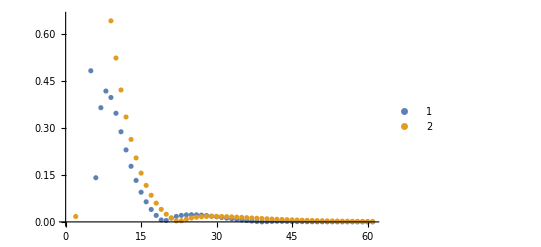

```mathematica
ListPlot[{Subscript[d, TF(2)],Subscript[d, 3(2)]},PlotLegends->Automatic]
```

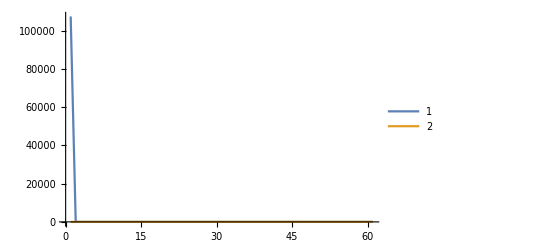

```mathematica
ListLinePlot[{Subscript[d, TF(2)],Subscript[d, 3(2)]},PlotLegends->Automatic,PlotRange->All]
```

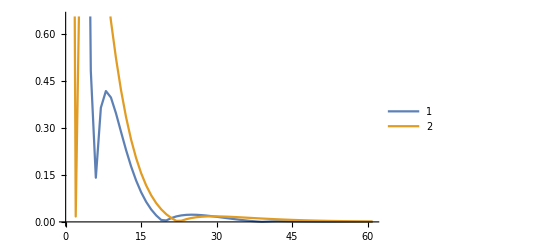

```mathematica
ListLinePlot[{Subscript[d, TF(2)],Subscript[d, 3(2)]},PlotLegends->Automatic]
```

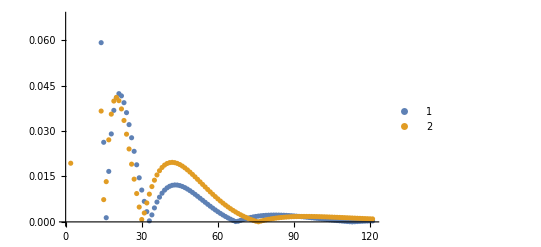

```mathematica
ListPlot[{Subscript[d, TF(10)],Subscript[d, 3(10)]},PlotLegends->Automatic]
```

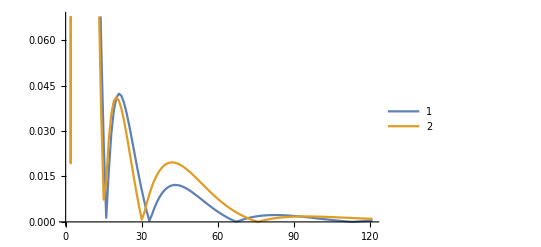

```mathematica
ListLinePlot[{Subscript[d, TF(10)],Subscript[d, 3(10)]},PlotLegends->Automatic]
```

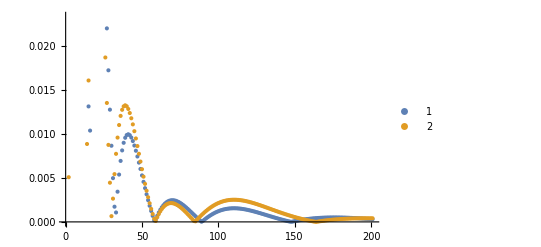

```mathematica
ListPlot[{Subscript[d, TF(28)],Subscript[d, 3(28)]},PlotLegends->Automatic]
```

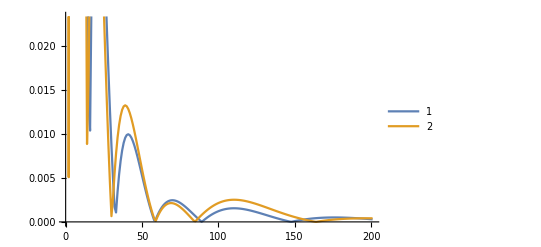

```mathematica
ListLinePlot[{Subscript[d, TF(28)],Subscript[d, 3(28)]},PlotLegends->Automatic]
```

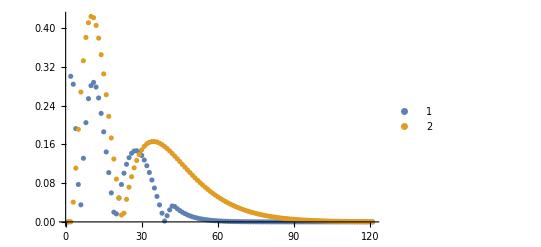

```mathematica
ListPlot[{Subscript[d̃, TF(2)],Subscript[d̃, 3(2)]},PlotRange->All,PlotLegends->Automatic]
```

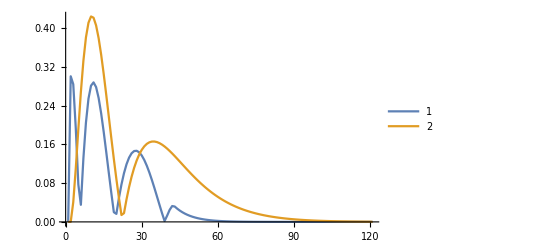

```mathematica
ListLinePlot[{Subscript[d̃, TF(2)],Subscript[d̃, 3(2)]},PlotRange->All,PlotLegends->Automatic]
```

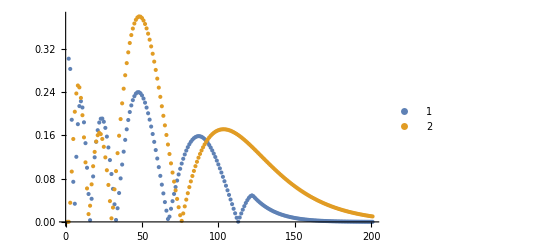

```mathematica
ListPlot[{Subscript[d̃, TF(10)],Subscript[d̃, 3(10)]},PlotRange->All,PlotLegends->Automatic]
```

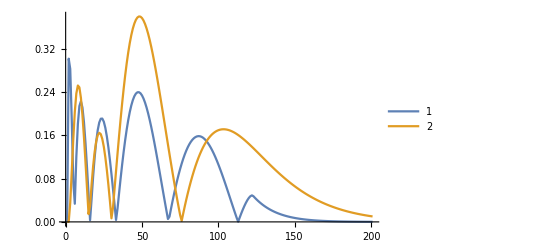

```mathematica
ListLinePlot[{Subscript[d̃, TF(10)],Subscript[d̃, 3(10)]},PlotRange->All,PlotLegends->Automatic]
```

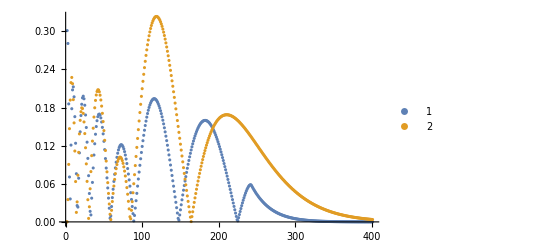

```mathematica
ListPlot[{Subscript[d̃, TF(28)],Subscript[d̃, 3(28)]},PlotRange->All,PlotLegends->Automatic]
```

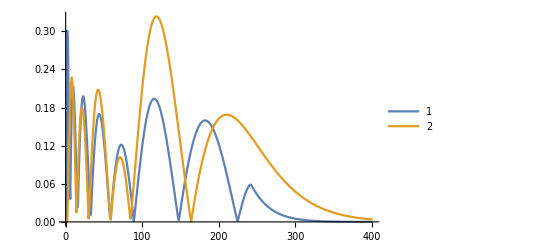

```mathematica
ListLinePlot[{Subscript[d̃, TF(28)],Subscript[d̃, 3(28)]},PlotRange->All,PlotLegends->Automatic]
```

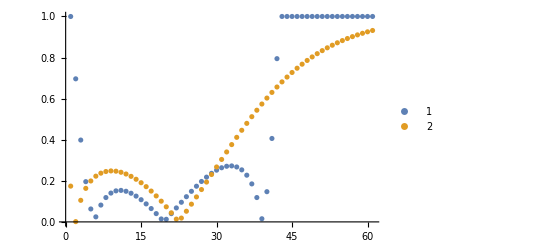

```mathematica
ListPlot[{Subscript[R, TF(2)],Subscript[R, 3(2)]},PlotRange->All,PlotLegends->Automatic]
```

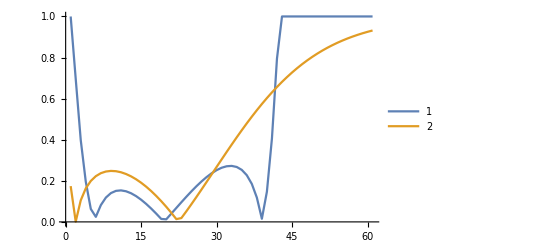

```mathematica
ListLinePlot[{Subscript[R, TF(2)],Subscript[R, 3(2)]},PlotRange->All,PlotLegends->Automatic]
```

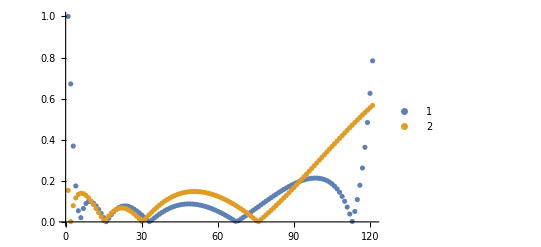

```mathematica
ListPlot[{Subscript[R, TF(10)],Subscript[R, 3(10)]},PlotRange->All,PlotLegends->Automatic]
```

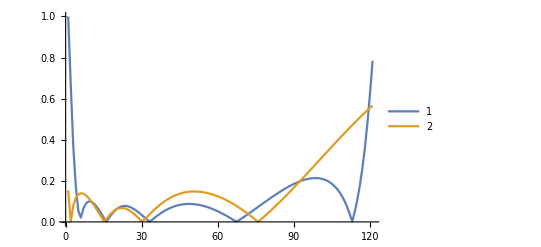

```mathematica
ListLinePlot[{Subscript[R, TF(10)],Subscript[R, 3(10)]},PlotRange->All,PlotLegends->Automatic]
```

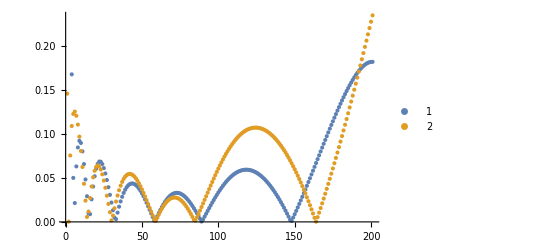

```mathematica
ListPlot[{Subscript[R, TF(28)],Subscript[R, 3(28)]},PlotLegends->Automatic,PlotRange->Automatic]
```

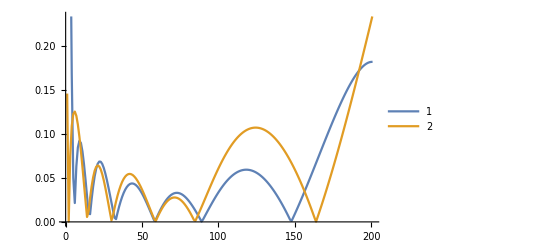

```mathematica
ListLinePlot[{Subscript[R, TF(28)],Subscript[R, 3(28)]},PlotLegends->Automatic,PlotRange->Automatic]
```

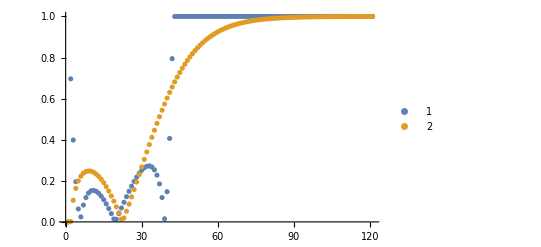

```mathematica
ListPlot[{Subscript[R̃, TF(2)],Subscript[R̃, 3(2)]},PlotLegends->Automatic]
```

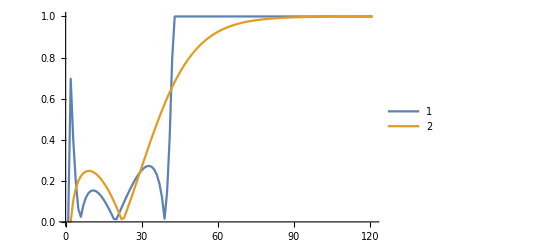

```mathematica
ListLinePlot[{Subscript[R̃, TF(2)],Subscript[R̃, 3(2)]},PlotLegends->Automatic]
```

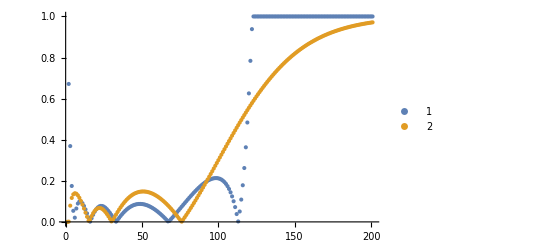

```mathematica
ListPlot[{Subscript[R̃, TF(10)],Subscript[R̃, 3(10)]},PlotLegends->Automatic]
```

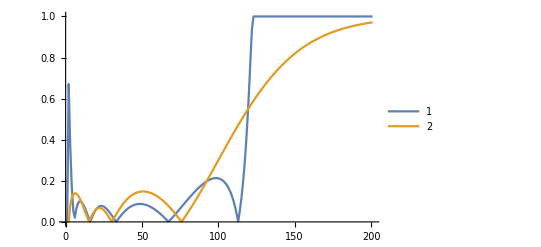

```mathematica
ListLinePlot[{Subscript[R̃, TF(10)],Subscript[R̃, 3(10)]},PlotLegends->Automatic]
```

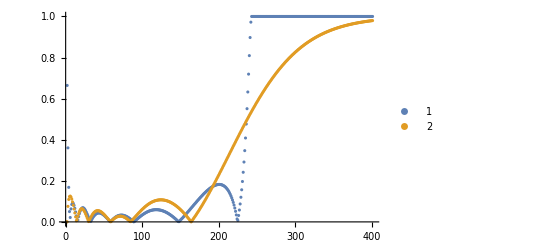

```mathematica
ListPlot[{Subscript[R̃, TF(28)],Subscript[R̃, 3(28)]},PlotLegends->Automatic]
```

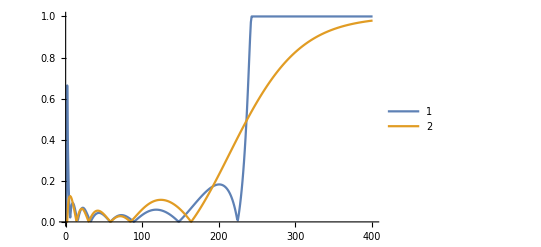

```mathematica
ListLinePlot[{Subscript[R̃, TF(28)],Subscript[R̃, 3(28)]},PlotLegends->Automatic]
```